# Calculus of inductive constructions

## Jose Martin-Garcia

## 2015--2017

Most of this follows the book [amazon]: “Type theory and formal proof”, Nederpelt & Geuvers, CUP 2014 (“the Book”), and the tutorial of Lean 2. There is now the [tutorial of Lean 3].

A webpage with learning material: [web].

## Code

### Notes

#### Calculus of Constructions as given by the Book

Basic notations:
	• Pre-typed variables: Typed[var, type].
	• Lambda term: LambdaFunction[(typed)var, expr].
	• Arrow type: ArrowType[type1, type2]. “Non-dependent function type.”
	• Product type: PiType[typedvar, type]. “Dependent function type.”

The language of λC is formed by expresions A, B, C, ... in

	ℰ = 𝒱 | StarType | BoxType | ℰ[ℰ] | LambdaFunction[Typed[𝒱, ℰ], ℰ] | PiType[Typed[𝒱, ℰ], ℰ] .

with a vocabulary of variables 𝒱 = {𝒶, 𝒷, 𝒸, ...}, in particular using by convention V = {x, y, z, a, b, c, ...} for terms, 𝕍 = {α, β, γ, ...} for types, {s, t, u, v} for sorts and {κ} for kinds. Notation PiType[Typed[𝒶, A], B] is abbreviated ArrowType[A, B] if B does not contain 𝒶 as free variable.

Every expression has a type, but not every expression can be the type of another expression. This breaks ℰ in two parts: the class Λ of terms and the class 𝕋 of types. We furthermore distinguish:
	• Type constructors (some special terms and all types):
		ℂ = 𝕋 | LambdaFunction[Typed[V, 𝕋], ℂ] | LambdaFunction[Typed[𝕍, StarType], ℂ].
		Type constructors that are not types are called “proper constructors”.
		Constructors have types which are kinds.
	• Kinds (subclass of types):
		𝕂 = StarType | ArrowType[𝕂, 𝕂].
		Kinds have types which are sorts.
	• Sorts (just two special (super)types):
		{StarType, BoxType}
The type of StarType is BoxType, but what is the type of BoxType? Some authors use other boxes with a positive integer subindex. If we generalized the construction to an arbitrary list of sorts, with arbitrary Typed relations among them, then we would have the so-called Pure Type Systems.

λC has three important features extending the symply-typed lambda theory (Terms depending on terms):
	• λ2. Terms depending on types: polymorphism.
	• λω. Types depending on types: type constructors
	• λP. Types depending on terms: type constructors

In this notebook we go slightly beyond the standard Calculus of Constructions, introducing sigma (dependent sum) types:
	• SigmaType[Typed[x, A], B] represents the type of pairs (a, b) with Typed[a, A] and Typed[b, B[a/x]]. I think this is like a “semidirect product” generalization of the Cartesian product type, in the same way that pi generalizes arrow. Pairs have associated projection functions, so if Typed[t, SigmaType[Typed[x, A], B] then Type[pi1[t]] is A and Type[pi2[t]] is B[pi1[t]/x].
	• The sigma type acts very much like an existential quantifier. SigmaType[Typed[x, A], B] expresses the fact that there exists a of type A such that B[a/x] holds.
	• This needs to distinguish the types StarType (Type), Set and Prop, but currently we do not make this distinction and always work with StarType. TODO.

We also introduce definitions, following the Book. As in the Book, the definitions are non-recursive here.

#### Calculus of Inductive Constructions as in Lean

This goes beyond the Book in several ways:

• There is an infinite tower of type universes. There is PropType and then there are the hierarchy of type universes TypeU[n] where n is a positive integer. We declare that PropType is TypeU[0]. Then StarType behaves like TypeU[n], while BoxType behaves like TypeU[n+1] for positive n.

• PropType is treated differently than the other universes. PropType is an “impredicative bubble” while the rest of the TypeU[n] are predicative. If we didn’t have PropType then we would be working with Pure Type Systems and Homotopy Theory. Lean has a mode to do that, but standard Lean uses PropType. This is not as nice, but it is still consistent and much easier to use.

• A fundamental type in Lean is the inductive type. In fact many of the other types in Lean are defined in terms of inductive types.

### Begin

```mathematica
BeginPackage["CalculusOfConstructions`"]
```

CalculusOfConstructions`

The elements of the language, all with special typesetting:

```mathematica
Typed::usage="Typed[e, t] declares that expression e has type t, usually typeset as e:t.";
ShowFrom::usage="ShowFrom[type, term] is equivalent to Typed[term, type].";

LambdaFunction::usage="LambdaFunction[v, e] represents the abstraction of the variable v over the term e, usually typeset as λv.e in untyped lambda calculus. LambdaFunction[Typed[v, t], e] represents the abstraction of the typed variable v, with type t, over the term e.";
Assume::usage="Assume[assumptions, conclusion] is equivalent to LambdaFunction[assumptions, conclusion].";

ArrowType::usage="ArrowType[t1, t2] is the type of functions mapping from type t1 to type t2, usually typeset as t1->t2.";
PiType::usage="PiType[Typed[v, t], tterm] is the dependent product type of functions mapping from type t to a type tterm dependent on the variable v of type t.";
InductiveType::usage="InductiveType[cons1, cons2, ...] represents an inductive type defined by the constructors consi.";
Self::usage="Self represents the type being defined inside an InductiveType[...] expression.";
PropType::usage="PropType, typeset as Prop, is the type of propositions. It evaluates to TypeU[0].";
StarType::usage="StarType, typeset as *, is the sort of all types. It evaluates to TypeU[1].";
TypeU::usage="TypeU[n] for a nonnegative integer n represents the universe of types of level n. Level 0 corresponds to the impredicative universe of propositions.";
Pair::usage="Pair[e1, e2] represents a pair of terms e1, e2. It is equivalent to Tuple[e1, e2].";
Tuple::usage="Tuple[e1, e2, e3, ...] represents a tuple of terms e1, e2, e3, ...";
ProductType::usage="ProductType[t1, t2, t3, ...] is a type representing the independent product of types t1, t2, t3, ...";
SigmaType::usage="SigmaType[Typed[v, t], tterm] is the dependent sum type of Pair[v, term[v]], where v has type t and term[v] has a type tterm, still depending on v.";
Defined::usage="Defined[def, term] defines the definiendum def to be the definiens term.";
NullDefiniens::usage"NullDefiniens is a symbol that represents the definiens in a primitive definition.";
Math::usage="Math[Δ, Γ, st] represents the mathematical statement st in the typing context Γ and the environment Δ of definitions. The statement can be a typing judgement with head Type or a definition with head Defined. Math[Γ, st] assumes an empty environment. Math[st] assumes an empty environment and an empty context.";
DerivationRule::usage="DerivationRule[{prem1, prem2, ...}, conc] represents the Gentzen-style derivation rule from the premises premi to the conclusion conc.";
```

Manipulation of expressions:

```mathematica
RenameBound::usage="RenameBound[e, v->w] renames the bound variable v to w in the expression e.";
FreeVariables::usage="FreeVariables[e] returns the list of all free variables (of any type or sort) in the expression e.";
ReplaceFree::usage="ReplaceFree[e, v->a] replaces the free variable v by the term a in expression e.";
AlphaCanonical::usage="AlphaCanonical[e] renames the bound variables in expression e using canonical names (formal variables), hence rendering a unique form of e, that can be compared to other expressions with SameQ to decide alpha-equivalence, as implemented in TildeEqual.";
Subterms::usage="Subterms[e] find the subterms of expression e.";
```

Beta reduction:

```mathematica
BetaReduce::usage="BetaReduce[e, v] beta-reduces the redex (possibly several) with bound variable v in the expression e.";
BetaReduceList::usage="BetaReduceList[e] gives a list of all possible one-step beta reductions of the expression e.";
BetaNormal::usage="BetaNormal[e] returns the beta normal form of the expression e, if it exists.";
BetaNormalRules::usage="BetaNormalRules[e] returns a list of rules representing the possible paths of beta normalization of expression e.";
$BetaReduceIterationLimit="$BetaReduceIterationLimit gives the maximum number of beta reduction steps used in searching for the beta normal form of an expression.";
```

Delta reduction:

```mathematica
DeltaReduce::usage="DeltaReduce[e, env, c] delta-reduces the expression e using the definition for the constant c in the environment env.";
DeltaNormal::usage="DeltaNormal[e, env] delta-reduces the expression e using all definitions in the environment e, in reverse order.";
```

Type finding:

```mathematica
Type::usage="Type[e] computes the type of expression e, with an empty context. Type[e, Γ] uses context Γ in the type computation. A context is a list of Typed declarations. Type[e, Γ, Δ] also uses environment Δ in the type computation. An environment is a list of Defined statements.";
$TypeContext::usage="$TypeContext is a global variable storing a list of global type declarations.";
$TypeEnvironment::usage="$TypeEnvironment is a global variable storing a list of global definitions..";
```

Curry-Howard correspondence:

```mathematica
ToLogic::usage="ToLogic[t] rewrites the type t in logic-connective form.";
FromLogic::usage="FromLogic[p] rewrites the proposition p in type-theory form.";
```

Some nice new types, for typesetting:

```mathematica
NonNegativeIntegers::usage="NonNegativeIntegers represents the domain of nonnegative integers.";
PositiveIntegers::usage="PositiveIntegers represent the domain of positive integers.";
```

Proof language, following Lean:

```mathematica
AnyType::usage="AnyType represents the type of Absurd[t, nt] if t : p and nt : Not[p].";
Absurd::usage="Absurd[t, nt] has type AnyType if t : p and nt : Not[p].";
AndIntro::usage="AndIntro[t1, t2] has type And[p1, p2] if t1, t2 have respective types p1, p2.";
AndElimLeft::usage="AndElimLeft[t] has type p1 if t has type And[p1, p2].";
AndElimRight::usage="AndElimRight[t] has type p2 if t has type And[p1, p2].";
OrIntroLeft::usage="OrIntroLeft[p2, t1] has type Or[p1, p2] if t1 has type p1.";
OrIntroRight::usage="OrIntroRight[p1, t2] has type Or[p1, p2] if t2 has type p2.";
OrElim::usage="OrElim[t, t1, t2] has type p if t : Or[p1, p2], t1 : p1 -> p, t2 : p2 -> p.";
NotIntro::usage="NotIntro[t] has type Not[p] if t : p -> False.";
NotElim::usage="NotElim[nt, t] has type False if nt : Not[p], t : p.";
EquivalentIntro::usage="EquivalentIntro[t1, t2] has type Equivalent[p1, p2] if t1 : p1 -> p2, t2 : p2 -> p1.";
EquivalentElimLeft::usage="EquivalentElimLeft[t] has type p1 -> p2 if t : Equivalent[p1, p2].";
EquivalentElimRight::usage="EquivalentElimRight[t] has type p2 -> p1 if t : Equivalent[p1, p2].";
```

Inductive type functionality:

```mathematica
RecOn::usage="RecOn[indtype][var][values] represents a function that takes all possible values terms of type indtype in var and returns respective values.";
CasesOn::usage="";
InductionOn::usage="";
```

Other constructions, following Lean:

```mathematica
Theorem::usage="Theorem[name, type, term] represents the given theorem, stating the proposition given by type, with proof given by term.";
Lemma::usage="Lemma[name, type, term] is equivalent to Theorem[name, type, term].";
Corollary::usage="Corollary[name, type, term] is equivalent to Theorem[name, type, term].";
HaveFrom::usage="HaveFrom[assume, proof1, proof2] is equivalent to LambdaFunction[assume, proof2][proof1].";
```

```mathematica
Begin["`Private`"]
```

CalculusOfConstructions`Private`

### Global variables

```mathematica
$TypeContext={};
$TypeEnvironment={};
```

### Math

The fundamental unit of mathematical content will be called Math and has the form:

	Math[environment, context, statement]

containing an environment of definitions, a context of typing declarations and the statement, which will be one of

	Typed[term, type]   i.e.   Typed[proof, proposition]
	
	Defined[definiendum, definiens]

Shortcuts:

```mathematica
Math[statement_]:=Math[$TypeEnvironment,$TypeContext,statement];
Math[context_,statement_]:=Math[$TypeEnvironment,context,statement];
```

### Typesetting

#### Definitions

Typesetting utility generalizing Riffle:

```mathematica
Riffle3[list_,{begin_,mid_,end_}]:=Join[{begin},Riffle[list,mid],{end}];
```

The lambda functions:

```mathematica
MakeBoxes[LambdaFunction[var_,term_],fmt_]:=
RowBox[{SubscriptBox["λ",MakeBoxes[var,fmt]],".",MakeBoxes[term,fmt]}];
```

Pairs and tuples. A pair is simply a length two tuple. The choice of angle brackets is arbitrary, but using (), {} or [] would be misleading in the WL, so I want to choose something else.

```mathematica
MakeBoxes[Pair[term1_,term2_],fmt_]:=RowBox[{"⟨",MakeBoxes[term1,fmt],", ",MakeBoxes[term2,fmt],"⟩"}]
```

```mathematica
MakeBoxes[Tuple[terms__],fmt_]:=RowBox[Riffle3[Function[type,MakeBoxes[type,fmt],HoldAll]/@{terms},{"⟨",",","⟩"}]]
```

Typed expressions:

```mathematica
MakeBoxes[Typed[var_,type_],fmt_]:=RowBox[{MakeBoxes[var,fmt],":",MakeBoxes[type,fmt]}];
```

Inductive types:

```mathematica
MakeBoxes[InductiveType[constructors___],fmt_]:=GridBox[List/@(Function[Null,RowBox[{"| ",MakeBoxes[#,fmt]}],HoldAll]/@{constructors}),GridBoxAlignment->{"Columns"->{{Left}}}]
```

```mathematica
MakeBoxes[Self,fmt_]:="#";
```

Defined expressions:

```mathematica
MakeBoxes[Defined[definiendum_,definiens_InductiveType],fmt_]:=GridBox[{{RowBox[{MakeBoxes[definiendum,fmt]," :=                 "}]},{RowBox[{"             ",MakeBoxes[definiens,fmt]}]}}]
```

```mathematica
MakeBoxes[Defined[definiendum_,definiens_],fmt_]:=RowBox[{MakeBoxes[definiendum,fmt]," := ",MakeBoxes[definiens,fmt]}]
```

For primitive definitions we need a concept of NullDefiniens (which could be perhaps represented by Automatic, but I prefer to introduce it as a separate concept). The typeset in the book (page 217) is \[DoubleUpTee], but we do not have such a thing, so I choose the coproduct symbol instead:

```mathematica
MakeBoxes[NullDefiniens,fmt_]:="∐"
```

The arrow type:

```mathematica
MakeBoxes[ArrowType[type1_,type2_],fmt_]:=RowBox[{"(",MakeBoxes[type1,fmt],"→",MakeBoxes[type2,fmt],")"}];
```

The independent product type:

```mathematica
MakeBoxes[ProductType[types__],fmt_]:=RowBox[Riffle3[Function[type,MakeBoxes[type,fmt],HoldAll]/@{types},{"(","×",")"}]]
```

The dependent product type:

```mathematica
MakeBoxes[PiType[typevar_,type_],fmt_]:=RowBox[{SubscriptBox["Π",MakeBoxes[typevar,fmt]],".",MakeBoxes[type,fmt]}]
```

The dependent sum type:

```mathematica
MakeBoxes[SigmaType[typevar_,type_],fmt_]:=RowBox[{SubscriptBox["Σ",MakeBoxes[typevar,fmt]],".",MakeBoxes[type,fmt]}]
```

Types, sorts and kinds:

```mathematica
MakeBoxes[TypeU[0],fm_]:="Prop";
```

```mathematica
MakeBoxes[TypeU[n_],fmt_]:=SubscriptBox["*",MakeBoxes[n,fmt]];
```

Math: typesetting is different depending on whether the statement is a type judgement or a definition. They can be combined, i.e. we can have a definition of a type judgement, and then we still use the typesetting of a definition, as the Book does.

```mathematica
SetAttributes[mathChar,HoldFirst];
mathChar[_Defined|{__Defined}]:=" ⊳ ";
mathChar[_]:=" ⊢ ";
```

```mathematica
MakeBoxes[Math[{},context_,term_],fmt_]:=RowBox[{MakeBoxes[context,fmt],mathChar[term],MakeBoxes[term,fmt]}]
```

```mathematica
MakeBoxes[Math[environment_,context_,term_],fmt_]:=RowBox[{MakeBoxes[environment,fmt],"; ",MakeBoxes[context,fmt],mathChar[term],MakeBoxes[term,fmt]}]
```

Gentzen-style derivation rules. TODO: what could we use instead of FractionBox here?

```mathematica
MakeBoxes[DerivationRule[{premises___},conclusion_],fmt_]:=FractionBox[RowBox[Riffle[List@@(MakeBoxes[#,fmt]&/@Hold[premises]),", "]],MakeBoxes[conclusion,fmt]]
```

Nicer typesetting of some sets:

```mathematica
MakeBoxes[NonNegativeIntegers,fmt_]:="ℕ";
MakeBoxes[PositiveIntegers,fmt_]:=SuperscriptBox["ℕ","+"];
MakeBoxes[Integers,fmt_]:="ℤ";
MakeBoxes[Rationals,fmt_]:="ℚ";
MakeBoxes[Reals,fmt_]:="ℝ";
MakeBoxes[Complexes,fmt_]:="ℂ";
```

#### Notes

• In Coq LambdaFunction[Typed[x, A], B] is written [x:A]B and PiType[Typed[x, A], B] is written (x:A)B . There are no brackets in abstraction, so we have to use brackets for application. For example LambdaFunction[Typed[x, A], B[x]] would be [x:A](B x).

### Processing

The most difficult part here is the code to avoid dummy collisions.

#### Rename bound variables

They can only appear in two places: the first arguments of lambda and pi.

```mathematica
(* Typed bound variables in LambdaFunction terms *)
RenameBound[LambdaFunction[Typed[var_,type_],term_],var_->newvar_]:=LambdaFunction[Typed[newvar,type],ReplaceFree[term,var->newvar,type]];
RenameBound[LambdaFunction[Typed[var_,type_],term_],rule_]:=LambdaFunction[Typed[var,RenameBound[type,rule]],RenameBound[term,rule]];
(* Untyped bound variables in LambdaFunction terms *)
RenameBound[LambdaFunction[var_,term_],var_->newvar_]:=LambdaFunction[newvar,ReplaceFree[term,var->newvar,All]];
RenameBound[LambdaFunction[var_,term_],rule_]:=LambdaFunction[var,RenameBound[term,rule]];
(* (Typed) bound variables in PiType types *)
RenameBound[PiType[Typed[var_,type_],ttype_],var_->newvar_]:=PiType[Typed[newvar,type],ReplaceFree[ttype,var->newvar,type]];
RenameBound[PiType[Typed[var_,type_],ttype_],rule_]:=PiType[Typed[var,RenameBound[type,rule]],RenameBound[ttype,rule]];
(* Bound variables in ArrowType types *)
RenameBound[ArrowType[type1_,type2_],rule_]:=ArrowType[RenameBound[type1,rule],RenameBound[type2,rule]];
(* Recursion *)
RenameBound[term1_[term2_],rule_]:=RenameBound[term1,rule][RenameBound[term2,rule]];
RenameBound[term_,rule_]:=term;
```

#### Find free variables

Free variables, both term variables and type variables together.

```mathematica
DeleteSorts[types_List]:=DeleteCases[types,_TypeU];
```

```mathematica
FreeVariables[LambdaFunction[Typed[var_,type_],term_]]:=DeleteSorts@Complement[Join[FreeVariables[term],FreeVariables[type]],{var}];
FreeVariables[ArrowType[type1_,type2_]]:=DeleteSorts@Complement[Join[FreeVariables[type1],FreeVariables[type2]]];
FreeVariables[Typed[var_,type_]]:=DeleteSorts@FreeVariables[type];
FreeVariables[PiType[Typed[var_,type1_],type2_]]:=DeleteSorts@Complement[Join[FreeVariables[type1],FreeVariables[type2]],{var}];
FreeVariables[LambdaFunction[var_,term_]]:=Complement[FreeVariables[term],{var}];
FreeVariables[term1_[term2_]]:=Union[FreeVariables[term1],FreeVariables[term2]];
FreeVariables[term_]:={term};
```

#### Replace free variables

```mathematica
untype[Typed[var_,type_]]:=var;
untype[var_]:=var;
```

```mathematica
(* Rename a variable of unknown type *)
ReplaceFree[expr_,rule_]:=ReplaceFree[expr,rule,All];
```

```mathematica
(* Variable is bound, so it cannot be renamed. Note we do not check the types *)
ReplaceFree[TypeU[n_],var_->newvar_,_]:=TypeU[n];
ReplaceFree[LambdaFunction[Typed[var_,type_],term_],var_->newvar_,_]:=LambdaFunction[Typed[var,type],term];
ReplaceFree[PiType[Typed[var_,type_],ttype_],var_->newvar_,_]:=PiType[Typed[var,type],ttype];
ReplaceFree[LambdaFunction[var_,term_],var_->newvar_,_]:=LambdaFunction[var,term];
```

```mathematica
(* *)
ReplaceFree[(head:LambdaFunction|PiType)[var1_,term_],var2_->var3_,type_]:=With[{frees3=FreeVariables[var3],uvar1=untype[var1]},
If[FreeQ[frees3,uvar1],
head[
ReplaceFree[var1,var2->var3,type],
ReplaceFree[term,var2->var3,type]
],
With[{newvar=First[Complement[lookup[type],frees3,{uvar1,var2}]]},
head[
ReplaceFree[var1,uvar1->newvar,type],
ReplaceFree[ReplaceFree[term,uvar1->newvar,type],var2->var3,type]
]
]
]
];
```

```mathematica
ReplaceFree[term1_[term2_],rule_,type_]:=ReplaceFree[term1,rule,type][ReplaceFree[term2,rule,type]];
ReplaceFree[term_,rule_,type_]:=ReplaceAll[term,rule];
```

```mathematica
ReplaceFree[Typed[var_,type_],rule_,itype_]:=Typed[ReplaceFree[var,rule,itype],ReplaceFree[type,rule,itype]];
```

#### Alpha conversion and equivalence

This is the default association of variables to use, grouped by levels:

```mathematica
canonicalVariables=Association[
TypeU[0]->{α,β,γ,δ,χ,ϵ,ϕ,η,ι,κ,λ,λ1,λ2,λ3,λ4,λ5,λ6,λ7,λ8,λ9,λ10},
TypeU[1]->{μ,ν,ω,π,θ,ρ,σ,τ,υ,ξ,ψ,ζ,ζ1,ζ2,ζ3,ζ4,ζ5,ζ6,ζ7,ζ8,ζ9,ζ10},
TypeU[2]->{A,B,C},
All->{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,z1,z2,z3,z4,z5,z6,z7,z8,z9,z10}
];
```

```mathematica
lookup[TypeU[n_]]:=canonicalVariables[TypeU[n]];
lookup[_]:=canonicalVariables[All];
```

```mathematica
getVariable[assoc_,TypeU[n_]]:=iGetVariable[assoc,TypeU[n]];
getVariable[assoc_,type_]:=iGetVariable[assoc,All];
iGetVariable[assoc_,type_]:=With[{vars=assoc[type]},
{First[vars],ReplacePart[assoc,Key[type]->Rest[vars]]}
];
```

```mathematica
(* Use our canonical variables *)
AlphaCanonical[list_List]:=AlphaCanonical/@list;
AlphaCanonical[term_]:=First[alphaCanon[{term,canonicalVariables}]];
```

```mathematica
(* Replace all bound variables *)
alphaCanon[{(head:LambdaFunction|PiType)[Typed[var_,type_],term_],assoc_}]:=Module[{data=getVariable[assoc,type],newpair},
newpair=alphaCanon[{ReplaceFree[term,var->First[data]],Last[data]}];
{head[Typed[First[data],type],First[newpair]],Last[newpair]}
];
alphaCanon[{LambdaFunction[var_,term_],assoc_}]:=
Module[{data=getVariable[assoc,All],newpair},
newpair=alphaCanon[{ReplaceFree[term,var->First[data]],Last[data]}];
{LambdaFunction[First[data],First[newpair]],Last[newpair]}
];
(* Recurse *)
alphaCanon[{term1_[term2_],assoc_}]:=Module[{newpair1,newpair2},
newpair1=alphaCanon[{term1,assoc}];
newpair2=alphaCanon[{term2,Last[newpair1]}];
{First[newpair1][First[newpair2]],Last[newpair2]}
];
alphaCanon[{ArrowType[type1_,type2_],assoc_}]:=Module[{newtype1,newtype2},
newtype1=alphaCanon[{type1,assoc}];
newtype2=alphaCanon[{type2,Last[newtype1]}];
{ArrowType[First[newtype1],First[newtype2]],Last[newtype2]}
];
alphaCanon[{term_,assoc_}]:={term,assoc};
```

```mathematica
TildeEqual[terms__]:=SameQ@@(AlphaCanonical/@{terms});
```

#### Subterms

```mathematica
Subterms[LambdaFunction[var_,term_]]:=Append[Subterms[term],LambdaFunction[var,term]];
Subterms[term1_[term2_]]:=Join[Subterms[term1],Subterms[term2],{term1[term2]}];
Subterms[term_]:={term};
```

#### Beta reduction

One-step beta reduction of an expression. In case there are multiple redexes, specify the corresponding bound variable:

```mathematica
BetaReduce[expr_,var_]:=expr/.{
LambdaFunction[Typed[var,type_],term_][arg_]:>ReplaceFree[term,var->arg,type],
LambdaFunction[var,term_][arg_]:>ReplaceFree[term,var->arg,All]
};
```

Note: Automath uses the notation <v>F instead of F v, or our F[v]. This has the advantage that for lambda functions we have <v>LambdaFunction[x, M] and v is placed next to x, instead of the standard LambdaFunction[x, M][v], in which x and v are separated by M.

List of possible one-step beta reductions of an expression. The result is a list whose length equals the number of different redexes of the expression. If there are none, then the list is empty. Note that ReplaceList[a, x->y] also returns an empty list.

```mathematica
BetaReduceList[list_List]:=BetaReduceList/@list;
BetaReduceList[expr_]:=With[{redexvars=Cases[expr,LambdaFunction[var_,term_][arg_]:>untype[var],{0,Infinity},Heads->True]},
If[
DuplicateFreeQ[redexvars],
BetaReduce[expr,#]&/@redexvars,
BetaReduceList[AlphaCanonical[expr]]
]
];
```

Beta reduction normalization:

```mathematica
BetaNormal::loop=BetaNormalRules::loop="Found beta reduction loop.";
BetaNormal::itlim=BetaNormalRules::itlim="Beta reduction reached maximum number of iterations `1`.";
BetaNormal::non1=BetaNormalRules::non1="Beta normal form is not unique.";
```

```mathematica
$BetaReduceIterationLimit=10;
```

```mathematica
checkBetaNormal[bn_,head_]:=(bn=!="Loop" || Message[head::loop,expr])&&
(bn=!="MaxIterations"||Message[head::itlim,$BetaReduceIterationLimit])&&
(bn=!="NonUnique"||Message[head::non1])
```

```mathematica
BetaNormal[expr_]:=With[{bn=Catch[betaNormal[{expr},AlphaCanonical[expr],0,False],"BetaNormalError"]},
bn/;checkBetaNormal[bn,BetaNormal]
];
```

```mathematica
BetaNormalRules[expr_]:=With[{bn=Catch[Reap[betaNormal[{expr},AlphaCanonical[expr],0,True]],"BetaNormalError"]},
Flatten[bn[[2]]]/;checkBetaNormal[bn,BetaNormalRules]
];
```

```mathematica
betaNormal[exprs_List,original_,n_,sowrules_]:=Module[{brls,fbrl},
brls=AlphaCanonical/@BetaReduceList/@exprs;
fbrl=DeleteDuplicates[Flatten[brls]];
If[n>$BetaReduceIterationLimit,Throw["MaxIterations","BetaNormalError"]];
If[MemberQ[fbrl,original]||fbrl===exprs,Throw["Loop","BetaNormalError"]];
If[fbrl==={},
If[Length[exprs]==1,
(* A normal form has been found *)
First[exprs],
(* This should never happen *)
Throw["NonUnique","BetaNormalError"]
],
(* Recurse *)
If[sowrules,Sow[Thread/@Thread[Rule[exprs,brls]]]];
If[n≥$BetaReduceIterationLimit,
Throw["MaxIterations","BetaNormalError"],
betaNormal[fbrl,original,n+1,sowrules]
]
]
]
```

#### Delta reduction

Extract the constants being defined, ignoring the definitions associated to inductive types:

```mathematica
DefinedConstant[Defined[constant_Symbol,InductiveType[___]]]:=Nothing;
DefinedConstant[Defined[constant_Symbol,definiens_]]:=constant;
DefinedConstant[Defined[atom_?AtomQ,definiens_]]:=Message[Defined::atom,atom];
DefinedConstant[Defined[definiendum_,definiens_]]:=Head[definiendum];
DefinedConstant[environment_List]:=DefinedConstant/@environment;
```

```mathematica
dropDefined[environment_List,constant_]:=DeleteCases[environment,defined_/;DefinedConstant[defined]===constant];
```

```mathematica
Off[RuleDelayed::rhs]
makePattern[constant_Symbol]:=constant;
makePattern[h_[Pair[a_Symbol,b_Symbol]]]:=h[Pair[Pattern[a,Blank[]],Pattern[b,Blank[]]]];
makePattern[h_[Tuple[as__Symbol]]]:=h[Tuple@@(Pattern[#,Blank[]]&/@{as})];
makePattern[h_[as__Symbol]]:=h@@(Pattern[#,Blank[]]&/@{as});
On[RuleDelayed::rhs]
```

```mathematica
dropTyped[Typed[term_,type_]]:=term;
dropTyped[term_]:=term;
```

```mathematica
Defined::comp="Environment `1` already contains the defined constant in `2`.";
Defined::atom="A number or a string cannot be the definiendum of a definition.";
```

Expand the definition of the given constant in the expression expr, as determined by the environment. We do not check here that the arguments being replaced are compatible. We will check that later when using the context for typing.

```mathematica
(* Delta-reduce a single constant of the environment *)
DeltaReduce[expr_,environment_List,constant_Symbol]:=Module[{constants,defined},
constants=DefinedConstant[environment];
If[FreeQ[constants,constant],Return[expr]];
defined=Extract[environment,First@Position[constants,constant]];
ReplaceRepeated[expr,makePattern[First[defined]]->dropTyped[Last[defined]]]
];
(* Delta-reduce a list of constants *)
DeltaReduce[expr_,environment_List,list_List]:=Fold[DeltaReduce[#1,environment,#2]&,expr,list];
```

```mathematica
(* Delta-reduce the complete environment, in the appropriate order *)
DeltaNormal[expr_,environment_List]:=DeltaReduce[expr,environment,Reverse[DefinedConstant[environment]]];
```

Note that Delta-reduction can be applied to any expression, both terms and types.

#### Eta reduction (TODO)

This is reduction using extensional equality. I have no idea how to do this.

#### Iota reduction (TODO)

I think this is related to finding an object of type X obeying a predicate P of type ArrowType[X, PropType].

#### Inductive type recursors

```mathematica
RecOn[Defined[_,indtype_InductiveType]][var_][values_]:=RecOn[indtype][var][values];
RecOn[indtype_InductiveType][var_][values_]:=
```

### Types

#### Type universes

Given Typed[a, TypeU[m]] and Typed[b, TypeU[n]] then the type of ArrowType[a, b] is

```mathematica
ArrowTypeU[TypeU[m_],TypeU[0]]:=TypeU[0];
ArrowTypeU[TypeU[0],TypeU[n_]]:=TypeU[n];
ArrowTypeU[TypeU[m_],TypeU[n_]]:=TypeU[Max[m,n]];
```

To imitate partially what we had before we define:

```mathematica
PropType:=TypeU[0];
StarType:=TypeU[1];
```

The analogy of BoxType with TypeU[2] is misleading. BoxType is about type constructors (whose types are “sorts”), not about higher-order types.

Results taken from Lean:

• Types of basic types:
	ℕ : Type₁
	bool : Type₁
	ℕ → bool : Type₁
	ℕ × bool : Type₁
	ℕ × ℕ → ℕ : Type₁
	ℕ → ℕ → ℕ : Type₁
	ℕ → ℕ → ℕ : Type₁
	ℕ → ℕ → bool : Type₁
	(ℕ → ℕ) → ℕ : Type₁

• More cases:
	A.{l_1} : Type.{l_1}
	B.{l_1} : Type.{l_1}
	F.{l_1 l_2} : Type.{l_1} → Type.{l_2}
	G.{l_1 l_2 l_3} : Type.{l_1} → Type.{l_2} → Type.{l_3}
	F.{l_1 l_2} A.{l_1} : Type.{l_2}
	F.{1 l_1} ℕ : Type.{l_1}
	G.{l_1 l_2 l_3} A.{l_1} : Type.{l_2} → Type.{l_3}
	G.{l_1 l_2 l_3} A.{l_1} B.{l_2} : Type.{l_3}
	G.{l_1 1 l_2} A.{l_1} ℕ : Type.{l_2}
	prod.{l_1 l_2} : Type.{l_1} → Type.{l_2} → Type.{max 1 l_1 l_2}
	prod.{l_1 l_2} A.{l_1} : Type.{l_2} → Type.{max 1 l_1 l_2}
	A.{l_1} × B.{l_2} : Type.{max 1 l_1 l_2}
	ℕ × ℕ : Type₁
	list.{l_1} : Type.{l_1} → Type.{max 1 l_1}
	list.{l_1} A.{l_1} : Type.{max 1 l_1}
	list.{1} ℕ : Type₁
	Type.{l_1} : Type.{l_1+1}
	Type.{l_1} → Type.{l_2} : Type.{max (l_1+1) (l_2+1)}
	
	C : Type.{u}
	A.{l_1} → C : Type.{imax l_1 u}
	D.{l_1} → E.{l_2} : Type.{imax l_1 l_2}
	D.{v} → E.{v} : Type.{v}

• Products, pairs and projectors:
	prod.{l_1 l_2} : Type.{l_1} → Type.{l_2} → Type.{max 1 l_1 l_2}
	pair.{l_1 l_2} : ?A → ?B → ?A × ?B
	pr₁ : ?A × ?B → ?A
	pr₂ : ?A × ?B → ?B

The Lean tutorial says: “Universe constraints are subtle, but the good news is that Lean handles them pretty well. As a result, in ordinary situations you can ignore the universe parameters and simply write Type, leaving the universe management to Lean.” QUESTION: If this was always true, why would we have to handle universes explicitly?

#### Type formulas

• Naming conventions are kind of a nightmare... Beware particularly of the difference between the “dependent product” type pi and the “independent product” type prod.

• Extend a context with a new typing judgement. Instead of checking that the new judgement is not contradictory with any of the existing ones, we simply prepend the new judgement, so that it has more priority. This basically implements priority to more local variables:

```mathematica
(* This implements the (weak) derivation rule *)
extendContext[context_,typed_]:=DeleteDuplicates[Prepend[context,typed]];
```

• When extending an environment, the new definition may require the previous definitions, so we cannot prepend it. We really need to append it. Therefore, to avoid inconsistency, we need to check that the new constant being defined has not yet been defined.

```mathematica
(* This implements the (def) derivation rule, which is another weaking rule *)
extendEnvironment[environment_,defined_]:=Append[environment,defined]/;(FreeQ[environment,DefinedConstant[defined]]||Message[Defined::comp,environment,defined]);
```

• Basic definitions for the function Type, that implements type finding in the presence of a context and an environment.

```mathematica
(* Shortcuts *)
Type[term_]:=Type[term,$TypeContext,$TypeEnvironment];
Type[term_,context_]:=Type[term,context,$TypeEnvironment];
```

```mathematica
(* This is the (var) derivation rule, though we do not check that type is really a type *)
Type[var_,{___,Typed[var_,type_],___},environment_]:=type;
Type[Typed[var_,type_],context_,environment_]:=type;
```

```mathematica
(* Inductive types in Defined objects *)
Type[var_,context_,env:{___,Defined[Typed[name_,_],InductiveType[___,Typed[var_,type_],___]],___}]:=Type[var,extendContext[context,Typed[var,type]],env]/.Self->name;
Type[var_,context_,{___,Defined[Typed[var_,type_],_],___}]:=type;
Type[var_,context_,{left___,Defined[var_,def_],right___}]:=Type[def,context,{left,right}];
```

```mathematica
(* Inductive types without Defined objects *)
Type[var_,context_,{___,itype:InductiveType[___,Typed[var_,type_],___],___}]:=type/.Self->itype;
```

```mathematica
Type[Inactive[head_],context_,environment_]:=Type[head,context,environment];
```

• Type of types:

```mathematica
(* This is the main relation between type universes *)
Type[TypeU[n_],context_,environment_]:=TypeU[n+1];
```

• Type of functions. Result is a “ dependent product type”, not to be confused with the “independent product type”. If Typed[A, s1] and Typed[B, s2] and Type[PiType[Typed[x, A], B]] is s3, then it is standard to represent the situation as the triple (s1, s2, s3).

```mathematica
(* This is the (abst) derivation rule, though we do not check validity of typed *)
Type[LambdaFunction[typed_Typed,term_],context_,environment_]:=PiType[typed,Type[term,extendContext[context,typed],environment]];
```

This definition is needed to handle the simply-typed lambda calculus:

```mathematica
(* Special case of the (abst) derivation rule *)
Type[LambdaFunction[var_,term_],context_,environment_]:=ArrowType[Type[var,context,environment],Type[term,context,environment]];
```

• Proof language definitions, following Lean:

```mathematica
TypeMatchQ[expr_,pat_]:=MatchQ[expr,pat];
SameTypeQ[type1_,type2_]:=SameQ[type1,type2];
SameTypeQ[type_,AnyType]:=True;
SameTypeQ[AnyType,type_]:=True;
```

Beware that our Equivalent is Orderless!

```mathematica
Type[Absurd[term_,nterm_],context_,environment_]:=With[{type=Type[term,context,environment],ntype=Type[nterm,context,environment]},
AnyType/;(TypeMatchQ[ntype,Not[_]|Inactive[Not][_]]&&SameTypeQ[ntype[[1]],type])||(TypeMatchQ[type,Not[_]|Inactive[Not][_]]&&SameTypeQ[type[[1]],ntype])
];
Type[NotIntro[term_],context_,environment_]:=With[{type=Type[term,context,environment]},
Not[type[[1]]]/;TypeMatchQ[type,ArrowType[_,False]]
];
Type[NotElim[nterm_,term_],context_,environment_]:=With[{ntype=Type[nterm,context,environment],type=Type[term,context,environment]},
False/;TypeMatchQ[ntype,Not[_]]&&SameTypeQ[ntype[[1]],type]
];
Type[AndIntro[term1_,term2_],context_,environment_]:=And[Type[term1,context,environment],Type[term2,context,environment]];
Type[AndElimLeft[term_],context_,environment_]:=With[{type=Type[term,context,environment]},type[[1]]/;TypeMatchQ[type,And[_,_]]];
Type[AndElimRight[term_],context_,environment_]:=With[{type=Type[term,context,environment]},type[[2]]/;TypeMatchQ[type,And[_,_]]];
Type[OrIntroLeft[term2_,type1_],context_,environment_]:=Or[type1,Type[term2,context,environment]];
Type[OrIntroRight[term1_,type2_],context_,environment_]:=Or[Type[term1,context,environment],type2];
Type[OrElim[term_,term1_,term2_],context_,environment_]:=With[{type=Type[term,context,environment],type1=Type[term1,context,environment],type2=Type[term2,context,environment]},
type1[[2]]/;TypeMatchQ[type,Or[_,_]]&&TypeMatchQ[type1,ArrowType[_,_]]&&TypeMatchQ[type2,ArrowType[_,_]]&&SameTypeQ[type[[1]],type1[[1]]]&&SameTypeQ[type[[2]],type2[[1]]]&&SameTypeQ[type1[[2]],type2[[2]]]
];
Type[Trivial[],context_,environment_]:=True;
Type[EquivalentIntro[term1_,term2_],context_,environment_]:=With[{type1=Type[term1,context,environment],type2=Type[term2,context,environment]},Equivalent[type1[[1]],type2[[1]]]/;TypeMatchQ[type1,ArrowType[_,_]]&&TypeMatchQ[type2,ArrowType[_,_]]&&SameTypeQ[type1[[1]],type2[[2]]]&&SameTypeQ[type1[[2]],type2[[1]]]
];
Type[EquivalentElimLeft[term_],context_,environment_]:=With[{type=Type[term,context,environment]},
ArrowType[type[[1]],type[[2]]]/;TypeMatchQ[type,Equivalent[_,_]]
];
Type[EquivalentElimRight[term_],context_,environment_]:=With[{type=Type[term,context,environment]},
ArrowType[type[[2]],type[[1]]]/;TypeMatchQ[type,Equivalent[_,_]]
];
```

```mathematica
(*Type[ExistsIntro[type_,pred_,term_,predterm_],context_,environment_]:=With[{predtype=Type[pred,context,environment],termtype=Type[term,context,environment],predtermtype=Type[predterm,context,environment]},
Exists[Typed[term,
];*)
```

• Definitions:

```mathematica
Defined::type="Declared type `1` does not agree with the term's type `2`.";
```

```mathematica
Type[Defined[Typed[def_,type_],term_],context_,environment_]:=With[{termtype=Type[term,context,environment]},
type/;SameTypeQ[type,termtype]||Message[Defined::type,type,termtype]
];
Type[Defined[def_,Typed[term_,type_]]]:=Type[Defined[Typed[def,type],term]];
Type[Defined[def_,term_],context_,environment_]:=Type[term,context,environment];
```

```mathematica
Type[Math[environment2_,context2_,statement_],context1_,environment1_]:=Type[statement,Join[context1,context2],Join[environment1,environment2]];
```

• Type of applications:

```mathematica
(* This is the (appl) derivation rule, and here we do check compatibility *)
Type[term1_[term2_],context_,environment_]:=With[{res=Catch[combineTypes[
Typed[term1,Type[term1,context,environment]],
Typed[term2,Type[term2,context,environment]],
context,environment
],"IncompatibleTypes"]},
res/;res=!=$Failed
];
```

```mathematica
Type::comp="Cannot apply function `1` of type `2` on argument `3` of type `4`.";
```

```mathematica
typeReduce[type_,context_,environment_]:=BetaNormal[DeltaNormal[type,environment]];
```

The definition with PiType can be considered an application of the pi type to term2, like lambda-application. Some systems, like the Automath family, have formalized this. Then the difference between lambda and pi disappears. In Automath, both LambdaFunction[Typed[x, A], B] and PiType[Typed[x, A], B] are denoted [x:A]B .

```mathematica
combinedType[Typed[term1_,ArrowType[type2_,type3_]],Typed[term2_,type2_],context_,environment_]:=type3;
combinedType[Typed[term1_,ArrowType[type1_,type3_]],Typed[term2_,type2_],context_,environment_]:=type3/;TildeEqual[type1,type2];
combinedType[Typed[term1_,PiType[Typed[var_,type2_],type3_]],Typed[term2_,type2_],context_,environment_]:=type3/.var->term2;
combinedType[Typed[term1_,type1_],Typed[term2_,type2_],context_,environment_]:=With[{rtype1=typeReduce[type1,context,environment],rtype2=typeReduce[type2,context,environment]},
combinedType[Typed[term1,rtype1],Typed[term2,rtype2],context,environment]/;rtype1=!=$Failed &&rtype2=!=$Failed&&(rtype1=!=type1||rtype2=!=type2)
];
combinedType[_Typed,_Typed,_,_]:=$Failed;
```

```mathematica
combineTypes[typed1_Typed,typed2_Typed,context_,environment_]:=With[{type=combinedType[typed1,typed2,context,environment]},
If[type=!=$Failed,
type,
Message[Type::comp,typed1[[1]],typed1[[2]],typed2[[1]],typed2[[2]]];
Throw[$Failed,"IncompatibleTypes"]
]
];
```

• Independent product type prod and sigma type (AKA dependent pair type or dependent sum type):

```mathematica
Type[Pair[var1_,var2_],context_,environment_]:=If[FreeQ[var2,var1],
ProductType[Type[var1,context,environment],Type[var2,context,environment]],
With[{typed1=Typed[var1,Type[var1,context,environment]]},
SigmaType[typed1,Type[var2,extendContext[context,typed1],environment]]
]
];
```

For tuples of more than two elements we do not suppport dependencies (it seems to be the standard thing to do), though we could easily ad it by having nested sigma objects (like lambda does).

```mathematica
Type[Tuple[vars__],context_,environment_]:=ProductType@@(Type[#,context,environment]&/@{vars});
```

```mathematica
(* This is the (form) derivation rule, and again we do not check that typed is valid *)
Type[PiType[typed:Typed[_,type1_],type2_],context_,environment_]:=ArrowTypeU[Type[type1,context,environment],Type[type2,extendContext[context,typed],environment]];
(* Special case of the (form) derivation rule *)
Type[ArrowType[type1_,type2_],context_,environment_]:=ArrowTypeU[Type[type1,context,environment],Type[type2,context,environment]];
```

I’m not completely sure about the following, but this proceeds by analogy with the (form) derivation rule. I don’t know what to do for a prod of more than 2 types. TODO.

```mathematica
Type[SigmaType[typed_Typed,type2_],context_,environment_]:=Type[type2,extendContext[context,typed],environment];
(* Special case of the (form) derivation rule *)
Type[ProductType[type1_,type2_],context_,environment_]:=Type[type2,context,environment];
```

```mathematica
Type[InductiveType[constructors__],context_,environment_]:=StarType;
```

• Handle definitions in the terms.

```mathematica
CheckTypes[list1_List,list2_List,context_,environment_]:=And[
Length[list1]===Length[list2],
Inner[SameQ,Type[#,context,environment]&/@list1,Type[#,context,environment]&/@list2,And]
]||Message[Defined::incomp,list1,list2]
```

```mathematica
Defined::incomp="Incompatible types of argument lists `1` and `2`."
```

Incompatible types of argument lists `1` and `2`.

```mathematica
(* These implement the (inst) derivation rule: definitions in the terms *)
Type[expr_,context_,{___,Defined[expr_,Typed[_,type_]],___}]:=type;
Type[expr_,context_,{___,Defined[Typed[expr_,type_],term_],___}]:=type;
Type[expr_,context_,environment:{___,Defined[expr_,term_],___}]:=Type[term,context,environment];
Type[expr:head_[args1___],context_,environment:{___,Defined[definiendum:head_[args2___],Typed[_,type_]],___}]:=type/;MatchQ[expr,makePattern[definiendum]] &&CheckTypes[{args1},{args2},context,environment];
Type[expr:head_[___],context_,environment:{___,Defined[head_[___],_],___}]:=Type[DeltaNormal[expr,environment],context,{}];
```

```mathematica
(* These implement the (conv) derivation rule: definitions in the types *)
```

• Auto-replacements by simpler (but “judgementally equivalent”) expressions:

```mathematica
Tuple[term1_,term2_]:=Pair[term1,term2];
```

```mathematica
PiType[Typed[var_,type1_],type2_]:=ArrowType[type1,type2]/;FreeQ[type2,var];
```

```mathematica
SigmaType[Typed[var_,type1_],type2_]:=ProductType[type1,type2]/;FreeQ[type2,var]
```

• Note: the derivation rule (conv) in page 204 is odd. I don’t know how to program it so that it works automatically. Currently it requires explicit use of DeltaReduce on the user’s part. Otherwise I would have to check for every single output type whether it contains something that can be replaced using the environmental definitions.

• Finally there is also the (par) derivation rule in page 206 that allows the inverse of Delta reduction, that is, replacing the definiens by the definiendum, for example to simplify the form of a large expression. The Book says explicitly that this is a rule that must be used “whenever we like”, but need not be considered in the theoretical development.

• Additional notes: Lean is able to infer the types of undefined objects when they can only consistently be of a given type.

### Shortcuts and aliases

```mathematica
LambdaFunction[term_]:=term;
LambdaFunction[var_,vars__,term_]:=LambdaFunction[var,LambdaFunction[vars,term]];
```

```mathematica
BetaReduce[term_]:=term;
BetaReduce[term_,var_,vars__]:=BetaReduce[BetaReduce[term,var],vars];
```

```mathematica
DeltaReduce[expr_,environment_]:=expr;
DeltaReduce[expr_,environment_,var_,vars__]:=DeltaReduce[DeltaReduce[expr,environment,var],DeltaReduce[dropDefined[environment,var],environment,var],vars];
```

```mathematica
Typed[var_,vars__,type_]:=Sequence@@Thread[Typed[{var,vars},type],List];
```

```mathematica
ArrowType[type1_,type2_,types__]:=ArrowType[type1,ArrowType[type2,types]];
```

```mathematica
PiType[var_,vars__,type_]:=PiType[var,PiType[vars,type]];
```

```mathematica
SigmaType[var_,vars__,type_]:=SigmaType[var,SigmaType[vars,type]];
```

```mathematica
Assume[assumptions___,conclusion_]:=LambdaFunction[assumptions,conclusion];
```

```mathematica
HaveFrom[assume_,proof1_][proof2_]:=LambdaFunction[assume,proof2][proof1];
```

```mathematica
ShowFrom[type_,term_]:=Typed[term,type];
```

```mathematica
Theorem[name_,term_]:=Defined[name,term];
Theorem[name_,type_,term_]:=Defined[Typed[name,type],term];
Lemma[args__]:=Theorem[args];
Corollary[args__]:=Theorem[args];
```

### Currying versus vararg

The standard approach in lambda calculus is to use 1-arg functions only, and use nested lambdas to handle multiple arguments. However, in some cases it is natural to take several elements at once, for instance when they all belong to the same type. Then we use tuples of n elements (called pairs for n=2).

Note this representation:

```mathematica
f[Pair[x,y]]
```

f[⟨x, y⟩]

That is the closest that we will get to WL’s f[x, y]. The important thing is that the pair is still **one** argument for f.

### ToLogic/FromLogic

We can create a function that transforms types into logical expressions and viceversa. The problem is that the logical expressions evaluate, so we need Inactive.

#### Elementary connectives?

In type theory the basic constructions are Implies and ForAll. We can then construct:

```mathematica
rule=Exists[x_,Not[x_]]:>True;
```

```mathematica
Equivalent[False,ForAll[x,x]]/.rule
```

True

```mathematica
Equivalent[Not[p],Implies[p,False]]
```

True

In classical logic we could define new connectives using double negations:

```mathematica
Equivalent[And[p,q],Not[Implies[p,Not[q]]]]
```

p&&q⧦!(p⇒!q)

```mathematica
BooleanTable[%,{p,q}]
```

{True,True,True,True}

```mathematica
Equivalent[Or[p,q],Implies[Not[p],q]]
```

(!p⇒q)⧦p||q

```mathematica
BooleanTable[%,{p,q}]
```

{True,True,True,True}

```mathematica
Equivalent[Exists[x,p[x]],Not[ForAll[x,Not[p[x]]]]]
```

True

But we want to avoid double negations to have intuitionistic logic. So we use instead:

```mathematica
Equivalent[And[p,q],ForAll[x,Implies[Implies[p,Implies[q,x]],x]]]
```

p&&q⧦∀_x((p⇒(q⇒x))⇒x)

```mathematica
BooleanTable[%,{p,q}]/.rule
```

{True,True,True,True}

```mathematica
Equivalent[Or[p,q],ForAll[x,Implies[Implies[p,x],Implies[Implies[q,x],x]]]]
```

∀_x((p⇒x)⇒((q⇒x)⇒x))⧦p||q

```mathematica
BooleanTable[%,{p,q}]/.rule
```

{True,True,True,True}

```mathematica
Equivalent[Exists[x,p[x]],ForAll[z,Implies[ForAll[x,Implies[p[x],z]],z]]]
```

∃_x p[x]⧦∀_z(∀_x(p[x]⇒z)⇒z)

I don’t know how to prove that. Using again the excluded middle in z (which is a Boolean), we can rewrite:

```mathematica
Equivalent[Exists[x,p[x]],Implies[ForAll[x,Implies[p[x],True]],True]&&Implies[ForAll[x,Implies[p[x],False]],False]]
```

True

#### FromLogic

```mathematica
FromLogic[False]:=PiType[Typed[α,TypeU[0]],α];
```

```mathematica
FromLogic[Inactive[Not][p_]]:=ArrowType[FromLogic[p],PiType[Typed[α,TypeU[0]],α]];
```

```mathematica
FromLogic[Inactive[Implies][p_,q_]]:=ArrowType[FromLogic[p],FromLogic[q]];
```

```mathematica
FromLogic[Inactive[And][p_,q_]]:=PiType[Typed[α,TypeU[0]],ArrowType[ArrowType[FromLogic[p],ArrowType[FromLogic[q],α]],α]];
```

```mathematica
FromLogic[Inactive[Or][p_,q_]]:=PiType[Typed[α,TypeU[0]],ArrowType[ArrowType[FromLogic[p],α],ArrowType[ArrowType[FromLogic[q],α],α]]]
```

```mathematica
FromLogic[Inactive[ForAll][var_,Element[var_,set_],prop_]]:=PiType[Typed[var,set],FromLogic[prop]];
```

```mathematica
FromLogic[Inactive[Exists][var_,Element[var_,set_],prop_]]:=PiType[Typed[α,TypeU[0]],ArrowType[PiType[Typed[var,set],ArrowType[FromLogic[prop],α]],α]];
```

The existential quantifier can also be associated to the sigma type, as follows, which is much closer to the structure of the definition for ForAll, but we do not do this here. This cell is currently not evaluatable:

```mathematica
FromLogic[Inactive[Exists][var_,Element[var_,set_],prop_]]:=SigmaType[Typed[var,set],FromLogic[prop]];
```

```mathematica
FromLogic[p_]:=p;
```

#### ToLogic

Implication:

```mathematica
Clear[ToLogic]
```

```mathematica
ToLogic[PiType[Typed[a_,TypeU[0]],a_]]:=False;
```

```mathematica
ToLogic[ArrowType[type_,PiType[Typed[a_,TypeU[0]],a_]]]:=Inactive[Not][ToLogic[type]]
```

```mathematica
HoldPattern[ToLogic[ArrowType[type1_,type2_]]]:=Inactive[Implies][ToLogic[type1],ToLogic[type2]]
```

Conjunction and disjunction:

```mathematica
HoldPattern[ToLogic[PiType[
Typed[type_,TypeU[0]],
ArrowType[
ArrowType[prop1_,
ArrowType[prop2_,type_]
],
type_
]
]]]:=Inactive[And][ToLogic[prop1],ToLogic[prop2]]
```

```mathematica
HoldPattern[ToLogic[PiType[
Typed[type_,TypeU[0]],
ArrowType[
ArrowType[prop1_,type_],
ArrowType[
ArrowType[prop2_,type_],
type_
]
]
]]]:=Inactive[Or][ToLogic[prop1],ToLogic[prop2]]
```

Quantifiers:

```mathematica
HoldPattern[ToLogic[PiType[
Typed[type_,TypeU[0]],
ArrowType[
PiType[Typed[x_,set_],
ArrowType[prop_,type_]
],
type_
]
]]]:=Inactive[Exists][x,Element[x,set],ToLogic[prop]]
```

```mathematica
HoldPattern[ToLogic[PiType[
Typed[elem_,set_],
type_
]]]:=Inactive[ForAll][elem,Element[elem,set],ToLogic[type]]
```

We add the conversion line for a sigma type, if it appears:

```mathematica
HoldPattern[ToLogic[SigmaType[
Typed[elem_,set_],
type_
]]]:=Inactive[Exists][elem,Element[elem,set],ToLogic[type]]
```

```mathematica
ToLogic[expr_]:=expr
```

Example in page 145:

```mathematica
ArrowType[PiType[Typed[C,TypeU[0]],ArrowType[ArrowType[A,C],ArrowType[B,C],C]],ArrowType[A,PiType[Typed[α,TypeU[0]],α]],B]
```

(Π_(C:Prop).((A→C)→((B→C)→C))→((A→Π_(α:Prop).α)→B))

```mathematica
ToLogic[%]
```

A||B⇒(!A⇒B)

Example in page 154:

```mathematica
LambdaFunction[Typed[u,ArrowType[PiType[Typed[α,PropType],ArrowType[PiType[Typed[x,S],ArrowType[P[x],α]],α]],PiType[Typed[β,StarType],β]]],Typed[y,S],Typed[v,P[y]],
u[LambdaFunction[Typed[α,PropType],Typed[w,PiType[Typed[x,S],ArrowType[P[x],α]]],w[y][v]]]
]
```

λ_(u:(Π_(α:Prop).(Π_(x:S).(P[x]→α)→α)→Π_(β:*_1).β)).λ_(y:S).λ_(v:P[y]).u[λ_(α:Prop).λ_(w:Π_(x:S).(P[x]→α)).w[y][v]]

```mathematica
Type[%,{Typed[S,StarType],Typed[P,ArrowType[S,PropType]]}]
```

((Π_(α:Prop).(Π_(x:S).(P[x]→α)→α)→Π_(β:*_1).β)→Π_(y:S).(P[y]→Π_(β:*_1).β))

```mathematica
Type[%,{Typed[S,StarType],Typed[P,ArrowType[S,PropType]]}]
```

*_2

```mathematica
ToLogic[%%]
```

(Exists[x,x∈S,P[x]]⇒ForAll[β,β∈*_1,β])⇒ForAll[y,y∈S,P[y]⇒ForAll[β,β∈*_1,β]]

### Type contexts

We should have a global context with “built-in” “System” types. Probably types could have “contexts”.

### Types and coercion

Given an expression, it will be assigned the most specific type that we can find for it. Other functions expecting types will be able to coerce those types into more general types (or type classes) if needed.

### End

```mathematica
End[]  (* Private *)
```

CalculusOfConstructions`Private`

```mathematica
EndPackage[]  (* CalculusOfConstructions *)
```

```mathematica
?CalculusOfConstructions`*
```

## Examples

### Untyped lambda calculus

Abstraction and application:

```mathematica
f=LambdaFunction[x,x^2]
```

λ_x.x^2

```mathematica
f[2]
```

(λ_x.x^2)[2]

Beta reduction, controlled by the bound variable:

```mathematica
BetaReduce[%,x]
```

4

A function of two variables:

```mathematica
g=LambdaFunction[x,y,x+y]
```

λ_x.λ_y.x+y

```mathematica
g//InputForm
```

LambdaFunction[x, LambdaFunction[y, x + y]]

```mathematica
g[2][5]
```

(λ_x.λ_y.x+y)[2][5]

```mathematica
BetaReduce[%,x]
```

(λ_y.2+y)[5]

```mathematica
BetaReduce[%,y]
```

7

Extraction of subterms:

```mathematica
f[f[a]]
```

(λ_x.x^2)[(λ_x.x^2)[a]]

```mathematica
Subterms[%]
```

{x^2,λ_x.x^2,x^2,λ_x.x^2,a,(λ_x.x^2)[a],(λ_x.x^2)[(λ_x.x^2)[a]]}

Renaming and replacement:

```mathematica
f[a]
```

(λ_x.x^2)[a]

```mathematica
{RenameBound[%,x->y],ReplaceFree[%,x->y]}
```

{(λ_y.y^2)[a],(λ_x.x^2)[a]}

```mathematica
{RenameBound[%%,a->b],ReplaceFree[%%,a->b]}
```

{(λ_x.x^2)[a],(λ_x.x^2)[b]}

Alpha equivalence:

```mathematica
LambdaFunction[x,x^2]≃LambdaFunction[y,y^2]
```

True

Note: lambda does not have any attribute, though it would naturally be HoldAll, like Function.

```mathematica
Clear[f,g]
```

### Church Rosser

An expression with a normal form:

```mathematica
expr=LambdaFunction[x,LambdaFunction[y,LambdaFunction[xsq,LambdaFunction[ysq,xsq+ysq][y*y]][x*x]]]
```

λ_x.λ_y.(λ_xsq.(λ_ysq.xsq+ysq)[y^2])[x^2]

```mathematica
BetaReduceList[expr]
```

{λ_x.λ_y.(λ_xsq.xsq+y^2)[x^2],λ_x.λ_y.(λ_ysq.x^2+ysq)[y^2]}

```mathematica
BetaReduceList[%]
```

{{λ_x.λ_y.x^2+y^2},{λ_x.λ_y.x^2+y^2}}

```mathematica
BetaReduceList[%]
```

{{{}},{{}}}

```mathematica
BetaNormal[expr]
```

λ_a.λ_b.a^2+b^2

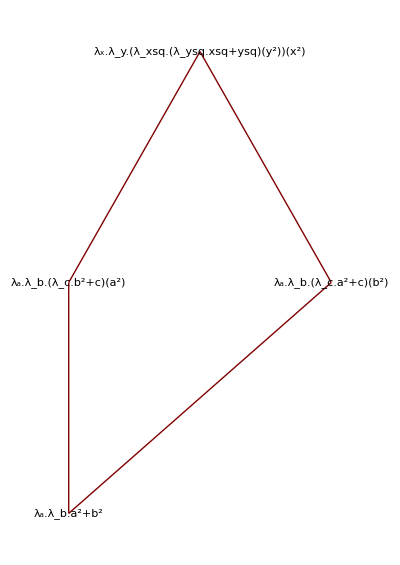

```mathematica
TreePlot[BetaNormalRules[expr],VertexLabeling->True]
```

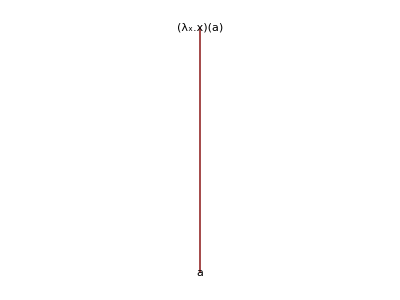

```mathematica
TreePlot[BetaNormalRules[LambdaFunction[x,x][a]],VertexLabeling->True]
```

When there are no possible reductions then we return an empty list:

```mathematica
BetaNormalRules[LambdaFunction[x,x]]
```

{}

An expression without normal form, running into a loop:

```mathematica
expr=LambdaFunction[x,x[x]][LambdaFunction[y,y[y]]]
```

(λ_x.x[x])[λ_y.y[y]]

```mathematica
BetaReduce[expr,x]
```

(λ_y.y[y])[λ_y.y[y]]

```mathematica
BetaNormal[expr]
```

BetaNormal::loop: Found beta reduction loop.

BetaNormal[(λ_x.x[x])[λ_y.y[y]]]

Another one, also with a loop:

```mathematica
expr=LambdaFunction[x,x[x][x]][LambdaFunction[y,y[y]]]
```

(λ_x.x[x][x])[λ_y.y[y]]

```mathematica
BetaNormal[expr]
```

BetaNormal::loop: Found beta reduction loop.

BetaNormal[(λ_x.x[x][x])[λ_y.y[y]]]

Another one, this time without a loop:

```mathematica
expr=LambdaFunction[x,x[x][x]][LambdaFunction[y,y[y][y]]]
```

(λ_x.x[x][x])[λ_y.y[y][y]]

```mathematica
BetaNormal[expr]
```

BetaNormal::itlim: Beta reduction reached maximum number of iterations 10.

BetaNormal[(λ_x.x[x][x])[λ_y.y[y][y]]]

```mathematica
BetaNormalRules[expr]
```

BetaNormalRules::itlim: Beta reduction reached maximum number of iterations 10.

BetaNormalRules[(λ_x.x[x][x])[λ_y.y[y][y]]]

```mathematica
$BetaReduceIterationLimit
```

10

From Lean: “An important feature of dependent type theory: every term has a computational behavior, and supports a notion of reduction, or normalization. In principle, two terms that reduce to the same value are called definitionally equal. They are considered `the same’ by the underlying logical framework, and Lean does its best to recognize and support these identifications.”

### Simply typed lambda calculus

Declarations (called statements in the Book):

```mathematica
Typed[a,α]
```

a:α

```mathematica
LambdaFunction[Typed[a,α],a]
```

λ_(a:α).a

```mathematica
LambdaFunction[Typed[a,b,c,α],a[b][c]]
```

λ_(a:α).λ_(b:α).λ_(c:α).a[b][c]

```mathematica
%//InputForm
```

LambdaFunction[Typed[a, α], LambdaFunction[Typed[b, α], LambdaFunction[Typed[c, α], a[b][c]]]]

The arrow type, with all parentheses (easy to eliminate):

```mathematica
ArrowType[α,β]
```

(α→β)

```mathematica
ArrowType[α,β,γ]
```

(α→(β→γ))

Type finding in a (possibly empty) context:

```mathematica
LambdaFunction[Typed[x,α],x]
```

λ_(x:α).x

```mathematica
Type[%]
```

(α→α)

```mathematica
LambdaFunction[Typed[x,α],y]
```

λ_(x:α).y

```mathematica
Type[%,{Typed[y,β]}]
```

(α→β)

Self-application is essentially forbidden in type theory:

```mathematica
Type[x[x][y],{Typed[x,α],Typed[y,β]}]
```

Type::comp: Cannot apply function x of type α on argument x of type α.

Type::comp: Cannot apply function x[x] of type Type[x[x],{x:α,y:β},{}] on argument y of type β.

Type[x[x][y],{x:α,y:β},{}]

A slightly nontrivial case:

```mathematica
F=LambdaFunction[Typed[h,ArrowType[α,β]],Typed[x,α],h[x]]
```

λ_(h:(α→β)).λ_(x:α).h[x]

```mathematica
Type[F]
```

((α→β)→(α→β))

```mathematica
expr=F[LambdaFunction[Typed[a,α],b]]
```

(λ_(h:(α→β)).λ_(x:α).h[x])[λ_(a:α).b]

```mathematica
Type[expr]
```

Type::comp: Cannot apply function λ_(h:(α→β)).λ_(x:α).h[x] of type ((α→β)→(α→β)) on argument λ_(a:α).b of type Π_(a:α).Type[b,{a:α},{}].

Type[(λ_(h:(α→β)).λ_(x:α).h[x])[λ_(a:α).b],{},{}]

```mathematica
Type[expr,{Typed[b,β]}]
```

(α→β)

```mathematica
BetaReduce[expr,h]
```

λ_(x:α).(λ_(a:α).b)[x]

```mathematica
Type[%,{Typed[b,β]}]
```

(α→β)

```mathematica
BetaReduce[expr,h,a]
```

λ_(x:α).b

```mathematica
Type[%,{Typed[b,β]}]
```

(α→β)

```mathematica
Clear[F]
```

### Calculus of constructions

In Simple Type Theory there is a clear distinction between terms and types. We want to eliminate that distinction by converting types into first-class citizens, like terms are.

In the Book there is a single type of types:

```mathematica
StarType
```

*_1

Following Lean, we separate an impredicative part of StarType, called PropType, the type of propositions:

```mathematica
PropType
```

Prop

Functions can take types as arguments. This is the “polymorphic identity”:

```mathematica
LambdaFunction[Typed[α,StarType],Typed[x,α],x]
```

λ_(α:*_1).λ_(x:α).x

It is a “dependent function”, in the sense that not only the image depends on the variable, but also the type of the image depends on the variable. The type of such a function is called a “dependent product” type:

```mathematica
Type[%]
```

Π_(α:*_1).(α→α)

```mathematica
%//InputForm
```

PiType[Typed[α, TypeU[1]], ArrowType[α, α]]

This would be StarType in the Book, but it is Type.{2} in Lean, so this is correct:

```mathematica
Type[%%]
```

*_2

An arrow type is just a particular case of a pi type:

```mathematica
{PiType[Typed[x,α],β],PiType[Typed[x,α],β[x]]}
```

{(α→β),Π_(x:α).β[x]}

```mathematica
%//InputForm
```

{ArrowType[α, β], PiType[Typed[x, α], β[x]]}

A pi type is a type with a dependency (which can be a type or not). That should not be confused with a function that returns a type (a “type constructor”):

```mathematica
LambdaFunction[Typed[α,StarType],ArrowType[α,α]]
```

λ_(α:*_1).(α→α)

```mathematica
Type[%]
```

(*_1→*_1)

Everything has a type, in particular types:

```mathematica
Type[%]
```

*_2

As a corner case:

```mathematica
Type[StarType]
```

*_2

### PropType & StarType

• Examples:

```mathematica
Type[ArrowType[PropType,PropType]]
```

*_1

```mathematica
Type[PiType[Typed[x,PropType],x]]
```

Prop

```mathematica
Type[PiType[Typed[x,StarType],x]]
```

*_2

```mathematica
Type[ArrowType[PiType[Typed[x,PropType],x],PiType[Typed[y,PropType],y]]]
```

Prop

```mathematica
Type[ArrowType[PropType,StarType]]
```

*_2

```mathematica
Type[ArrowType[StarType,PropType]]
```

*_2

```mathematica
Type[ArrowType[StarType,StarType]]
```

*_2

```mathematica
Type[ArrowType[StarType,a],{Typed[a,PropType]}]
```

Prop

```mathematica
Type[ArrowType[a,StarType],{Typed[a,PropType]}]
```

*_2

```mathematica
Type[ArrowType[TypeU[2],a],{Typed[a,PropType]}]
```

Prop

```mathematica
Type[ArrowType[a,TypeU[2]],{Typed[a,PropType]}]
```

*_3

### Independent products, tuples, and and sigma types

Examples with independent pairs and tuples:

```mathematica
Pair[x,y]
```

⟨x, y⟩

```mathematica
Type[%,{Typed[x,α],Typed[y,β]}]
```

(α×β)

```mathematica
%//InputForm
```

ProductType[α, β]

```mathematica
Tuple[x,y]//InputForm
```

Pair[x, y]

```mathematica
Tuple[x,y,z]
```

⟨x,y,z⟩

```mathematica
Type[%,{Typed[x,α],Typed[y,β],Typed[z,γ]}]
```

(α×β×γ)

The sigma type:

```mathematica
Pair[x,y[x]]
```

⟨x, y[x]⟩

```mathematica
Type[%,{Typed[x,α],Typed[y,PiType[Typed[z,α],β[z]]]}]
```

Σ_(x:α).β[x]

```mathematica
Pair[x,LambdaFunction[Typed[z,α],y[z]][x]]
```

⟨x, (λ_(z:α).y[z])[x]⟩

```mathematica
Type[%,{Typed[x,α],Typed[y,PiType[Typed[z,α],β[z]]]}]
```

Σ_(x:α).β[x]

Here the type expression loses the synchronization between both elements of the pair. See the intermediate sigma type constructed in the process:

```mathematica
Pair[x,x]
```

⟨x, x⟩

```mathematica
TracePrint[Type[%,{Typed[x,α]}],_SigmaType]
```

Σ_(x:α).Type[x,CalculusOfConstructions`Private`extendContext[{x:α},x:α],{}]

Σ_(x:α).α

(α×α)

### Term finding

We need to find an inhabitant of this type:

```mathematica
ArrowType[A,ArrowType[ArrowType[A,B],B]]
```

(A→((A→B)→B))

It clearly has this form (these are the flag contents):

```mathematica
LambdaFunction[Typed[x,A],Typed[f,ArrowType[A,B]],M]
```

λ_(x:A).λ_(f:(A→B)).M

```mathematica
LambdaFunction[Typed[x,A],Typed[f,ArrowType[A,B]],f[x]]
```

λ_(x:A).λ_(f:(A→B)).f[x]

```mathematica
Type[%]
```

(A→((A→B)→B))

```mathematica
%/.ArrowType->Implies
```

A⇒((A⇒B)⇒B)

```mathematica
TautologyQ[%]
```

True

Now try to find an inhabitant of this other type. There is none:

```mathematica
ArrowType[A,B]
```

(A→B)

Type-finding is decidable in the calculus of constructions, but term-finding is not, due to the presence of second order expressions (terms depending on terms mixed with types depending on terms or terms depending on types).

### The Curry-Howard correspondence

Amazingly a pair Typed[term, type] with Typed[type, StarType] can be interpreted as type representing a theorem (provably true proposition) and term containing a proof of it. Even more, if a given type can be shown not to correspond to any term expression, then that type represents a provably false proposition. Provability becomes equivalent to type matching.

Simultaneously, there is another interpretation of types as sets. The Book then marks the stars (for orientation only) with *_p and *_s for propositions and sets, respectively.

The connection is based on these two beautiful facts:
	• It is possible to construct all of high-order intuitionistic logic starting with connectives Implies (arrow) and ForAll (pi). (This cannot be done if we restrict to first-order logic only. See above.)
	• To get full classical logic, add the law of the excluded middle.
Note: Using only Implies we have the so-called “Minimal propositional logic”. With only Implies and ForAll we have “Minimal predicate logic”. Here “Minimal” means having only the logic signature, and no other variable domains.

Another point of view: how do we prove A ⇒ B ? The classical way would be to show that if A is true then B is also true. But we can avoid talking about truth and focus only on proofs: construct a function that takes as argument a proof of A and returns a proof of B. The proposition A ⇒ B can then be seen as the type of all functions that convert proofs of A into proofs of B. The underlying idea is then identifying a proposition with the collection of its proofs.

Trivial example:

```mathematica
Implies[B,Implies[A,B]]
```

B⇒(A⇒B)

```mathematica
TautologyQ[%]
```

True

```mathematica
LambdaFunction[Typed[x,B],Typed[y,A],x]
```

λ_(x:B).λ_(y:A).x

```mathematica
Type[%]
```

(B→(A→B))

```mathematica
ToLogic[%]
```

B⇒(A⇒B)

Nontrivial example:

```mathematica
context={Typed[S,A,StarType],Typed[P,ArrowType[S,StarType]]}
```

{S:*_1,A:*_1,P:(S→*_1)}

```mathematica
LambdaFunction[Typed[u,PiType[Typed[x,S],ArrowType[A,P[x]]]],Typed[a,A],Typed[y,S],u[y][a]]
```

λ_(u:Π_(x:S).(A→P[x])).λ_(a:A).λ_(y:S).u[y][a]

```mathematica
Type[%,context]
```

(Π_(x:S).(A→P[x])→(A→Π_(y:S).P[y]))

```mathematica
ToLogic[%]
```

ForAll[x,x∈S,A⇒P[x]]⇒(A⇒ForAll[y,y∈S,P[y]])

```mathematica
FromLogic[%]
```

(Π_(x:S).(A→P[x])→(A→Π_(y:S).P[y]))

WL’s TautologyQ does not yet handle first-order logic, only propositional logic:

```mathematica
Activate[%%]
```

∀_(x,x∈S)(A⇒P[x])⇒(A⇒∀_(y,y∈S)P[y])

```mathematica
{TautologyQ[%],Reduce[%]}
```

Reduce::elemc: Unable to resolve the domain or region membership condition x∈S.

{False,Reduce[∀_(x,x∈S)(A⇒P[x])⇒(A⇒∀_(y,y∈S)P[y])]}

Another nontrivial example:

```mathematica
context={Typed[S,StarType],Typed[P,ArrowType[S,PropType]],Typed[Q,ArrowType[S,StarType]]}
```

{S:*_1,P:(S→Prop),Q:(S→*_1)}

```mathematica
M=LambdaFunction[
Typed[u,FromLogic@Inactive[Exists][x,x∈S,FromLogic@Inactive[And][P[x],Q[x]]]],
Typed[α,PropType],
Typed[v,PiType[Typed[x,S],ArrowType[P[x],α]]],
u[α][LambdaFunction[
Typed[y,S],
Typed[w,FromLogic@Inactive[And][P[y],Q[y]]],v[y][w[P[y]][LambdaFunction[Typed[s,P[y]],Typed[t,Q[y]],s]]]]]]
```

λ_(u:Π_(α:Prop).(Π_(x:S).(Π_(α:Prop).((P[x]→(Q[x]→α))→α)→α)→α)).λ_(α:Prop).λ_(v:Π_(x:S).(P[x]→α)).u[α][λ_(y:S).λ_(w:Π_(α:Prop).((P[y]→(Q[y]→α))→α)).v[y][w[P[y]][λ_(s:P[y]).λ_(t:Q[y]).s]]]

```mathematica
Type[M,context]
```

(Π_(α:Prop).(Π_(x:S).(Π_(α:Prop).((P[x]→(Q[x]→α))→α)→α)→α)→Π_(α:Prop).(Π_(x:S).(P[x]→α)→α))

```mathematica
ToLogic[%]
```

Exists[x,x∈S,P[x]&&Q[x]]⇒Exists[x,x∈S,P[x]]

```mathematica
FromLogic[%]
```

(Π_(α:Prop).(Π_(x:S).(Π_(α:Prop).((P[x]→(Q[x]→α))→α)→α)→α)→Π_(α:Prop).(Π_(x:S).(P[x]→α)→α))

```mathematica
Clear[M,context]
```

### The law of the excluded middle

To obtain classical logic we need to extend λC adding the “axiom” of the excluded third (or middle):

```mathematica
not=Inactive[Not];
```

```mathematica
Inactive[Or][β,not[β]]
```

β||!β

```mathematica
FromLogic[%]
```

Π_(α:Prop).((β→α)→(((β→Π_(α:Prop).α)→α)→α))

```mathematica
ETaxiom=AlphaCanonical[PiType[Typed[β,PropType],%]]
```

Π_(α:Prop).Π_(β:Prop).((α→β)→(((α→Π_(γ:Prop).γ)→β)→β))

```mathematica
ToLogic[ETaxiom]
```

ForAll[α,α∈Prop,α||!α]

We cannot find a lambda term that obeys that, but we are going to assume that indeed there exists an inhabitant, called iET. See Book, page 147. Hence:

```mathematica
Typed[iET,ETaxiom]
```

iET:Π_(α:Prop).Π_(β:Prop).((α→β)→(((α→Π_(γ:Prop).γ)→β)→β))

Following the book, as an exercise we are going to show how this axiom implies the double negation law. The objective is to find this type:

```mathematica
DNlaw=AlphaCanonical[PiType[Typed[β,PropType],ArrowType[FromLogic[not[not[β]]],β]]]
```

Π_(α:Prop).(((α→Π_(β:Prop).β)→Π_(γ:Prop).γ)→α)

```mathematica
ToLogic[DNlaw]
```

ForAll[α,α∈Prop,!!α⇒α]

with the context given by the “axiom”:

```mathematica
context={Typed[iET,ETaxiom]}
```

{iET:Π_(α:Prop).Π_(β:Prop).((α→β)→(((α→Π_(γ:Prop).γ)→β)→β))}

We just follow the steps in the proof given by the Book (pages 147-150):

```mathematica
Type[LambdaFunction[Typed[β,PropType],iET[β]],context]
```

Π_(β:Prop).Π_(β:Prop).((β→β)→(((β→Π_(γ:Prop).γ)→β)→β))

```mathematica
Type[LambdaFunction[Typed[β,PropType],iET[β][β]],context]
```

Π_(β:Prop).((β→β)→(((β→Π_(γ:Prop).γ)→β)→β))

```mathematica
Type[LambdaFunction[Typed[β,PropType],iET[β][β][LambdaFunction[Typed[y,β],y]]],context]
```

Π_(β:Prop).(((β→Π_(γ:Prop).γ)→β)→β)

Finally this is an inhabitant of DNlaw:

```mathematica
LambdaFunction[Typed[β,PropType],Typed[x,FromLogic[not[not[β]]]],iET[β][β][LambdaFunction[Typed[y,β],y]][LambdaFunction[Typed[z,FromLogic[not[β]]],x[z][β]]]]
```

λ_(β:Prop).λ_(x:((β→Π_(α:Prop).α)→Π_(α:Prop).α)).iET[β][β][λ_(y:β).y][λ_(z:(β→Π_(α:Prop).α)).x[z][β]]

It does have the type we were looking for:

```mathematica
AlphaCanonical[Type[%,context]]===DNlaw
```

True

### Definitions

#### General

From Lean: “declaring constants is a good way to postulate new objects to experiment with, but most of the time what we really want to do is define new objects in Lean and prove things about them.”

A definition: d is the definiendum and r is the definiens:

```mathematica
Defined[d,r]
```

d := r

Add a context. This is very similar to a judgement (in which the right turnstile gets replaced by the right triangle):

```mathematica
Math[Γ,Defined[d,r]]
```

Γ ⊳ d := r

Add an environment.

```mathematica
Math[Δ,Γ,Defined[d,r]]
```

Δ; Γ ⊳ d := r

We can make explicit the type of the definiens (hence of the definiendum), though in principle it should be possible to infer it from Γ and the y expression.

```mathematica
Math[Δ,Γ,Defined[d,Typed[r,β]]]
```

Δ; Γ ⊳ d := r:β

In Lean the type is provided with the definiendum, not with the definiens. Something like d : α := r .

Now we need to decide how to represent the presence of parameters. I think there are two natural ways to do it.

```mathematica
Math[Δ,Typed[p,α],Defined[c[p],Typed[r,β]]]
```

Δ; p:α ⊳ c[p] := r:β

```mathematica
Math[Δ,{},Defined[c,Typed[LambdaFunction[Typed[p,α],r],ArrowType[α,β]]]]
```

Δ; {} ⊳ c := λ_(p:α).r:(α→β)

The former case may be nicer for a document, but it is less clear how to use it. Comparing with WL, the context determines the pattern objects. The latter approach is simpler to use, because it works basically via β-reduction. The Book (page 184) says that the latter method may be more restricted due to limitations in the types that are allowed by the lambda calculus. I don’t understand that.

Lean also allows both styles of defining a function:

	definition f : A ->B := fun x, body
	definition f (x : A) : B := body

We could do, in parallel:

	Typed[f, A -> B] := Function[x, body]
	Typed[f[ Typed[x_, A] ], B] := body

or even

	f[Typed[x_, A]] := Typed[body, B]
	f := Function[Typed[x, A], Typed[body, B]]

How do we work with multiple parameters? For some reason, the Book prefers to use tuples of parameters instead of separated arguments. So this forces us to introduce tuples and independent product types.

```mathematica
Math[Δ,{Typed[p1,α1],Typed[p2,α2]},Defined[c[Pair[p1,p2]],Typed[r,β]]]
```

Δ; {p1:α1,p2:α2} ⊳ c[⟨p1, p2⟩] := r:β

There are two types of definitions: “descriptive” definitions, in which there is an explicit definiens, and “primitive” definitions. Following the Book, we denote primitive definitions using a special definiens. Note that we can still specify its type:

```mathematica
Math[Δ,Γ,Defined[d,Typed[NullDefiniens,β]]]
```

Δ; Γ ⊳ d := ∐:β

We may want to have a “local definition” construction, very much like With. In Lean we can have things like

	check let y := n + n in y * y
	
	check let y := n + n, z := y + y in z * z

Note in this second case how z depends on y, which was previously defined in the same let-call.

#### Examples in page 201 of the Book

Examples in the page 201 of the Book:

```mathematica
environment={
Defined[a[x,y],Typed[x^2+y^2,Integers]],
Defined[b[x,y],Typed[2x y,Integers]],
Defined[c[x,y],Typed[a[x,y]+b[x,y],Integers]],
Defined[lemma[x,y],Typed[Equal[c[x,y],(x+y)^2],PropType]]
}
```

{a[x,y] := x^2+y^2:ℤ,b[x,y] := 2 x y:ℤ,c[x,y] := a[x,y]+b[x,y]:ℤ,lemma[x,y] := c[x,y]==(x+y)^2:Prop}

```mathematica
context={Typed[x,Integers],Typed[y,Integers]}
```

{x:ℤ,y:ℤ}

First example:

```mathematica
expr=a[a[x,x],a[y,y]]
```

a[a[x,x],a[y,y]]

```mathematica
Type[expr,context,environment]
```

ℤ

Note that it is checking all internals, and not just using the fact that we know that the external a[...] has type Integers. For example, change one of the internal parts. Note also how Type falls back to the delta reduction, and then it gets stuck when it finds the WL head Plus:

```mathematica
Type[a[a[x,x],a[y,z]],context,environment]
```

Defined::incomp: Incompatible types of argument lists {y,z} and {x,y}.

Defined::incomp: Incompatible types of argument lists {a[x,x],a[y,z]} and {x,y}.

Type[4 x^4+(y^2+z^2)^2,{x:ℤ,y:ℤ},{}]

```mathematica
DeltaReduce[expr,environment,a]
```

4 x^4+4 y^4

```mathematica
DeltaNormal[expr,environment]
```

4 x^4+4 y^4

Another example in page 201 of the Book:

```mathematica
expr=lemma[u,v]
```

lemma[u,v]

```mathematica
FoldList[DeltaReduce[#1,environment,#2]&,expr,{lemma,c,b,a}]//Column
```

lemma[u,v]
c[u,v]==(u+v)^2
a[u,v]+b[u,v]==(u+v)^2
2 u v+a[u,v]==(u+v)^2
u^2+2 u v+v^2==(u+v)^2

```mathematica
DeltaNormal[expr,environment]
```

u^2+2 u v+v^2==(u+v)^2

The context is not valid here:

```mathematica
Type[expr,context,environment]
```

Defined::incomp: Incompatible types of argument lists {u,v} and {x,y}.

Type[u^2+2 u v+v^2==(u+v)^2,{x:ℤ,y:ℤ},{}]

So we need to type u and v:

```mathematica
Type[expr,Join[context,{Typed[u,v,Integers]}],environment]
```

Prop

#### Examples with Math

Suppose we want to define the predicate “increasing” for a real function, as in page 169 of the Book. We can write either of these:

```mathematica
Math[Typed[f,ArrowType[Reals,Reals]],Defined[increasing[f],Inactive[ForAll][{x,y},x∈Reals&&y∈Reals,Inactive[Implies][x<y,f[x]<f[y]]]]]
```

f:(ℝ→ℝ) ⊳ increasing[f] := ForAll[{x,y},x∈ℝ&&y∈ℝ,x<y⇒f[x]<f[y]]

```mathematica
Defined[increasing,LambdaFunction[Typed[f,ArrowType[Reals,Reals]],Inactive[ForAll][{x,y},x∈Reals&&y∈Reals,Inactive[Implies][x<y,f[x]<f[y]]]]]
```

increasing := λ_(f:(ℝ→ℝ)).ForAll[{x,y},x∈ℝ&&y∈ℝ,x<y⇒f[x]<f[y]]

Examples in page 174.

```mathematica
Math[{Typed[S1,StarType],Typed[R1,ArrowType[ProductType[S1,S1],StarType]]},Defined[reflexive[Pair[S1,R1]],Inactive[ForAll][x1,x1∈S1,R1[Pair[x1,x1]]]]]
```

{S1:*_1,R1:((S1×S1)→*_1)} ⊳ reflexive[⟨S1, R1⟩] := ForAll[x1,x1∈S1,R1[⟨x1, x1⟩]]

```mathematica
Math[{Typed[S2,StarType],Typed[R2,ArrowType[ProductType[S2,S2],StarType]]},Defined[antisymmetric[Pair[S2,R2]],Inactive[ForAll][{x2,y2},x2∈S2&&y2∈S2,Inactive[Implies][Inactive[And][R2[Pair[x2,y2]],R2[Pair[y2,x2]]],Inactive[Equal][x2,y2]]]]]
```

{S2:*_1,R2:((S2×S2)→*_1)} ⊳ antisymmetric[⟨S2, R2⟩] := ForAll[{x2,y2},x2∈S2&&y2∈S2,R2[⟨x2, y2⟩]&&R2[⟨y2, x2⟩]⇒x2==y2]

```mathematica
Math[{Typed[S3,StarType],Typed[R3,ArrowType[ProductType[S3,S3],StarType]]},Defined[transitive[Pair[S3,R3]],Inactive[ForAll][{x3,y3,z3},x3∈S3&&y3∈S3&&z3∈S3,Inactive[Implies][Inactive[And][R3[Pair[x3,y3]],R3[Pair[y3,z3]]],R3[Pair[x3,z3]]]]]]
```

{S3:*_1,R3:((S3×S3)→*_1)} ⊳ transitive[⟨S3, R3⟩] := ForAll[{x3,y3,z3},x3∈S3&&y3∈S3&&z3∈S3,R3[⟨x3, y3⟩]&&R3[⟨y3, z3⟩]⇒R3[⟨x3, z3⟩]]

The forth definition can be given after the previous three. Note also that And is not assumed to be associative

```mathematica
Math[{Typed[S4,StarType],Typed[R4,ArrowType[ProductType[S4,S4],StarType]]},Defined[partiallyordered[Pair[S4,R4]],Inactive[And][reflexive[Pair[S4,R4]],Inactive[And][antisymmetric[Pair[S4,R4]],transitive[Pair[S4,R4]]]]]
]
```

{S4:*_1,R4:((S4×S4)→*_1)} ⊳ partiallyordered[⟨S4, R4⟩] := reflexive[⟨S4, R4⟩]&&(antisymmetric[⟨S4, R4⟩]&&transitive[⟨S4, R4⟩])

As in page 175 of the Book, we can also insert an assumption in the context, called u. We can see u as the “assumed proof” of the proposition partiallyordered[Pair[S, R]].

```mathematica
Math[{Typed[S,StarType],Typed[R,ArrowType[ProductType[S,S],StarType]],Typed[u,partiallyordered[Pair[S,R]]],Typed[m,S]},Defined[minimalelement[Tuple[S,R,u,m]],Typed[Inactive[ForAll][x,x∈S,Inactive[Implies][R[Pair[x,m]],Inactive[Equal][x,m]]],StarType]]]
```

{S:*_1,R:((S×S)→*_1),u:partiallyordered[⟨S, R⟩],m:S} ⊳ minimalelement[⟨S,R,u,m⟩] := ForAll[x,x∈S,R[⟨x, m⟩]⇒x==m]:*_1

We can also name proofs. Here we define the constant function f, taking the triple m, n, u, where m and n are positive naturals and u takes a proof U of the fact that m and n are coprime numbers. That is defined as a proof (abbreviated here as formalproof) of the Bezout lemma:

```mathematica
Math[{Typed[m,n,PositiveIntegers],Typed[u,coprime[Pair[m,n]]]},Defined[p[Tuple[m,n,u]],Typed[formalproof,Inactive[Exists][{x,y},x∈Integers&&y∈Integers,Inactive[Equal][m x+n y,1]]]]]
```

{m:ℕ^+,n:ℕ^+,u:coprime[⟨m, n⟩]} ⊳ p[⟨m,n,u⟩] := formalproof:Exists[{x,y},x∈ℤ&&y∈ℤ,m x+n y==1]

### Judgements and derivation rules

A judgement asserts that a given statement is derivable from a context (a set of declarations of different variables). In other words, a judgement asserts that from a list of type declarations we can derive other type declarations.

In a judgement the variables of the declarations of the context are considered bound. They bind the free variables of the declarations s:

```mathematica
Math[Γ,s]
```

Γ ⊢ s

A judgement can also have an environment Δ of definitions (see Definition 9.2.1 of the Book).This can be called an “extended judgement”. An environment is a sorted list of definitions. Defined constants may appear in later definitions of the same environment, but not before.

```mathematica
Math[Δ,Γ,Typed[M,N]]
```

Δ; Γ ⊢ M:N

A derivation rule contains premises and a conclusion.

```mathematica
DerivationRule[{a,b},c]
```

(a, b)/c

```mathematica
InputForm[%]
```

DerivationRule[{a, b}, c]

For example, these are the three derivation rules of the simply typed lambda calculus:

```mathematica
DerivationRule[{},Math[Γ,Typed[x,σ]]]
```

/(Γ ⊢ x:σ)

```mathematica
DerivationRule[{Math[Γ,Typed[M,ArrowType[σ,τ]]],Math[Γ,Typed[L,σ]]},Math[Γ,Typed[M[L],τ]]]
```

(Γ ⊢ M:(σ→τ), Γ ⊢ L:σ)/(Γ ⊢ M[L]:τ)

```mathematica
DerivationRule[{Math[{Γ,Typed[x,σ]},Typed[M,τ]]},Math[Γ,Typed[LambdaFunction[Typed[x,σ],M],ArrowType[σ,τ]]]]
```

({Γ,x:σ} ⊢ M:τ)/(Γ ⊢ λ_(x:σ).M:(σ→τ))

## Exercises of Nederpelt & Geuvers

### Chapter 1

[Book, pages 29--31].

#### Exercise 1.2

```mathematica
term=LambdaFunction[x,x[LambdaFunction[x,x]]]
```

λ_x.x[λ_x.x]

```mathematica
LambdaFunction[y,y[LambdaFunction[x,x]]]≃term
```

True

```mathematica
Not[LambdaFunction[y,y[LambdaFunction[x,y]]]≃term]
```

True

```mathematica
Not[LambdaFunction[y,y[LambdaFunction[y,x]]]≃term]
```

True

```mathematica
Clear[term]
```

#### Exercise 1.3

```mathematica
LambdaFunction[x,x[LambdaFunction[z,y]]]≃LambdaFunction[z,z[LambdaFunction[z,y]]]
```

True

#### Exercise 1.4

```mathematica
U=LambdaFunction[z,z[x][z]][LambdaFunction[y,x[y]][x]]
```

(λ_z.z[x][z])[(λ_y.x[y])[x]]

```mathematica
Subterms[U]
```

{z,x,z[x],z,z[x][z],λ_z.z[x][z],x,y,x[y],λ_y.x[y],x,(λ_y.x[y])[x],(λ_z.z[x][z])[(λ_y.x[y])[x]]}

```mathematica
FreeVariables[U]
```

{x}

```mathematica
LambdaFunction[y,y[x][y]][LambdaFunction[z,x[z]][x]]≃U
```

True

```mathematica
Not[LambdaFunction[x,x[y][x]][LambdaFunction[z,y[z]][y]]≃U]
```

True

```mathematica
LambdaFunction[y,y[x][y]][LambdaFunction[y,x[y]][x]]≃U
```

True

```mathematica
Not[LambdaFunction[v,v[x][v]][LambdaFunction[u,u[v]][x]]≃U]
```

True

```mathematica
Clear[U]
```

#### Exercise 1.5

```mathematica
ReplaceFree[LambdaFunction[x,y[LambdaFunction[y,x[y]]]],y->LambdaFunction[z,z[x]]]
```

λ_a.(λ_z.z[x])[λ_y.a[y]]

```mathematica
ReplaceFree[ReplaceFree[x[y][z],x->y],y->z]
```

z[z][z]

```mathematica
ReplaceFree[ReplaceFree[LambdaFunction[x,x[y][z]],x->y],y->z]
```

λ_x.x[z][z]

```mathematica
ReplaceFree[LambdaFunction[y,y[y][x]],x->y[z]]
```

λ_a.a[a][y[z]]

#### Exercise 1.8

```mathematica
BetaReduce[LambdaFunction[x,x[x]][y],x]
```

y[y]

```mathematica
BetaReduce[LambdaFunction[x,y,y[x]][x][x],x,y]
```

x[x]

#### Exercise 1.9

```mathematica
Kf=LambdaFunction[x,y,x]
```

λ_x.λ_y.x

```mathematica
Sf=LambdaFunction[x,y,z,x[z][y[z]]]
```

λ_x.λ_y.λ_z.x[z][y[z]]

```mathematica
B=Sf[Kf[Sf]][Kf]
```

(λ_x.λ_y.λ_z.x[z][y[z]])[(λ_x.λ_y.x)[λ_x.λ_y.λ_z.x[z][y[z]]]][λ_x.λ_y.x]

```mathematica
BetaReduce[Kf[P][Q],x,y]
```

P

```mathematica
BetaReduce[Sf[P][Q][R],x,y,z]
```

P[R][Q[R]]

```mathematica
BetaReduce[Sf[Kf][Kf],x,y,x,y]
```

λ_z.z

```mathematica
BetaReduce[B[U][V][W],x,y,z,x,y,x,y,z,y]
```

U[V[W]]

```mathematica
BetaReduce[Sf[Sf][Sf][Kf][Kf],x,y,z,x,y,z,x,y]
```

λ_x.λ_y.x

```mathematica
BetaReduce[Sf[Kf][Kf][Kf],x,y,z,x,y]
```

λ_x.λ_y.x

```mathematica
Clear[Kf,Sf,B]
```

#### Exercise 1.10

```mathematica
zero=LambdaFunction[f,x,x];
one=LambdaFunction[f,x,f[x]];
two=LambdaFunction[f,x,f[f[x]]];
add=LambdaFunction[m,n,f,x,m[f][n[f][x]]];
mult=LambdaFunction[m,n,f,x,m[n[f]][x]];
```

```mathematica
add[one][one]
```

(λ_m.λ_n.λ_f.λ_x.m[f][n[f][x]])[λ_f.λ_x.f[x]][λ_f.λ_x.f[x]]

```mathematica
BetaReduce[%,m,n,f,x,x]===two
```

True

```mathematica
BetaReduce[mult[one][zero],m,n,f,f,x,x]===zero
```

True

#### Exercise 1.11

```mathematica
suc=LambdaFunction[m,f,x,f[m[f][x]]]
```

λ_m.λ_f.λ_x.f[m[f][x]]

```mathematica
BetaReduce[suc[zero],m,f,x]===one
```

True

```mathematica
BetaReduce[suc[one],m,f,x]===two
```

True

#### Exercise 1.12

```mathematica
true=LambdaFunction[x,y,x];
false=LambdaFunction[x,y,y];
not=LambdaFunction[z,z[false][true]];
```

```mathematica
BetaReduce[not[true],z,x,y]===false
```

True

```mathematica
BetaReduce[not[false],z,x,y]===true
```

True

#### Exercise 1.13

```mathematica
iszero=LambdaFunction[z,z[LambdaFunction[x,false]][true]]
```

λ_z.z[λ_x.λ_x.λ_y.y][λ_x.λ_y.x]

```mathematica
BetaReduce[iszero[zero],z,f,x]===true
```

True

```mathematica
BetaReduce[iszero[one],z,f,x,x]===false
```

True

#### Exercise 1.14

```mathematica
ifthenelse=LambdaFunction[x,x[u][v]]
```

λ_x.x[u][v]

```mathematica
BetaReduce[ifthenelse[true],x,x,y]
```

u

```mathematica
BetaReduce[ifthenelse[false],x,x,y]
```

v

#### Exercise 1.19

Turing fixed point combinator:

```mathematica
U=LambdaFunction[z,x,x[z[z][x]]]
Z=U[U]
```

λ_z.λ_x.x[z[z][x]]

(λ_z.λ_x.x[z[z][x]])[λ_z.λ_x.x[z[z][x]]]

```mathematica
BetaReduce[Z[M],z,x]===M[Z[M]]
```

True

```mathematica
Clear[U,Z]
```

### Chapter 2

[Book, pages 66--68].

#### Exercise 2.1

```mathematica
Type[x[x][y],{Typed[x,α],Typed[y,β]}]
```

Type::comp: Cannot apply function x of type α on argument x of type α.

Type::comp: Cannot apply function x[x] of type Type[x[x],{x:α,y:β},{}] on argument y of type β.

Type[x[x][y],{x:α,y:β},{}]

#### Exercise 2.2

```mathematica
With[{context={Typed[x,α],Typed[f,ArrowType[α,α]]}},
{Type[zero,context],Type[one,context],Type[two,context]}
]
```

{((α→α)→(α→α)),((α→α)→(α→α)),((α→α)→(α→α))}

#### Exercise 2.3

```mathematica
Kf=LambdaFunction[x,y,x]
```

λ_x.λ_y.x

```mathematica
Sf=LambdaFunction[x,y,z,x[z][y[z]]]
```

λ_x.λ_y.λ_z.x[z][y[z]]

```mathematica
Type[Kf,{Typed[x,α],Typed[y,β]}]
```

(α→(β→α))

```mathematica
Type[Sf,{Typed[z,α],Typed[x,ArrowType[α,β,γ]],Typed[y,ArrowType[α,β]]}]
```

((α→(β→γ))→((α→β)→(α→γ)))

```mathematica
BetaReduce[Sf[x][y][z],x,y,z]
```

x[z][y[z]]

```mathematica
Type[%,{Typed[z,α],Typed[x,ArrowType[α,β,γ]],Typed[y,ArrowType[α,β]]}]
```

γ

```mathematica
Clear[Kf,Sf]
```

#### Exercise 2.4

a)

```mathematica
LambdaFunction[x,y,z,x[y[z]]]
```

λ_x.λ_y.λ_z.x[y[z]]

```mathematica
Type[%,{Typed[z,α],Typed[y,ArrowType[α,β]],Typed[x,ArrowType[β,γ]]}]
```

((β→γ)→((α→β)→(α→γ)))

Alternatively:

```mathematica
LambdaFunction[Typed[x,ArrowType[β,γ]],Typed[y,ArrowType[α,β]],Typed[z,α],x[y[z]]]
```

λ_(x:(β→γ)).λ_(y:(α→β)).λ_(z:α).x[y[z]]

```mathematica
Type[%]
```

((β→γ)→((α→β)→(α→γ)))

b)

```mathematica
LambdaFunction[x,y,z,y[x[z]][x]]
```

λ_x.λ_y.λ_z.y[x[z]][x]

```mathematica
Type[%,{Typed[z,α],Typed[x,ArrowType[α,β]],Typed[y,ArrowType[β,ArrowType[ArrowType[α,β],γ]]]}]
```

((α→β)→((β→((α→β)→γ))→(α→γ)))

```mathematica
LambdaFunction[Typed[x,ArrowType[α,β]],Typed[y,ArrowType[β,ArrowType[ArrowType[α,β],γ]]],Typed[z,α],y[x[z]][x]]
```

λ_(x:(α→β)).λ_(y:(β→((α→β)→γ))).λ_(z:α).y[x[z]][x]

```mathematica
Type[%]
```

((α→β)→((β→((α→β)→γ))→(α→γ)))

#### Exercise 2.5

This example is very good. It shows how the type checking can be used to show that an expression is not legal:

a)

```mathematica
LambdaFunction[x,y,x[LambdaFunction[z,y]][y]]
```

λ_x.λ_y.x[λ_z.y][y]

```mathematica
Type[%,{Typed[x,ArrowType[ArrowType[ζ,τ],ArrowType[τ,ρ]]],Typed[y,τ],Typed[z,ζ]}]
```

(((ζ→τ)→(τ→ρ))→(τ→ρ))

b)

```mathematica
LambdaFunction[x,y,x[LambdaFunction[z,x]][y]]
```

λ_x.λ_y.x[λ_z.x][y]

```mathematica
Type[%,{Typed[x,ArrowType[ArrowType[ζ,α],ArrowType[τ,γ]]],Typed[y,τ],Typed[z,ζ]}]
```

Type::comp: Cannot apply function x of type ((ζ→α)→(τ→γ)) on argument λ_z.x of type (ζ→((ζ→α)→(τ→γ))).

Type::comp: Cannot apply function x[λ_z.x] of type Type[x[λ_z.x],{x:((ζ→α)→(τ→γ)),y:τ,z:ζ},{}] on argument y of type τ.

(((ζ→α)→(τ→γ))→(τ→Type[x[λ_z.x][y],{x:((ζ→α)→(τ→γ)),y:τ,z:ζ},{}]))

In this case x is acting in two different forms, so it is not possible to assign types in a consistent way. Basically the problem is “solving” for α in the inconsistency above.

#### Exercise 2.6

```mathematica
LambdaFunction[Typed[x,ArrowType[ArrowType[α,β],α]],x[LambdaFunction[Typed[z,α],y]]]
```

λ_(x:((α→β)→α)).x[λ_(z:α).y]

```mathematica
Type[%]
```

Type::comp: Cannot apply function x of type ((α→β)→α) on argument λ_(z:α).y of type Π_(z:α).Type[y,{z:α,x:((α→β)→α)},{}].

Π_(x:((α→β)→α)).Type[x[λ_(z:α).y],{x:((α→β)→α)},{}]

Hence we just need to restrict the type of y:

```mathematica
Type[%%,{Typed[y,β]}]
```

(((α→β)→α)→α)

#### Exercise 2.8

```mathematica
term=LambdaFunction[x,y,y[LambdaFunction[z,y[x]]]]
```

λ_x.λ_y.y[λ_z.y[x]]

```mathematica
Type[term,{Typed[x,σ]}]
```

Type::comp: Cannot apply function y of type Type[y,{x:σ},{}] on argument x of type σ.

Type::comp: Cannot apply function y of type Type[y,{x:σ},{}] on argument λ_z.y[x] of type (Type[z,{x:σ},{}]→Type[y[x],{x:σ},{}]).

(σ→(Type[y,{x:σ},{}]→Type[y[λ_z.y[x]],{x:σ},{}]))

```mathematica
Type[term,{Typed[x,σ],Typed[y,ArrowType[σ,β]],Typed[z,γ]}]
```

Type::comp: Cannot apply function y of type (σ→β) on argument λ_z.y[x] of type (γ→β).

(σ→((σ→β)→Type[y[λ_z.y[x]],{x:σ,y:(σ→β),z:γ},{}]))

```mathematica
Type[term,{Typed[x,ArrowType[γ,β]],Typed[y,ArrowType[ArrowType[γ,β],β]],Typed[z,γ]}]
```

((γ→β)→(((γ→β)→β)→β))

```mathematica
Clear[term]
```

#### Exercise 2.10

```mathematica
x[z][y[z]]
```

x[z][y[z]]

```mathematica
Type[%,{Typed[x,ArrowType[γ,ArrowType[β,δ]]],Typed[y,ArrowType[γ,β]],Typed[z,γ]}]
```

δ

```mathematica
LambdaFunction[x,x[y[z]]]
```

λ_x.x[y[z]]

```mathematica
Type[%,{Typed[x,ArrowType[ArrowType[α,β],β]],Typed[y,ArrowType[γ,ArrowType[α,β]]],Typed[z,γ]}]
```

(((α→β)→β)→β)

```mathematica
LambdaFunction[y,z,z[x[y][y]]]
```

λ_y.λ_z.z[x[y][y]]

```mathematica
Type[%,{Typed[y,α],Typed[z,ArrowType[β,γ]],Typed[x,ArrowType[α,ArrowType[α,β]]]}]
```

(α→((β→γ)→γ))

```mathematica
LambdaFunction[x,y[x[z]][z]]
```

λ_x.y[x[z]][z]

```mathematica
Type[%,{Typed[x,ArrowType[α,β]],Typed[z,α],Typed[y,ArrowType[β,ArrowType[α,γ]]]}]
```

((α→β)→γ)

#### Exercise 2.11

```mathematica
LambdaFunction[x,y,z,x[y][y]]
```

λ_x.λ_y.λ_z.x[y][y]

```mathematica
Type[%,{Typed[y,α],Typed[x,ArrowType[α,α,γ]],Typed[z,β]}]
```

((α→(α→γ))→(α→(β→γ)))

```mathematica
LambdaFunction[x,y,z,y[x[y]]]
```

λ_x.λ_y.λ_z.y[x[y]]

```mathematica
Type[%,{Typed[x,ArrowType[ArrowType[α,γ],α]],Typed[y,ArrowType[α,γ]],Typed[z,β]}]
```

(((α→γ)→α)→((α→γ)→(β→γ)))

#### Exercise 2.12

This exercise is also very good, as it shows the complexity of the process of finding an inhabitant, i.e., a proof.

We need a term of type α constructed from from a function ((α->β)->α) and a function (α->(α->β)). I don’t see how this is possible without introducing a constant or variable of type α...

```mathematica
LambdaFunction[Typed[x,ArrowType[ArrowType[α,β],α]],Typed[y,ArrowType[α,α,β]],M]
```

λ_(x:((α→β)→α)).λ_(y:(α→(α→β))).M

```mathematica
Type[%]
```

Π_(x:((α→β)→α)).Π_(y:(α→(α→β))).Type[M,{y:(α→(α→β)),x:((α→β)→α)},{}]

In fact, looking at the solution, this is what is done, with a function of a variable z of type α:

```mathematica
%/.M->x[LambdaFunction[Typed[z,α],y[z][z]]]
```

(((α→β)→α)→((α→(α→β))→α))

Second part:

```mathematica
LambdaFunction[Typed[x,ArrowType[ArrowType[α,β],α]],Typed[y,ArrowType[α,α,β]],M]
```

λ_(x:((α→β)→α)).λ_(y:(α→(α→β))).M

```mathematica
Type[%]
```

Π_(x:((α→β)→α)).Π_(y:(α→(α→β))).Type[M,{y:(α→(α→β)),x:((α→β)→α)},{}]

```mathematica
%/.M->y[x[LambdaFunction[Typed[z,α],y[z][z]]]][x[LambdaFunction[Typed[z,α],y[z][z]]]]
```

(((α→β)→α)→((α→(α→β))→β))

#### Exercise 2.13

```mathematica
LambdaFunction[r,s,x[s][r[s]]]
```

λ_r.λ_s.x[s][r[s]]

```mathematica
Type[%,{Typed[r,ArrowType[α,β]],Typed[s,α],Typed[x,ArrowType[α,β,γ]]}]
```

((α→β)→(α→γ))

```mathematica
LambdaFunction[r,s,x[r][s[r]][r]]
```

λ_r.λ_s.x[r][s[r]][r]

```mathematica
Type[%,{Typed[r,α],Typed[s,ArrowType[α,β]],Typed[x,ArrowType[α,β,α,γ]]}]
```

(α→((α→β)→γ))

```mathematica
LambdaFunction[r,s,x[LambdaFunction[z,r[s[z]]]]]
```

λ_r.λ_s.x[λ_z.r[s[z]]]

```mathematica
Type[%,{Typed[r,ArrowType[α,γ]],Typed[s,ArrowType[β,α]],Typed[z,β],Typed[x,ArrowType[ArrowType[β,γ],γ]]}]
```

((α→γ)→((β→α)→γ))

#### Exercise 2.14

```mathematica
LambdaFunction[r,s,M]
```

λ_r.λ_s.M

```mathematica
LambdaFunction[r,s,x[LambdaFunction[t,s]][r]]
```

λ_r.λ_s.x[λ_t.s][r]

```mathematica
Type[%,{Typed[r,α],Typed[t,α],Typed[s,β],Typed[x,ArrowType[ArrowType[α,β],α,γ]]}]
```

(α→(β→γ))

### Chapter 3

[Book, pages 82--84].

#### Exercise 3.4

```mathematica
LambdaFunction[Typed[α,β,StarType],Typed[f,ArrowType[α,α]],Typed[g,ArrowType[α,β]],Typed[x,α],g[f[f[x]]]]
```

λ_(α:*_1).λ_(β:*_1).λ_(f:(α→α)).λ_(g:(α→β)).λ_(x:α).g[f[f[x]]]

```mathematica
%[nat][bool]
```

(λ_(α:*_1).λ_(β:*_1).λ_(f:(α→α)).λ_(g:(α→β)).λ_(x:α).g[f[f[x]]])[nat][bool]

```mathematica
BetaReduce[%,α]
```

(λ_(β:*_1).λ_(f:(nat→nat)).λ_(g:(nat→β)).λ_(x:nat).g[f[f[x]]])[bool]

```mathematica
BetaReduce[%,β]
```

λ_(f:(nat→nat)).λ_(g:(nat→bool)).λ_(x:nat).g[f[f[x]]]

```mathematica
Type[%]
```

((nat→nat)→((nat→bool)→(nat→bool)))

#### Exercise 3.6

```mathematica
LambdaFunction[Typed[α,β,StarType],Typed[x,ArrowType[nat,α]],Typed[y,ArrowType[α,nat,β]],Typed[z,nat],y[x[z]][z]]
```

λ_(α:*_1).λ_(β:*_1).λ_(x:(nat→α)).λ_(y:(α→(nat→β))).λ_(z:nat).y[x[z]][z]

```mathematica
Type[%]
```

Π_(α:*_1).Π_(β:*_1).((nat→α)→((α→(nat→β))→(nat→β)))

```mathematica
LambdaFunction[Typed[δ,StarType],Typed[x,ArrowType[ArrowType[α,γ],δ]],Typed[y,ArrowType[α,β]],Typed[z,ArrowType[β,γ]],x[LambdaFunction[Typed[r,α],z[y[r]]]]]
```

λ_(δ:*_1).λ_(x:((α→γ)→δ)).λ_(y:(α→β)).λ_(z:(β→γ)).x[λ_(r:α).z[y[r]]]

```mathematica
Type[%]
```

Π_(δ:*_1).(((α→γ)→δ)→((α→β)→((β→γ)→δ)))

```mathematica
LambdaFunction[Typed[α,β,γ,StarType],Typed[x,ArrowType[α,ArrowType[ArrowType[β,α],γ]]],Typed[y,α],x[y][LambdaFunction[Typed[z,β],y]]]
```

λ_(α:*_1).λ_(β:*_1).λ_(γ:*_1).λ_(x:(α→((β→α)→γ))).λ_(y:α).x[y][λ_(z:β).y]

```mathematica
Type[%]
```

Π_(α:*_1).Π_(β:*_1).Π_(γ:*_1).((α→((β→α)→γ))→(α→γ))

#### Exercise 3.10

```mathematica
LambdaFunction[
Typed[x,PiType[Typed[α,StarType],ArrowType[α,α]]],
x[ArrowType[σ,σ]][x[σ]]
]
```

λ_(x:Π_(α:*_1).(α→α)).x[(σ→σ)][x[σ]]

```mathematica
Type[%,{Typed[σ,StarType]}]
```

(Π_(α:*_1).(α→α)→(σ→σ))

#### Exercise 3.12

This exercise is very impressive. In particular the coding of Nat:

```mathematica
Nat=PiType[Typed[α,StarType],ArrowType[ArrowType[α,α],α,α]]
```

Π_(α:*_1).((α→α)→(α→α))

```mathematica
Zero=LambdaFunction[Typed[α,StarType],Typed[f,ArrowType[α,α]],Typed[x,α],x]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).x

```mathematica
One=LambdaFunction[Typed[α,StarType],Typed[f,ArrowType[α,α]],Typed[x,α],f[x]]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x]

```mathematica
Two=LambdaFunction[Typed[α,StarType],Typed[f,ArrowType[α,α]],Typed[x,α],f[f[x]]]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[f[x]]

```mathematica
Type[Zero]===Nat
```

True

```mathematica
Type[One]===Nat
```

True

```mathematica
Type[Two]===Nat
```

True

```mathematica
Suc=LambdaFunction[Typed[n,Nat],Typed[β,StarType],Typed[f,ArrowType[β,β]],Typed[x,β],f[n[β][f][x]]]
```

λ_(n:Π_(α:*_1).((α→α)→(α→α))).λ_(β:*_1).λ_(f:(β→β)).λ_(x:β).f[n[β][f][x]]

```mathematica
Suc[Zero]
```

(λ_(n:Π_(α:*_1).((α→α)→(α→α))).λ_(β:*_1).λ_(f:(β→β)).λ_(x:β).f[n[β][f][x]])[λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).x]

```mathematica
BetaReduce[%,n]
```

λ_(β:*_1).λ_(f:(β→β)).λ_(x:β).f[(λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).x)[β][f][x]]

```mathematica
BetaReduce[%,α]
```

λ_(β:*_1).λ_(f:(β→β)).λ_(x:β).f[(λ_(f:(β→β)).λ_(x:β).x)[f][x]]

```mathematica
BetaReduce[%,f]
```

λ_(β:*_1).λ_(f:(β→β)).λ_(x:β).f[(λ_(x:β).x)[x]]

```mathematica
BetaReduce[%,x]
```

λ_(β:*_1).λ_(f:(β→β)).λ_(x:β).f[x]

```mathematica
%≃One
```

True

```mathematica
Suc[One]
```

(λ_(n:Π_(α:*_1).((α→α)→(α→α))).λ_(β:*_1).λ_(f:(β→β)).λ_(x:β).f[n[β][f][x]])[λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x]]

```mathematica
BetaReduce[%,n]
```

λ_(β:*_1).λ_(f:(β→β)).λ_(x:β).f[(λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x])[β][f][x]]

```mathematica
BetaReduce[%,α]
```

λ_(β:*_1).λ_(f:(β→β)).λ_(x:β).f[(λ_(f:(β→β)).λ_(x:β).f[x])[f][x]]

```mathematica
BetaReduce[%,f]
```

λ_(β:*_1).λ_(f:(β→β)).λ_(x:β).f[(λ_(x:β).f[x])[x]]

```mathematica
BetaReduce[%,x]
```

λ_(β:*_1).λ_(f:(β→β)).λ_(x:β).f[f[x]]

```mathematica
%≃Two
```

True

#### Exercise 3.13

```mathematica
Add=LambdaFunction[Typed[m,n,Nat],Typed[α,StarType],Typed[f,ArrowType[α,α]],Typed[x,α],m[α][f][n[α][f][x]]]
```

λ_(m:Π_(α:*_1).((α→α)→(α→α))).λ_(n:Π_(α:*_1).((α→α)→(α→α))).λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).m[α][f][n[α][f][x]]

```mathematica
Add[One][One]
```

(λ_(m:Π_(α:*_1).((α→α)→(α→α))).λ_(n:Π_(α:*_1).((α→α)→(α→α))).λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).m[α][f][n[α][f][x]])[λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x]][λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x]]

```mathematica
BetaReduce[%,m]
```

(λ_(n:Π_(α:*_1).((α→α)→(α→α))).λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).(λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x])[α][f][n[α][f][x]])[λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x]]

```mathematica
BetaReduce[%,n]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).(λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x])[α][f][(λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x])[α][f][x]]

```mathematica
BetaReduce[%,α]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).(λ_(f:(α→α)).λ_(x:α).f[x])[f][(λ_(f:(α→α)).λ_(x:α).f[x])[f][x]]

```mathematica
BetaReduce[%,f]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).(λ_(x:α).f[x])[(λ_(x:α).f[x])[x]]

```mathematica
BetaReduce[%,x]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[(λ_(x:α).f[x])[x]]

```mathematica
BetaReduce[%,x]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[f[x]]

```mathematica
%===Two
```

True

```mathematica
Mult=LambdaFunction[Typed[m,n,Nat],Typed[α,StarType],Typed[f,ArrowType[α,α]],Typed[x,α],m[α][n[α][f]][x]]
```

λ_(m:Π_(α:*_1).((α→α)→(α→α))).λ_(n:Π_(α:*_1).((α→α)→(α→α))).λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).m[α][n[α][f]][x]

```mathematica
Mult[One][Two]
```

(λ_(m:Π_(α:*_1).((α→α)→(α→α))).λ_(n:Π_(α:*_1).((α→α)→(α→α))).λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).m[α][n[α][f]][x])[λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x]][λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[f[x]]]

```mathematica
BetaReduce[%,m]
```

(λ_(n:Π_(α:*_1).((α→α)→(α→α))).λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).(λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x])[α][n[α][f]][x])[λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[f[x]]]

```mathematica
BetaReduce[%,n]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).(λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[x])[α][(λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[f[x]])[α][f]][x]

```mathematica
BetaReduce[%,α]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).(λ_(f:(α→α)).λ_(x:α).f[x])[(λ_(f:(α→α)).λ_(x:α).f[f[x]])[f]][x]

```mathematica
BetaReduce[%,f]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).(λ_(x:α).(λ_(f:(α→α)).λ_(x:α).f[f[x]])[f][x])[x]

```mathematica
BetaReduce[%,f]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).(λ_(x:α).(λ_(x:α).f[f[x]])[x])[x]

```mathematica
BetaReduce[%,x]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).(λ_(x:α).f[f[x]])[x]

```mathematica
BetaReduce[%,x]
```

λ_(α:*_1).λ_(f:(α→α)).λ_(x:α).f[f[x]]

```mathematica
%===Two
```

True

#### Exercise 3.14

This is a case in which we had StarType, and then type of Bool was also StarType, but now we get TypeU[2] instead:

```mathematica
Bool=PiType[Typed[α,StarType],ArrowType[α,α,α]]
```

Π_(α:*_1).(α→(α→α))

```mathematica
Type[Bool]
```

*_2

That makes Neg not to typecheck further down. We need this, to keep Bool having the same type of α:

```mathematica
Bool=PiType[Typed[α,PropType],ArrowType[α,α,α]]
```

Π_(α:Prop).(α→(α→α))

```mathematica
Type[Bool]
```

Prop

```mathematica
PTrue=LambdaFunction[Typed[α,PropType],LambdaFunction[Typed[x,y,α],x]]
```

λ_(α:Prop).λ_(x:α).λ_(y:α).x

```mathematica
PFalse=LambdaFunction[Typed[α,PropType],LambdaFunction[Typed[x,y,α],y]]
```

λ_(α:Prop).λ_(x:α).λ_(y:α).y

```mathematica
Type[PTrue]===Bool
```

True

```mathematica
Type[PFalse]===Bool
```

True

```mathematica
Neg=LambdaFunction[Typed[z,Bool],z[Bool][PFalse][PTrue]]
```

λ_(z:Π_(α:Prop).(α→(α→α))).z[Π_(α:Prop).(α→(α→α))][λ_(α:Prop).λ_(x:α).λ_(y:α).y][λ_(α:Prop).λ_(x:α).λ_(y:α).x]

```mathematica
Type[Neg]===ArrowType[Bool,Bool]
```

True

```mathematica
Neg[PTrue]
```

(λ_(z:Π_(α:Prop).(α→(α→α))).z[Π_(α:Prop).(α→(α→α))][λ_(α:Prop).λ_(x:α).λ_(y:α).y][λ_(α:Prop).λ_(x:α).λ_(y:α).x])[λ_(α:Prop).λ_(x:α).λ_(y:α).x]

```mathematica
BetaReduce[%,z]
```

(λ_(α:Prop).λ_(x:α).λ_(y:α).x)[Π_(α:Prop).(α→(α→α))][λ_(α:Prop).λ_(x:α).λ_(y:α).y][λ_(α:Prop).λ_(x:α).λ_(y:α).x]

```mathematica
BetaReduce[%,α]
```

(λ_(x:Π_(α:Prop).(α→(α→α))).λ_(y:Π_(α:Prop).(α→(α→α))).x)[λ_(α:Prop).λ_(x:α).λ_(y:α).y][λ_(α:Prop).λ_(x:α).λ_(y:α).x]

```mathematica
BetaReduce[%,x]
```

(λ_(y:Π_(α:Prop).(α→(α→α))).λ_(α:Prop).λ_(x:α).λ_(y:α).y)[λ_(α:Prop).λ_(x:α).λ_(y:α).x]

```mathematica
BetaReduce[%,y]
```

λ_(α:Prop).λ_(x:α).λ_(y:α).y

```mathematica
%===PFalse
```

True

```mathematica
Neg[PFalse]
```

(λ_(z:Π_(α:Prop).(α→(α→α))).z[Π_(α:Prop).(α→(α→α))][λ_(α:Prop).λ_(x:α).λ_(y:α).y][λ_(α:Prop).λ_(x:α).λ_(y:α).x])[λ_(α:Prop).λ_(x:α).λ_(y:α).y]

```mathematica
BetaReduce[%,z]
```

(λ_(α:Prop).λ_(x:α).λ_(y:α).y)[Π_(α:Prop).(α→(α→α))][λ_(α:Prop).λ_(x:α).λ_(y:α).y][λ_(α:Prop).λ_(x:α).λ_(y:α).x]

```mathematica
BetaReduce[%,α]
```

(λ_(x:Π_(α:Prop).(α→(α→α))).λ_(y:Π_(α:Prop).(α→(α→α))).y)[λ_(α:Prop).λ_(x:α).λ_(y:α).y][λ_(α:Prop).λ_(x:α).λ_(y:α).x]

```mathematica
BetaReduce[%,x]
```

(λ_(y:Π_(α:Prop).(α→(α→α))).y)[λ_(α:Prop).λ_(x:α).λ_(y:α).x]

```mathematica
BetaReduce[%,y]
```

λ_(α:Prop).λ_(x:α).λ_(y:α).x

```mathematica
%===PTrue
```

True

#### Exercise 3.15

```mathematica
M=LambdaFunction[Typed[u,v,Bool],Typed[β,PropType],Typed[x,y,β],u[β][v[β][x][y]][v[β][y][y]]]
```

λ_(u:Π_(α:Prop).(α→(α→α))).λ_(v:Π_(α:Prop).(α→(α→α))).λ_(β:Prop).λ_(x:β).λ_(y:β).u[β][v[β][x][y]][v[β][y][y]]

```mathematica
M[PTrue][PTrue]
```

(λ_(u:Π_(α:Prop).(α→(α→α))).λ_(v:Π_(α:Prop).(α→(α→α))).λ_(β:Prop).λ_(x:β).λ_(y:β).u[β][v[β][x][y]][v[β][y][y]])[λ_(α:Prop).λ_(x:α).λ_(y:α).x][λ_(α:Prop).λ_(x:α).λ_(y:α).x]

```mathematica
BetaReduce[%,u,α,v,x,α,x,a,b]≃PTrue
```

True

```mathematica
M[PTrue][PFalse]
```

(λ_(u:Π_(α:Prop).(α→(α→α))).λ_(v:Π_(α:Prop).(α→(α→α))).λ_(β:Prop).λ_(x:β).λ_(y:β).u[β][v[β][x][y]][v[β][y][y]])[λ_(α:Prop).λ_(x:α).λ_(y:α).x][λ_(α:Prop).λ_(x:α).λ_(y:α).y]

```mathematica
BetaReduce[%,u,α,v,x,α,x,a,b]≃PFalse
```

True

```mathematica
M[PFalse][PTrue]
```

(λ_(u:Π_(α:Prop).(α→(α→α))).λ_(v:Π_(α:Prop).(α→(α→α))).λ_(β:Prop).λ_(x:β).λ_(y:β).u[β][v[β][x][y]][v[β][y][y]])[λ_(α:Prop).λ_(x:α).λ_(y:α).y][λ_(α:Prop).λ_(x:α).λ_(y:α).x]

```mathematica
BetaReduce[%,u,α,v,x,α,x,a,a]≃PFalse
```

True

```mathematica
M[PFalse][PFalse]
```

(λ_(u:Π_(α:Prop).(α→(α→α))).λ_(v:Π_(α:Prop).(α→(α→α))).λ_(β:Prop).λ_(x:β).λ_(y:β).u[β][v[β][x][y]][v[β][y][y]])[λ_(α:Prop).λ_(x:α).λ_(y:α).y][λ_(α:Prop).λ_(x:α).λ_(y:α).y]

```mathematica
BetaReduce[%,u,α,v,x,α,x,a,a]≃PFalse
```

True

This is the And operator.

```mathematica
Clear[M]
```

### Chapter 4

[Book, page 101].

#### Exercise 4.4

```mathematica
Type[β[β[α]],{Typed[α,StarType],Typed[β,ArrowType[StarType,StarType]]}]
```

*_1

```mathematica
Type[LambdaFunction[Typed[y,α],x],{Typed[α,StarType],Typed[β,ArrowType[StarType,StarType]],Typed[x,β[β[α]]]}]
```

(α→β[β[α]])

```mathematica
Type[LambdaFunction[Typed[α,StarType],Typed[β,ArrowType[StarType,StarType]],β[β[α]]]]
```

(*_1→((*_1→*_1)→*_1))

```mathematica
Type[LambdaFunction[Typed[α,StarType],Typed[β,ArrowType[StarType,StarType]],β[β[α]]][nat][LambdaFunction[Typed[γ,StarType],γ]],{Typed[nat,StarType]}]
```

*_1

#### Exercise 4.5

```mathematica
Type[LambdaFunction[Typed[y,α],x],{Typed[α,StarType],Typed[x,α]}]
```

(α→α)

```mathematica
BetaReduce[LambdaFunction[Typed[β,StarType],ArrowType[β,β]][α],β]
```

(α→α)

### Chapter 5

[Book, pages 121--122].

#### Example 5.4.3

A tautology is a proposition we can prove without adding more information.

Example from the text [Book 5.4.3, page 114]:

```mathematica
context={Typed[A,StarType],Typed[P,ArrowType[A,PropType]]};
```

```mathematica
Type[PiType[Typed[x,A],P[x]],context]
```

Prop

This is a proposition:

```mathematica
PiType[Typed[x,A],ArrowType[P[x],P[x]]]
```

Π_(x:A).(P[x]→P[x])

```mathematica
Type[%,context]
```

Prop

And it is inhabited, so it represents a tautology:

```mathematica
LambdaFunction[Typed[x,A],Typed[y,P[x]],y]
```

λ_(x:A).λ_(y:P[x]).y

```mathematica
Type[%,context]
```

Π_(x:A).(P[x]→P[x])

This is a proposition as well:

```mathematica
Type[PiType[Typed[x,A],P[x]],context]
```

Prop

But it is not inhabited, so it is false. It represents

```mathematica
ForAll[x,Element[x,A],P[x]]
```

∀_(x,x∈A)P[x]

#### Example 5.5

This is a good example.

```mathematica
LambdaFunction[Typed[z,PiType[Typed[x,S],Typed[y,S],Q[x][y]]],Typed[u,S],z[u][u]]
```

λ_(z:Π_(x:S).Π_(y:S).Q[x][y]).λ_(u:S).z[u][u]

```mathematica
Type[%,{Typed[S,StarType],Typed[Q,ArrowType[S,S,StarType]]}]
```

(Π_(x:S).Π_(y:S).Q[x][y]→Π_(u:S).Q[u][u])

#### Exercise 5.2

```mathematica
Type[ArrowType[S,S,StarType],{Typed[S,StarType]}]
```

*_2

#### Exercise 5.3

```mathematica
Type[PiType[Typed[x,S],Typed[y,S],Q[x][y]],{Typed[S,StarType],Typed[Q,ArrowType[S,S,StarType]]}]
```

*_1

#### Exercise 5.5

We need to find an inhabitant of this type:

```mathematica
ArrowType[A,ArrowType[ArrowType[A,B],B]]
```

(A→((A→B)→B))

It is a proposition:

```mathematica
Type[%,{Typed[A,PropType],Typed[B,PropType]}]
```

Prop

This is a simple example:

```mathematica
LambdaFunction[Typed[x,A],Typed[f,ArrowType[A,B]],f[x]]
```

λ_(x:A).λ_(f:(A→B)).f[x]

```mathematica
Type[%,{Typed[A,PropType],Typed[B,PropType]}]
```

(A→((A→B)→B))

```mathematica
Implies[A,Implies[Implies[A,B],B]]
```

A⇒((A⇒B)⇒B)

```mathematica
TautologyQ[%]
```

True

#### Exercise 5.6

```mathematica
LambdaFunction[Typed[f,ArrowType[A,A,B]],Typed[z,A],f[z][z]]
```

λ_(f:(A→(A→B))).λ_(z:A).f[z][z]

```mathematica
Type[%,{Typed[A,B,PropType]}]
```

((A→(A→B))→(A→B))

```mathematica
Type[%,{Typed[A,B,PropType]}]
```

Prop

```mathematica
%%/.ArrowType->Implies
```

(A⇒(A⇒B))⇒(A⇒B)

```mathematica
TautologyQ[%]
```

True

#### Exercise 5.7

a)

```mathematica
LambdaFunction[Typed[f,ArrowType[A,B]],Typed[g,ArrowType[B,C]],Typed[z,A],g[f[z]]]
```

λ_(f:(A→B)).λ_(g:(B→C)).λ_(z:A).g[f[z]]

```mathematica
Type[%,{Typed[A,B,C,StarType]}]
```

((A→B)→((B→C)→(A→C)))

```mathematica
Type[%,{Typed[A,B,C,StarType]}]
```

*_1

```mathematica
TautologyQ[%%/.ArrowType->Implies]
```

True

b)

```mathematica
LambdaFunction[Typed[f,ArrowType[ArrowType[A,B],A]],Typed[g,ArrowType[A,B]],g[f[LambdaFunction[Typed[z,A],g[z]]]]]
```

λ_(f:((A→B)→A)).λ_(g:(A→B)).g[f[λ_(z:A).g[z]]]

```mathematica
Type[%,{Typed[A,B,StarType]}]
```

(((A→B)→A)→((A→B)→B))

```mathematica
Type[%,{Typed[A,B,StarType]}]
```

*_1

```mathematica
TautologyQ[%%/.ArrowType->Implies]
```

True

c)

```mathematica
LambdaFunction[Typed[f,ArrowType[A,B,C]],Typed[g,ArrowType[A,B]],Typed[z,A],f[z][g[z]]]
```

λ_(f:(A→(B→C))).λ_(g:(A→B)).λ_(z:A).f[z][g[z]]

```mathematica
Type[%,{Typed[A,B,C,StarType]}]
```

((A→(B→C))→((A→B)→(A→C)))

```mathematica
Type[%,{Typed[A,B,C,StarType]}]
```

*_1

```mathematica
TautologyQ[%%/.ArrowType->Implies]
```

True

#### Exercise 5.8

```mathematica
context={Typed[S,StarType],Typed[P,ArrowType[S,StarType]],Typed[Q,ArrowType[S,StarType]]}
```

{S:*_1,P:(S→*_1),Q:(S→*_1)}

```mathematica
LambdaFunction[Typed[x,S],Typed[y,P[x]],Typed[z,Q[x]],y]
```

λ_(x:S).λ_(y:P[x]).λ_(z:Q[x]).y

```mathematica
Type[%,context]
```

Π_(x:S).(P[x]→(Q[x]→P[x]))

```mathematica
Type[%,context]
```

*_1

```mathematica
ForAll[x,Element[x,S],Implies[P[x],Implies[Q[x],P[x]]]]
```

∀_(x,x∈S)(P[x]⇒(Q[x]⇒P[x]))

```mathematica
TautologyQ[%]
```

False

I think TautologyQ does not handle first-order logic.

#### Exercise 5.9

a)

```mathematica
LambdaFunction[Typed[u,PiType[Typed[x,S],Q[x]]],Typed[y,S],Typed[v,P[y]],u[y]]
```

λ_(u:Π_(x:S).Q[x]).λ_(y:S).λ_(v:P[y]).u[y]

```mathematica
Type[%]
```

(Π_(x:S).Q[x]→Π_(y:S).(P[y]→Q[y]))

b)

```mathematica
LambdaFunction[Typed[u,PiType[Typed[x,S],ArrowType[P[x],Q[x]]]],Typed[v,PiType[Typed[y,S],P[y]]],Typed[z,S],u[z][v[z]]]
```

λ_(u:Π_(x:S).(P[x]→Q[x])).λ_(v:Π_(y:S).P[y]).λ_(z:S).u[z][v[z]]

```mathematica
Type[%]
```

(Π_(x:S).(P[x]→Q[x])→(Π_(y:S).P[y]→Π_(z:S).Q[z]))

#### Exercise 5.10

```mathematica
context={Typed[S,StarType],Typed[P,ArrowType[S,StarType]],Typed[f,g,ArrowType[S,S]],Typed[u,PiType[Typed[x,S],ArrowType[P[f[x]],P[g[x]]]]],Typed[v,PiType[Typed[x,y,S],ArrowType[ArrowType[P[x],P[y]],P[f[x]]]]]}
```

{S:*_1,P:(S→*_1),f:(S→S),g:(S→S),u:Π_(x:S).(P[f[x]]→P[g[x]]),v:Π_(x:S).Π_(y:S).((P[x]→P[y])→P[f[x]])}

```mathematica
M=LambdaFunction[Typed[x,S],v[f[x]][g[x]][u[x]]]
```

λ_(x:S).v[f[x]][g[x]][u[x]]

```mathematica
Type[M,context]
```

Π_(x:S).P[f[f[x]]]

Nice!

#### Exercise 5.11

This one I had to look up in the solution for selected exercises...

```mathematica
context={Typed[S,StarType],Typed[Q,R,ArrowType[S,S,StarType]],Typed[f,g,ArrowType[S,S]],Typed[u,PiType[Typed[x,y,S],ArrowType[Q[x][f[y]],Q[g[x]][y]]]],Typed[v,PiType[Typed[x,y,S],ArrowType[Q[x][f[y]],R[x][y]]]],Typed[w,PiType[Typed[x,S],Q[x][f[f[x]]]]]}
```

{S:*_1,Q:(S→(S→*_1)),R:(S→(S→*_1)),f:(S→S),g:(S→S),u:Π_(x:S).Π_(y:S).(Q[x][f[y]]→Q[g[x]][y]),v:Π_(x:S).Π_(y:S).(Q[x][f[y]]→R[x][y]),w:Π_(x:S).Q[x][f[f[x]]]}

```mathematica
LambdaFunction[Typed[x,S],v[g[g[x]]][g[x]][u[g[x]][f[g[x]]][w[g[x]]]]]
```

λ_(x:S).v[g[g[x]]][g[x]][u[g[x]][f[g[x]]][w[g[x]]]]

```mathematica
Type[%,context]
```

Π_(x:S).R[g[g[x]]][g[x]]

#### Exercise 5.12

No idea here...

```mathematica
context={
Typed[S,StarType],
Typed[R,ArrowType[S,S,StarType]],
Typed[u,PiType[Typed[x,y,S],ArrowType[R[x][y],R[y][x]]]],
Typed[v,PiType[Typed[x,y,z,S],ArrowType[R[x][y],R[x][z],R[y][z]]]]
}
```

{S:*_1,R:(S→(S→*_1)),u:Π_(x:S).Π_(y:S).(R[x][y]→R[y][x]),v:Π_(x:S).Π_(y:S).Π_(z:S).(R[x][y]→(R[x][z]→R[y][z]))}

```mathematica
LambdaFunction[Typed[a,b,S],u[a][b]]
```

λ_(a:S).λ_(b:S).u[a][b]

```mathematica
Type[%,context]
```

Π_(a:S).Π_(b:S).(R[a][b]→R[b][a])

### Chapter 6

[Book, pages 134--136].

#### Exercise 6.1

```mathematica
uT=PiType[Typed[α,PropType],α]
```

Π_(α:Prop).α

```mathematica
Type[uT]
```

Prop

uT is a type depending on types. So it is the type of a term depending on a type. I don’t think it is inhabited, but it is typeable, so it is legal in the calculus of constructions. And this is another type, not a type constructor:

```mathematica
Type[ArrowType[uT,uT]]
```

Prop

#### Exercise 6.2

```mathematica
context={Typed[S,A,PropType],Typed[P,ArrowType[S,PropType]]}
```

{S:Prop,A:Prop,P:(S→Prop)}

```mathematica
LambdaFunction[Typed[u,PiType[Typed[x,S],ArrowType[A,P[x]]]],Typed[a,A],Typed[y,S],u[y][a]]
```

λ_(u:Π_(x:S).(A→P[x])).λ_(a:A).λ_(y:S).u[y][a]

```mathematica
Type[%,context]
```

(Π_(x:S).(A→P[x])→(A→Π_(y:S).P[y]))

```mathematica
ToLogic[%]
```

ForAll[x,x∈S,A⇒P[x]]⇒(A⇒ForAll[y,y∈S,P[y]])

```mathematica
Clear[context]
```

#### Exercise 6.3

```mathematica
Type[LambdaFunction[Typed[x,S],ArrowType[P[x],uT]],{Typed[S,PropType],Typed[P,ArrowType[S,PropType]]}]
```

(S→Prop)

#### Exercise 6.4

```mathematica
M=ArrowType[PiType[Typed[x,y,S],ArrowType[Q[x][y],Q[y][x],uT]],PiType[Typed[z,S],ArrowType[Q[z][z],uT]]]
```

(Π_(x:S).Π_(y:S).(Q[x][y]→(Q[y][x]→Π_(α:Prop).α))→Π_(z:S).(Q[z][z]→Π_(α:Prop).α))

```mathematica
Type[M,{Typed[S,PropType],Typed[Q,ArrowType[S,S,PropType]]}]
```

Prop

```mathematica
ToLogic[M]
```

ForAll[x,x∈S,ForAll[y,y∈S,Q[x][y]⇒!Q[y][x]]]⇒ForAll[z,z∈S,!Q[z][z]]

```mathematica
Clear[M]
```

#### Exercise 6.5

```mathematica
Type[LambdaFunction[Typed[Q,ArrowType[S,S,PropType]],Typed[x,S],Q[x][x]],{Typed[S,PropType]}]
```

((S→(S→Prop))→(S→Prop))

#### Exercise 6.6

```mathematica
M=LambdaFunction[Typed[S,PropType],Typed[P,ArrowType[S,PropType]],Typed[x,S],ArrowType[P[x],uT]]
```

λ_(S:Prop).λ_(P:(S→Prop)).λ_(x:S).(P[x]→Π_(α:Prop).α)

```mathematica
Type[M]
```

Π_(S:Prop).((S→Prop)→(S→Prop))

The result in the selected solutions is wrong because S is not scoped there.

M is a type constructor:

```mathematica
Type[%]
```

*_1

```mathematica
Clear[M]
```

#### Exercise 6.7

```mathematica
context={Typed[S,StarType],Typed[Q,ArrowType[S,S,PropType]]}
```

{S:*_1,Q:(S→(S→Prop))}

```mathematica
M1=LambdaFunction[Typed[x,y,S],PiType[Typed[R,ArrowType[S,S,PropType]],ArrowType[PiType[Typed[z,S],R[z][z]],R[x][y]]]]
```

λ_(x:S).λ_(y:S).Π_(R:(S→(S→Prop))).(Π_(z:S).R[z][z]→R[x][y])

```mathematica
M2=LambdaFunction[Typed[x,y,S],PiType[Typed[R,ArrowType[S,S,PropType]],ArrowType[PiType[Typed[u,v,S],ArrowType[Q[u][v],R[u][v]]],R[x][y]]]]
```

λ_(x:S).λ_(y:S).Π_(R:(S→(S→Prop))).(Π_(u:S).Π_(v:S).(Q[u][v]→R[u][v])→R[x][y])

Both are type constructors:

```mathematica
Type[M1,context]
```

(S→(S→Prop))

```mathematica
Type[M2,context]
```

(S→(S→Prop))

We look for an inhabitant of these types:

```mathematica
type1=PiType[Typed[a,S],M1[a][a]]
```

Π_(a:S).(λ_(x:S).λ_(y:S).Π_(R:(S→(S→Prop))).(Π_(z:S).R[z][z]→R[x][y]))[a][a]

```mathematica
Type[type1,context]
```

Prop

```mathematica
type1R=BetaReduce[type1,x,y]
```

Π_(a:S).Π_(R:(S→(S→Prop))).(Π_(z:S).R[z][z]→R[a][a])

```mathematica
type2=PiType[Typed[a,b,S],ArrowType[Q[a][b],M2[a][b]]]
```

Π_(a:S).Π_(b:S).(Q[a][b]→(λ_(x:S).λ_(y:S).Π_(R:(S→(S→Prop))).(Π_(u:S).Π_(v:S).(Q[u][v]→R[u][v])→R[x][y]))[a][b])

```mathematica
Type[type2,context]
```

Prop

```mathematica
type2R=BetaReduce[type2,x,y]
```

Π_(a:S).Π_(b:S).(Q[a][b]→Π_(R:(S→(S→Prop))).(Π_(u:S).Π_(v:S).(Q[u][v]→R[u][v])→R[a][b]))

```mathematica
LambdaFunction[Typed[a,S],Typed[R,ArrowType[S,S,PropType]],Typed[u,PiType[Typed[z,S],R[z][z]]],u[a]]
```

λ_(a:S).λ_(R:(S→(S→Prop))).λ_(u:Π_(z:S).R[z][z]).u[a]

```mathematica
Type[%,context]===type1R
```

True

```mathematica
LambdaFunction[Typed[a,b,S],Typed[z,Q[a][b]],Typed[R,ArrowType[S,S,PropType]],Typed[w,PiType[Typed[u,v,S],ArrowType[Q[u][v],R[u][v]]]],w[a][b][z]]
```

λ_(a:S).λ_(b:S).λ_(z:Q[a][b]).λ_(R:(S→(S→Prop))).λ_(w:Π_(u:S).Π_(v:S).(Q[u][v]→R[u][v])).w[a][b][z]

```mathematica
Type[%,context]===type2R
```

True

```mathematica
ToLogic[type1R]
```

ForAll[a,a∈S,ForAll[R,R∈(S→(S→Prop)),ForAll[z,z∈S,R[z][z]]⇒R[a][a]]]

```mathematica
ToLogic[type2R]
```

ForAll[a,a∈S,ForAll[b,b∈S,Q[a][b]⇒ForAll[R,R∈(S→(S→Prop)),ForAll[u,u∈S,ForAll[v,v∈S,Q[u][v]⇒R[u][v]]]⇒R[a][b]]]]

```mathematica
Clear[context,M1,M2,type1,type2,type1R,type2R]
```

#### Exercise 6.8

```mathematica
context={Typed[S,StarType],Typed[P,ArrowType[S,PropType]]}
```

{S:*_1,P:(S→Prop)}

```mathematica
M=ArrowType[PiType[Typed[α,PropType],ArrowType[PiType[Typed[x,S],ArrowType[P[x],α]],α]],PiType[Typed[x,S],ArrowType[P[x],uT]],uT]
```

(Π_(α:Prop).(Π_(x:S).(P[x]→α)→α)→(Π_(x:S).(P[x]→Π_(α:Prop).α)→Π_(α:Prop).α))

```mathematica
LambdaFunction[Typed[u,PiType[Typed[α,PropType],ArrowType[PiType[Typed[x,S],ArrowType[P[x],α]],α]]],Typed[v,PiType[Typed[x,S],ArrowType[P[x],uT]]],u[uT][v]]
```

λ_(u:Π_(α:Prop).(Π_(x:S).(P[x]→α)→α)).λ_(v:Π_(x:S).(P[x]→Π_(α:Prop).α)).u[Π_(α:Prop).α][v]

```mathematica
Type[%,context]===M
```

True

```mathematica
ToLogic[M]
```

Exists[x,x∈S,P[x]]⇒!ForAll[x,x∈S,!P[x]]

```mathematica
Clear[context,M]
```

#### Exercise 6.9. Not done

```mathematica
context={Typed[S,StarType],Typed[P,ArrowType[S,PropType]],Typed[f,ArrowType[S,S]]}
```

{S:*_1,P:(S→Prop),f:(S→S)}

```mathematica
M=LambdaFunction[Typed[x,S],PiType[Typed[Q,ArrowType[S,PropType]],ArrowType[PiType[Typed[z,S],ArrowType[Q[z],Q[f[z]]]],Q[x]]]]
```

λ_(x:S).Π_(Q:(S→Prop)).(Π_(z:S).(Q[z]→Q[f[z]])→Q[x])

```mathematica
Type[M,context]
```

(S→Prop)

```mathematica
PiType[Typed[a,S],ArrowType[M[a],M[f[a]]]]
```

Π_(a:S).((λ_(x:S).Π_(Q:(S→Prop)).(Π_(z:S).(Q[z]→Q[f[z]])→Q[x]))[a]→(λ_(x:S).Π_(Q:(S→Prop)).(Π_(z:S).(Q[z]→Q[f[z]])→Q[x]))[f[a]])

```mathematica
typeR=BetaReduce[%,x]
```

Π_(a:S).(Π_(Q:(S→Prop)).(Π_(z:S).(Q[z]→Q[f[z]])→Q[a])→Π_(Q:(S→Prop)).(Π_(z:S).(Q[z]→Q[f[z]])→Q[f[a]]))

```mathematica
ToLogic[typeR]
```

ForAll[a,a∈S,ForAll[Q,Q∈(S→Prop),ForAll[z,z∈S,Q[z]⇒Q[f[z]]]⇒Q[a]]⇒ForAll[Q,Q∈(S→Prop),ForAll[z,z∈S,Q[z]⇒Q[f[z]]]⇒Q[f[a]]]]

### Chapter 7

[Book, pages 162--164].

#### Type of contradiction

See page 138.

```mathematica
FromLogic[False]
```

Π_(α:Prop).α

```mathematica
Type[%]
```

Prop

#### Logic Shortcuts

We could code these in lambda notation, but then we would have to do beta reduction very frequently...

```mathematica
NOT[p_]:=FromLogic[Inactive[Not][p]];
```

```mathematica
IMPLIES[p_,q_]:=FromLogic[Inactive[Implies][p,q]];
```

```mathematica
AND[p_,q_]:=FromLogic[Inactive[And][p,q]];
```

```mathematica
OR[p_,q_]:=FromLogic[Inactive[Or][p,q]];
```

```mathematica
EXISTS[var_,Element[var_,set_],prop_]:=FromLogic[Inactive[Exists][var,Element[var,set],prop]];
```

```mathematica
FORALL[var_,Element[var_,set_],prop_]:=FromLogic[Inactive[ForAll][var,Element[var,set],prop]];
```

#### The example in page 156

```mathematica
LambdaFunction[Typed[u,NOT[EXISTS[x,Element[x,S],P[x]]]],Typed[y,S],Typed[v,P[y]],u[LambdaFunction[Typed[α,PropType],Typed[w,PiType[Typed[x,S],ArrowType[P[x],α]]],w[y][v]]]]
```

λ_(u:(Π_(α:Prop).(Π_(x:S).(P[x]→α)→α)→Π_(α:Prop).α)).λ_(y:S).λ_(v:P[y]).u[λ_(α:Prop).λ_(w:Π_(x:S).(P[x]→α)).w[y][v]]

```mathematica
Type[%,{Typed[S,StarType]}]
```

((Π_(α:Prop).(Π_(x:S).(P[x]→α)→α)→Π_(α:Prop).α)→Π_(y:S).(P[y]→Π_(α:Prop).α))

```mathematica
ToLogic[%]
```

!Exists[x,x∈S,P[x]]⇒ForAll[y,y∈S,!P[y]]

#### Exercise 7.1

a)

```mathematica
IMPLIES[B,IMPLIES[A,B]]
```

(B→(A→B))

```mathematica
LambdaFunction[Typed[x,B],Typed[y,A],x]
```

λ_(x:B).λ_(y:A).x

```mathematica
Type[%]
```

(B→(A→B))

b)

```mathematica
IMPLIES[NOT[A],IMPLIES[A,B]]
```

((A→Π_(α:Prop).α)→(A→B))

```mathematica
LambdaFunction[Typed[u,ArrowType[A,PiType[Typed[α,PropType],α]]],Typed[β,A],u[β][B]]
```

λ_(u:(A→Π_(α:Prop).α)).λ_(β:A).u[β][B]

```mathematica
Type[%,{Typed[B,PropType]}]
```

((A→Π_(α:Prop).α)→(A→B))

c) TODO

```mathematica
IMPLIES[IMPLIES[A,NOT[B]],IMPLIES[IMPLIES[A,B],NOT[A]]]
```

((A→(B→Π_(α:Prop).α))→((A→B)→(A→Π_(α:Prop).α)))

d)

```mathematica
IMPLIES[NOT[IMPLIES[A,B]],NOT[B]]
```

(((A→B)→Π_(α:Prop).α)→(B→Π_(α:Prop).α))

```mathematica
LambdaFunction[Typed[x,FromLogic[Inactive[Not][Inactive[Implies][A,B]]]],Typed[y,B],x[LambdaFunction[Typed[z,A],y]]]
```

λ_(x:((A→B)→Π_(α:Prop).α)).λ_(y:B).x[λ_(z:A).y]

```mathematica
Type[%]
```

(((A→B)→Π_(α:Prop).α)→(B→Π_(α:Prop).α))

#### Exercise 7.2

This is an axiom in the calculus of constructions. This is the double negation law.

```mathematica
PiType[Typed[β,PropType],IMPLIES[NOT[NOT[β]],β]]
```

Π_(β:Prop).(((β→Π_(α:Prop).α)→Π_(α:Prop).α)→β)

#### Exercise 7,6

a) TODO

```mathematica
IMPLIES[NOT[A],NOT[AND[A,B]]]
```

((A→Π_(α:Prop).α)→(Π_(α:Prop).((A→(B→α))→α)→Π_(α:Prop).α))

b) TODO

```mathematica
NOT[AND[A,NOT[A]]]
```

(Π_(α:Prop).((A→((A→Π_(α:Prop).α)→α))→α)→Π_(α:Prop).α)

c) TODO

```mathematica
IMPLIES[NOT[AND[A,B]],IMPLIES[A,NOT[B]]]
```

((Π_(α:Prop).((A→(B→α))→α)→Π_(α:Prop).α)→(A→(B→Π_(α:Prop).α)))

#### Exercise 7.14

```mathematica
context={Typed[S,StarType],Typed[P,ArrowType[S,PropType]],Typed[Q,ArrowType[S,PropType]]}
```

{S:*_1,P:(S→Prop),Q:(S→Prop)}

```mathematica
M=LambdaFunction[
Typed[u,EXISTS[x,x∈S,AND[P[x],Q[x]]]],
Typed[α,PropType],
Typed[v,PiType[Typed[x,S],ArrowType[P[x],α]]],
u[α][LambdaFunction[
Typed[y,S],
Typed[w,AND[P[y],Q[y]]],v[y][w[P[y]][LambdaFunction[Typed[s,P[y]],Typed[t,Q[y]],s]]]]]]
```

λ_(u:Π_(α:Prop).(Π_(x:S).(Π_(α:Prop).((P[x]→(Q[x]→α))→α)→α)→α)).λ_(α:Prop).λ_(v:Π_(x:S).(P[x]→α)).u[α][λ_(y:S).λ_(w:Π_(α:Prop).((P[y]→(Q[y]→α))→α)).v[y][w[P[y]][λ_(s:P[y]).λ_(t:Q[y]).s]]]

```mathematica
Type[M,context]
```

(Π_(α:Prop).(Π_(x:S).(Π_(α:Prop).((P[x]→(Q[x]→α))→α)→α)→α)→Π_(α:Prop).(Π_(x:S).(P[x]→α)→α))

```mathematica
%≃IMPLIES[EXISTS[x,x∈S,AND[P[x],Q[x]]],EXISTS[x,x∈S,P[x]]]
```

True

## Lean

### Comments

• Lean is an implementation of a version of type theory known as the Calculus of Inductive Constructions (CIC).

• Lean makes a clear distinction between the object language (the CIC) and the meta-language (the programming language that allows you to manipulate the CIC). For example, expressions of the object language have a type, but the commands of the programming language do not (say the type checker function ‘check’). This is an inconvenient idea for the WL, in which we make an effort to treat all expressions at the same level. Can we keep the “everything is an expression” in the WL when adding types?

• Lean is a foundational system: every object has semantic meaning, and is used by the system together with that meaning, so that the system can check that is being used in the correct way. The WL is not a foundational language, and it cannot be made to be such thing. Our objective is to implement a type theory subsystem in the WL that is itself foundational in the sense that it allows constructing the same objects as Lean allows. It’s not clear whether we want to ship with a “library”, like the theorem assistants typically do.

• Lean3 has the foundational evaluator eval and the virtual machine evaluator vm_eval, which is much faster but requires a much higher level of trust, because it calls external libraries (say GMP) for computations. The latter makes Lean into a programming language, so this is now closer to what we want in WL.

### Lean2 vs Lean3

• Lean3 is a more powerful system because:
	- It contains a full programming language (the “meta-language”), that allows more flexible manipulation of expressions in the “object language”. Note that expressions in the object language are typed, but not expressions in the meta-language.
	- It contains a new tactic framework.
	- It has the virtual compiler, which allows faster evaluation of things, though without the rigor of the standard evaluator.

• There are incompatibilities. For example the meta-language constructions have a prepended # . What was
	check expr
is now
	#check expr
and so on.

• The standard Lean (2 or 3) has these properties as axioms:
	- Proof irrelevance.
	- Contains an impredicative Prop sector.
	- Has classical choice.
Those three things are rejected in Homotopy Type Theory (HoTT), which has the univalence axiom instead: two types are the same if an isomorphism can be found.

Lean2 has some switches to change to HoTT easily, and some other people had developed a large library for HoTT Lean2. That library is very much incompatible with the library of standard Lean2.

Lean3 has been developed without HoTT in mind, and it is now rather difficult to implement HoTT in Lean3, so developers of HoTT capabilities are basically limited to use Lean2. In particular, the article [arxiv:1704.06781] is written for Lean2.

### Links

• Master library [github]

• Interactive tutorial for Lean 2 [web]

• Interactive tutorial for Lean 3 [web]
	Programming in Lean [web]
	Theorem proving in Lean [web]

### Basic notations

• List of expressions of a given type [a, b, c, ...].

• Tuple of elements of several types (a, b, c, ...).

• By default 2 is a natural (type nat).

### Universes and predicativity

#### Stratification in universe levels

In Lean there is a separation of types in universe levels. The lowest level is Type.{0}, equivalent to Prop, and then there are Type.{1}, Type.{2}, etc. It is also possible to declare universe constants and universe variables u, l1 and so on, so that we can have Type.{u}, Type.{l1}, etc. The case of Type.{0} is special:

#### Prop

“We do not quantify out of Prop”. We can have this (Sigma is used here as an example):

T : Type.i, S: Type.j
	Sigma x : T, P x
	where P : T -> S
	(Sigma x : T, P x) : Type.max(i, j)

but changing S to Prop changes the rules:

	P : T -> Prop
	(Sigma x : T, P x) : Prop

This is basically non-constructive. To avoid the standard associated problems there is a restriction: we cannot create something of type Type.i for i > 0 from something of type Prop.

This is handled with the distinction between max(i, j) and imax(i, j), that treat 0 differently.

Prop is an impredicative “bubble” of the theory, while the rest of types are predicative. In Lean an environment can be marked as impredicative, and then that means that we are using Prop (i.e. standard Lean). In HoTT there is no Prop, so HoTT is always predicative.

### Chapter 2.

Here we are always using TypeU[1]. We should be more careful...

```mathematica
context={
Typed[nat,StarType],
Typed[vec,ArrowType[TypeU[1],nat,StarType]],
Typed[empty,PiType[Typed[A,StarType],vec[A][0]]],
Typed[cons,PiType[Typed[A,StarType],Typed[n,nat],ArrowType[A,vec[A][n],vec[A][n+1]]]],
Typed[append,PiType[Typed[A,StarType],Typed[m,n,nat],ArrowType[vec[A][n],vec[A][m],vec[A][n+m]]]],
Typed[B,StarType],
Typed[0,1,2,3,4,nat],
Typed[a,b,c,d,B]
};
```

```mathematica
Type[empty[B],context]
```

vec[B][0]

```mathematica
Type[cons[B][0],context]
```

(B→(vec[B][0]→vec[B][1]))

```mathematica
Type[cons[B][0][a][empty[B]],context]
```

vec[B][1]

```mathematica
Type[append[B][1][1][cons[B][0][a][empty[B]]][cons[B][0][b][empty[B]]],context]
```

vec[B][2]

### Chapter 3. Propositions and Proofs

#### 3.1. Propositions as Types

#### 3.2. Working with Propositions as Types

In Lean we would have something like

	constants p q : Prop
	theorem t1 : p -> q -> p := λ Hp:p, λ Hq:q, Hp

We can currently write it in a similar way:

```mathematica
Math[
{Typed[p,q,PropType]},
Defined[Typed[t1,ArrowType[p,q,p]],LambdaFunction[Typed[Hp,p],Typed[Hq,q],Hp]]
]
```

{p:Prop,q:Prop} ⊳ t1:(p→(q→p)) := λ_(Hp:p).λ_(Hq:q).Hp

For Lean, the theorem command is really a version of the definition command.

To simplify the reading we can use in Lean

	theorem t1 : p -> q -> p :=
	   assume Hp : p,
	   assume Hq : q,
	   show p, from Hp

So the Typed arguments are the assumptions and the final Typed[Hp, p] of the body is the conclusion. Equivalently, Lean interprets

	premise x : type

as

	variable x : type

The general situation might be given by this

```mathematica
Math[
{Typed[p,q,PropType]},
Theorem[t1,
ArrowType[p,q,p],
Assume[
Typed[Hp,p],
Typed[Hq,q],
ShowFrom[p,Hp]
]
]
]
```

{p:Prop,q:Prop} ⊳ t1:(p→(q→p)) := λ_(Hp:p).λ_(Hq:q).Hp:p

I think this is incorrect and we should have quantification over p, q:

```mathematica
Type[%]
```

(p→(q→p))

#### 3.3. Propositional Logic

```mathematica
$TypeContext
```

{}

```mathematica
$TypeContext={Typed[p,q,PropType]}
```

{p:Prop,q:Prop}

• Conjunction examples: page 39 of Lean tutorial:

```mathematica
Assume[
Typed[H,And[p,q]],
AndElimRight[H]
]
```

λ_(H:p&&q).AndElimRight[H]

```mathematica
%//Type
```

(p&&q→q)

```mathematica
Assume[
Typed[H,And[p,q]],
AndIntro[AndElimRight[H],AndElimLeft[H]]
]
```

λ_(H:p&&q).AndIntro[AndElimRight[H],AndElimLeft[H]]

```mathematica
%//Type
```

(p&&q→q&&p)

```mathematica
Assume[
Typed[H,And[p,q]],
HaveFrom[Typed[Hp,p],AndElimLeft[H]]@
HaveFrom[Typed[Hq,q],AndElimRight[H]]@
ShowFrom[And[q,p],AndIntro[Hq,Hp]]
]
```

λ_(H:p&&q).(λ_(Hp:p).(λ_(Hq:q).AndIntro[Hq,Hp]:q&&p)[AndElimRight[H]])[AndElimLeft[H]]

```mathematica
%//Type
```

(p&&q→q&&p)

In full:

```mathematica
theoTheorem=Theorem[
theo,
Assume[
Typed[H,And[p,q]],
HaveFrom[Typed[Hp,p],AndElimLeft[H]]@
HaveFrom[Typed[Hq,q],AndElimRight[H]]@
ShowFrom[And[q,p],AndIntro[Hq,Hp]]
]
]
```

theo := λ_(H:p&&q).(λ_(Hp:p).(λ_(Hq:q).AndIntro[Hq,Hp]:q&&p)[AndElimRight[H]])[AndElimLeft[H]]

```mathematica
%//Type
```

(p&&q→q&&p)

```mathematica
theoTheorem=Theorem[
theo,
ArrowType[And[p,q],And[q,p]],
Assume[
Typed[H,And[p,q]],
HaveFrom[Typed[Hp,p],AndElimLeft[H]]@
HaveFrom[Typed[Hq,q],AndElimRight[H]]@
ShowFrom[And[q,p],AndIntro[Hq,Hp]]
]
]
```

theo:(p&&q→q&&p) := λ_(H:p&&q).(λ_(Hp:p).(λ_(Hq:q).AndIntro[Hq,Hp]:q&&p)[AndElimRight[H]])[AndElimLeft[H]]

The Theorem object does not get automatically added to the global definition environment. Should it?

```mathematica
Type[theo]
```

Type[theo,{p:Prop,q:Prop},{}]

```mathematica
Type[theo,$TypeContext,{theoTheorem}]
```

(p&&q→q&&p)

• Disjunction: page 40 of Lean tutorial:

```mathematica
Assume[
Typed[H,Or[p,q]],
OrElim[H,
Assume[Typed[Hp,p],ShowFrom[Or[q,p],OrIntroRight[q,Hp]]],
Assume[Typed[Hq,q],ShowFrom[Or[q,p],OrIntroLeft[p,Hq]]]
]
]
```

λ_(H:p||q).OrElim[H,λ_(Hp:p).OrIntroRight[q,Hp]:q||p,λ_(Hq:q).OrIntroLeft[p,Hq]:q||p]

```mathematica
%//Type
```

(p||q→q||p)

• Negation:

```mathematica
Assume[
Typed[Hpq,ArrowType[p,q]],
Typed[Hnq,Not[q]],
NotIntro[
Assume[Typed[Hp,p],ShowFrom[False,NotElim[Hnq,Hpq[Hp]]]]
]
]
```

λ_(Hpq:(p→q)).λ_(Hnq:!q).NotIntro[λ_(Hp:p).NotElim[Hnq,Hpq[Hp]]:False]

```mathematica
%//Type
```

((p→q)→(!q→!p))

Lean treats Not[p] as ArrowType[p, False], eliminating the need for NotIntro, and hence we can write:

```mathematica
Assume[
Typed[Hpq,ArrowType[p,q]],
Typed[Hnq,ArrowType[q,False]],
Typed[Hp,p],
Hnq[Hpq[Hp]]
]
```

λ_(Hpq:(p→q)).λ_(Hnq:(q→False)).λ_(Hp:p).Hnq[Hpq[Hp]]

```mathematica
%//Type
```

((p→q)→((q→False)→(p→False)))

```mathematica
Assume[
Typed[H,p],
Typed[nH,Not[p]],
Absurd[H,nH]
]
```

λ_(H:p).λ_(nH:!p).Absurd[H,nH]

```mathematica
%//Type
```

(p→(!p→AnyType))

```mathematica
Assume[
Typed[Hnp, Not[p]],
Typed[Hq,q],
Typed[Hqp,ArrowType[q,p]],
Absurd[Hqp[Hq],Hnp]
]
```

λ_(Hnp:!p).λ_(Hq:q).λ_(Hqp:(q→p)).Absurd[Hqp[Hq],Hnp]

```mathematica
%//Type
```

(!p→(q→((q→p)→AnyType)))

• Equivalence:

```mathematica
Theorem[
andswap,
Equivalent[And[p,q],And[q,p]],
EquivalentIntro[
Assume[Typed[H,And[p,q]],ShowFrom[And[q,p],AndIntro[AndElimRight[H],AndElimLeft[H]]]],
Assume[Typed[H,And[q,p]],ShowFrom[And[p,q],AndIntro[AndElimRight[H],AndElimLeft[H]]]]
]
]
```

andswap:p&&q⧦q&&p := EquivalentIntro[λ_(H:p&&q).AndIntro[AndElimRight[H],AndElimLeft[H]]:q&&p,λ_(H:q&&p).AndIntro[AndElimRight[H],AndElimLeft[H]]:p&&q]

```mathematica
%//Type
```

p&&q⧦q&&p

```mathematica
Theorem[
andswap,
EquivalentIntro[
Assume[Typed[H,And[p,q]],ShowFrom[And[q,p],AndIntro[AndElimRight[H],AndElimLeft[H]]]],
Assume[Typed[H,And[q,p]],ShowFrom[And[p,q],AndIntro[AndElimRight[H],AndElimLeft[H]]]]
]
]
```

andswap := EquivalentIntro[λ_(H:p&&q).AndIntro[AndElimRight[H],AndElimLeft[H]]:q&&p,λ_(H:q&&p).AndIntro[AndElimRight[H],AndElimLeft[H]]:p&&q]

```mathematica
%//Type
```

p&&q⧦q&&p

#### 3.4. Introducing Auxiliary Goals

```mathematica
Assume[
Typed[H,And[p,q]],
HaveFrom[Typed[Hp,p],AndElimLeft[H]]@
HaveFrom[Typed[Hq,q],AndElimRight[H]]@
ShowFrom[And[q,p],AndIntro[Hq,Hp]]
]
```

λ_(H:p&&q).(λ_(Hp:p).(λ_(Hq:q).AndIntro[Hq,Hp]:q&&p)[AndElimRight[H]])[AndElimLeft[H]]

```mathematica
%//Type
```

(p&&q→q&&p)

#### 3.5. Classical Logic

```mathematica
Type[ExcludedMiddle[prop_],context_,environment_]^:=Or[prop,Not[prop]]
```

Double negation elimination (note that we need to use Inactive):

```mathematica
Theorem[
dne,
Assume[
Typed[H,Inactive[Not][Not[p]]],
OrElim[ExcludedMiddle[p],
Assume[Typed[Hp,p],Hp],
Assume[Typed[Hnp,Not[p]],Absurd[Hnp,H]]
]
]
]
```

dne := λ_(H:!!p).OrElim[ExcludedMiddle[p],λ_(Hp:p).Hp,λ_(Hnp:!p).Absurd[Hnp,H]]

```mathematica
%//Type
```

(!!p→p)

#### 3.6. Examples of Propositional Validities

• Proof of distributivity (taken from page 45 of the Lean tutorial):

```mathematica
$TypeContext={Typed[p,q,r,PropType]}
```

{p:Prop,q:Prop,r:Prop}

This is a representation of the proof of a simple theorem, with all steps fully spelled out, as Lean would do it in explicit form.

```mathematica
Assume[
EquivalentIntro[
Assume[
Typed[H,And[p,Or[q,r]]],
HaveFrom[Typed[Hp,p],AndElimLeft[H]]@
OrElim[
AndElimRight[H],
Assume[Typed[Hq,q],ShowFrom[Or[And[p,q],And[p,r]],OrIntroLeft[AndIntro[Hp,Hq],And[p,r]]]],
Assume[Typed[Hr,r],ShowFrom[Or[And[p,q],And[p,r]],OrIntroRight[AndIntro[Hp,Hr],And[p,q]]]]
]
],
Assume[
Typed[H,Or[And[p,q],And[p,r]]],
OrElim[
H,
Assume[Typed[Hpq,And[p,q]],HaveFrom[Typed[Hp,p],AndElimLeft[Hpq]]@HaveFrom[Typed[Hq,q],AndElimRight[Hpq]]@ShowFrom[And[p,Or[q,r]],AndIntro[Hp,OrIntroLeft[Hq,r]]]],
Assume[Typed[Hpr,And[p,r]],HaveFrom[Typed[Hp,p],AndElimLeft[Hpr]]@HaveFrom[Typed[Hr,r],AndElimRight[Hpr]]@ShowFrom[And[p,Or[q,r]],AndIntro[Hp,OrIntroRight[Hr,q]]]]
]
]
]
]
```

EquivalentIntro[λ_(H:p&&(q||r)).(λ_(Hp:p).OrElim[AndElimRight[H],λ_(Hq:q).OrIntroLeft[AndIntro[Hp,Hq],p&&r]:(p&&q)||(p&&r),λ_(Hr:r).OrIntroRight[AndIntro[Hp,Hr],p&&q]:(p&&q)||(p&&r)])[AndElimLeft[H]],λ_(H:(p&&q)||(p&&r)).OrElim[H,λ_(Hpq:p&&q).(λ_(Hp:p).(λ_(Hq:q).AndIntro[Hp,OrIntroLeft[Hq,r]]:p&&(q||r))[AndElimRight[Hpq]])[AndElimLeft[Hpq]],λ_(Hpr:p&&r).(λ_(Hp:p).(λ_(Hr:r).AndIntro[Hp,OrIntroRight[Hr,q]]:p&&(q||r))[AndElimRight[Hpr]])[AndElimLeft[Hpr]]]]

And this is the type of that expression, that is, the theorem of which it is a proof. This is computed from the proof, and in the process the type-checker verifies the integrity and consistency of the proof.

```mathematica
%//Type
```

p&&(q||r)⧦(p&&q)||(p&&r)

• An example that requires classical reasoning (page 46 of Lean tutorial), becaus we need to use ExcludedMiddle[q], whose type was declared in the previous subsection:

```mathematica
Assume[
Typed[H,Not[And[p,Not[q]]]],
Typed[Hp,p],
ShowFrom[q,
OrElim[
ExcludedMiddle[q],
Assume[Typed[Hq,q],Hq],
Assume[Typed[Hnq,Not[q]],Absurd[AndIntro[Hp,Hnq],H]]
]
]
]
```

λ_(H:!(p&&!q)).λ_(Hp:p).OrElim[ExcludedMiddle[q],λ_(Hq:q).Hq,λ_(Hnq:!q).Absurd[AndIntro[Hp,Hnq],H]]:q

Again, this is the theorem being proved:

```mathematica
%//Type
```

(!(p&&!q)→(p→q))

Rob: larger proofs are constructed using tactics, rather than this fully spelled out form.

### Chapter 4. Quantifiers and Equality

#### 4.1. The Universal Quantifier

```mathematica
$TypeContext={Typed[A,StarType],Typed[p,q,ArrowType[A,PropType]]}
```

{A:*_1,p:(A→Prop),q:(A→Prop)}

```mathematica
Theorem[
ArrowType[PiType[Typed[x,A],And[p[x],q[x]]],PiType[Typed[y,A],p[y]]],
Assume[
Typed[H,PiType[Typed[x,A],And[p[x],q[x]]]],
Typed[z,A],
ShowFrom[p[z],AndElimLeft[H[z]]]
]
]
```

(Π_(x:A).p[x]&&q[x]→Π_(y:A).p[y]) := λ_(H:Π_(x:A).p[x]&&q[x]).λ_(z:A).AndElimLeft[H[z]]:p[z]

```mathematica
Type[%]
```

(Π_(x:A).p[x]&&q[x]→Π_(z:A).p[z])

Transitivity (example page 49):

```mathematica
$TypeContext={
Typed[A,StarType],
Typed[r,ArrowType[A,A,PropType]],Typed[transr,PiType[Typed[x,y,z,A],ArrowType[r[x][y],r[y][z],r[x][z]]]],
Typed[a,b,c,A],
Typed[Hab,r[a][b]],
Typed[Hbc,r[b][c]]
}
```

{A:*_1,r:(A→(A→Prop)),transr:Π_(x:A).Π_(y:A).Π_(z:A).(r[x][y]→(r[y][z]→r[x][z])),a:A,b:A,c:A,Hab:r[a][b],Hbc:r[b][c]}

```mathematica
Type[transr]
```

Π_(x:A).Π_(y:A).Π_(z:A).(r[x][y]→(r[y][z]→r[x][z]))

```mathematica
Type[transr[a][b][c]]
```

(r[a][b]→(r[b][c]→r[a][c]))

```mathematica
Type[transr[a][b][c][Hab]]
```

(r[b][c]→r[a][c])

```mathematica
Type[transr[a][b][c][Hab][Hbc]]
```

r[a][c]

Equivalence relations (examples page 49):

```mathematica
$TypeContext={
Typed[A,StarType],
Typed[r,ArrowType[A,A,PropType]],
Typed[refler,PiType[Typed[x,A],r[x][x]]],
Typed[symmr,PiType[Typed[x,y,A],ArrowType[r[x][y],r[y][x]]]],
Typed[transr,PiType[Typed[x,y,z,A],ArrowType[r[x][y],r[y][z],r[x][z]]]],
Typed[a,b,c,d,A],
Typed[Hab,r[a][b]],
Typed[Hcb,r[c][b]],
Typed[Hcd,r[c][d]]
}
```

{A:*_1,r:(A→(A→Prop)),refler:Π_(x:A).r[x][x],symmr:Π_(x:A).Π_(y:A).(r[x][y]→r[y][x]),transr:Π_(x:A).Π_(y:A).Π_(z:A).(r[x][y]→(r[y][z]→r[x][z])),a:A,b:A,c:A,d:A,Hab:r[a][b],Hcb:r[c][b],Hcd:r[c][d]}

Because we do not use implicit arguments, we need to include all arguments in the transr and symmr functions:

```mathematica
Theorem[
r[a][d],
transr[a][c][d][transr[a][b][c][Hab][symmr[c][b][Hcb]]][Hcd]
]
```

r[a][d] := transr[a][c][d][transr[a][b][c][Hab][symmr[c][b][Hcb]]][Hcd]

```mathematica
Type[%]
```

r[a][d]

Exercises:

```mathematica
$TypeContext={
Typed[A,StarType],
Typed[p,q,ArrowType[A,PropType]]
}
```

{A:*_1,p:(A→Prop),q:(A→Prop)}

```mathematica
Equivalent[PiType[Typed[x,A],And[p[x],q[x]]],And[PiType[Typed[x,A],p[x]],PiType[Typed[x,A],q[x]]]]
```

Π_(x:A).p[x]&&Π_(x:A).q[x]⧦Π_(x:A).p[x]&&q[x]

```mathematica
Theorem[
Equivalent[PiType[Typed[x,A],And[p[x],q[x]]],And[PiType[Typed[x,A],p[x]],PiType[Typed[x,A],q[x]]]],
EquivalentIntro[
Assume[
Typed[L,PiType[Typed[x,A],And[p[x],q[x]]]],
AndIntro[
Assume[Typed[x,A],AndElimLeft[L[x]]],
Assume[Typed[x,A],AndElimRight[L[x]]]
]
],
Assume[
Typed[R,And[PiType[Typed[x,A],p[x]],PiType[Typed[x,A],q[x]]]],
Assume[Typed[x,A],
AndIntro[
AndElimLeft[R][x],
AndElimRight[R][x]
]
]
]
]
]
```

Π_(x:A).p[x]&&Π_(x:A).q[x]⧦Π_(x:A).p[x]&&q[x] := EquivalentIntro[λ_(L:Π_(x:A).p[x]&&q[x]).AndIntro[λ_(x:A).AndElimLeft[L[x]],λ_(x:A).AndElimRight[L[x]]],λ_(R:Π_(x:A).p[x]&&Π_(x:A).q[x]).λ_(x:A).AndIntro[AndElimLeft[R][x],AndElimRight[R][x]]]

```mathematica
%//Type
```

Π_(x:A).p[x]&&Π_(x:A).q[x]⧦Π_(x:A).p[x]&&q[x]

```mathematica
Theorem[
ArrowType[PiType[Typed[x,A],ArrowType[p[x],q[x]]],PiType[Typed[x,A],p[x]],PiType[Typed[x,A],q[x]]],
Assume[
Typed[H1,PiType[Typed[x,A],ArrowType[p[x],q[x]]]],
Typed[H2,PiType[Typed[x,A],p[x]]],
Assume[Typed[x,A],H1[x][H2[x]]]]
]
```

(Π_(x:A).(p[x]→q[x])→(Π_(x:A).p[x]→Π_(x:A).q[x])) := λ_(H1:Π_(x:A).(p[x]→q[x])).λ_(H2:Π_(x:A).p[x]).λ_(x:A).H1[x][H2[x]]

```mathematica
%//Type
```

(Π_(x:A).(p[x]→q[x])→(Π_(x:A).p[x]→Π_(x:A).q[x]))

The barber paradox:

```mathematica
$TypeContext={
Typed[men,StarType],
Typed[barber,men],
Typed[shaves,ArrowType[men,men,PropType]]
};
```

This is the proposition:

```mathematica
proposition=PiType[Typed[x,men],Equivalent[shaves[barber][x],Not[shaves[x][x]]]]
```

Π_(x:men).!shaves[x][x]⧦shaves[barber][x]

It implies a contradiction when applied to the barber:

```mathematica
Assume[
Typed[H,proposition],
H[barber]
]//Type
```

(Π_(x:men).!shaves[x][x]⧦shaves[barber][x]→!shaves[barber][barber]⧦shaves[barber][barber])

#### Equality

Extensional type theory vs Intensional (like Lean and the CoC) type theory. The latter distinguishes propositional and definitional equality, but not the former.

There are proof assistants, like NuPRL, that use extensional type theory. This makes the theory less computational.

There are some links [here] (under “computational type theory”) that look helpful.

#### Existential Quantifier

```mathematica
Exists[Typed[x,A],pred[x]]
```

```mathematica
PiType[Typed[x,A],typefunc[x]]
```

### Chapter 6. Inductive Types

#### 6.0. Comments

Lean uses a declarative approach to inductive types, in the sense that the syntax

	inductive foo : Type :=
		| constructor1 : ... -> foo
		| constructor2 : ... -> foo
		...
		| constructorn : ... -> foo

declares that from that moment there will be a type foo. We want to have a framework in which everything can be specified locally, and therefore we need to encapsulate that. The terms of an inductive type are those that can be constructed with the given constructors, and nothing else. Hence we cannot have additional declarations of the form Typed[x, foo]. The latter declaration would be placed in the context. Given that we do not want that, it seems more natural to make use of the environment of definitions. We are indeed “defining” a type via its constructors.

The inductive type definitions cannot be developed through delta-reduction.

#### 6.1. Enumerated Types

• Recall the general structure:

```mathematica
Type[term,{Typed[var1,type1],...},{Defined[definiens,def],...}]
```

We could declare the weekday type and its inhabitants as follows:

```mathematica
Type[expr,{Typed[weekday,StarType],Typed[sunday,monday, ...,weekday]},{}]
```

Recall that we have the shortcut

```mathematica
{Typed[sunday,monday,tuesday,wednesday,thursday,friday,saturday,weekday]}//Column
```

sunday:weekday
monday:weekday
tuesday:weekday
wednesday:weekday
thursday:weekday
friday:weekday
saturday:weekday

• Inductive types provide an alternative. The simplest case is enumeration. The Lean tutorial gives this example:

	inductive weekday : Type :=
		| sunday : weekday
		| monday : weekday
		| tuesday : weekday
		| wednesday : weekday
		| thursday : weekday
		| friday : weekday
		| saturday : weekday

We could write it like this. I’m not sure the name InductiveType is the best choice here. Perhaps a WL List head would be enough here.

```mathematica
weekdayDef=Defined[
Typed[weekday,StarType],
InductiveType[
Typed[sunday,weekday],
Typed[monday,weekday],
Typed[tuesday,weekday],
Typed[wednesday,weekday],
Typed[thursday,weekday],
Typed[friday,weekday],
Typed[saturday,weekday]
]
]
```

weekday:*_1 :=                 
             | sunday:weekday
| monday:weekday
| tuesday:weekday
| wednesday:weekday
| thursday:weekday
| friday:weekday
| saturday:weekday

```mathematica
Type[tuesday,{},{weekdayDef}]
```

weekday

• Because we are using the symbol weekday on the left, then we can use it on the right. But actually we could have an InductiveType that refers to itself without the need of a number. This is like #0 in the WL:

```mathematica
Function[head[#0,#1,#2]][x,y]
```

head[head[#0,#1,#2]&,x,y]

which allows recursion:

```mathematica
Function[#0[#1]][x]
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Hold[(#0[#1]&)[x]]

So suppose we introduce a Self symbol:

```mathematica
Self
```

#

Then this object is a valid type:

```mathematica
weekdaySelfDef=Defined[
Typed[weekday,StarType],
InductiveType[
Typed[sunday,Self],
Typed[monday,Self],
Typed[tuesday,Self],
Typed[wednesday,Self],
Typed[thursday,Self],
Typed[friday,Self],
Typed[saturday,Self]
]
]
```

weekday:*_1 :=                 
             | sunday:#
| monday:#
| tuesday:#
| wednesday:#
| thursday:#
| friday:#
| saturday:#

```mathematica
Type[tuesday,{},{weekdaySelfDef}]
```

weekday

```mathematica
Type[%,{},{weekdayDef}]
```

*_1

• And what about if we don’t give it a ‘weekday’ name?

```mathematica
selfDef=InductiveType[
Typed[sunday,Self],
Typed[monday,Self],
Typed[tuesday,Self],
Typed[wednesday,Self],
Typed[thursday,Self],
Typed[friday,Self],
Typed[saturday,Self]
]
```

| sunday:#
| monday:#
| tuesday:#
| wednesday:#
| thursday:#
| friday:#
| saturday:#

```mathematica
Type[tuesday,{},{selfDef}]
```

| sunday:#
| monday:#
| tuesday:#
| wednesday:#
| thursday:#
| friday:#
| saturday:#

```mathematica
Type[%,{},{selfDef}]
```

*_1

• An advantage of using the InductiveType notation is that we can use several predefined functions associated to them:

• What is the type of the recursor?

```mathematica
Type[RecOn[weekdayDef]]
```

Copying from Lean:

```mathematica
PiType[Typed[C,Arrow[weekday,TypeU[l1]]],
ArrowType[
C[monday],
C[tuesday],
C[wednesday],
C[thursday],
C[friday],
C[saturday],
C[sunday],
PiType[Typed[d,weekday],C[d]]
]
]
```

Π_(C:Arrow[weekday,*_l1]).(C[monday]→(C[tuesday]→(C[wednesday]→(C[thursday]→(C[friday]→(C[saturday]→(C[sunday]→Π_(d:weekday).C[d])))))))

Basically this means that Rec[weekdayDef] will take a function C that assigns a type to each day, and seven values Cmon of type C[monday], Ctue of type C[tuesday], etc, and will return a function weekdayRec of type PiType[Typed[d, weekday], C[d]], such that weekdayRec[monday] is Cmon, etc.

#### 6.4. Defining the Natural Numbers

Define now the natural numbers:

```mathematica
Clear[zero]
```

```mathematica
natDef=Defined[Typed[nat,StarType],InductiveType[Typed[zero,nat],Typed[succ,ArrowType[nat,nat]]]]
```

nat:*_1 :=                 
             | zero:nat
| succ:(nat→nat)

Now we can check:

```mathematica
Type[zero,{},{natDef}]
```

nat

```mathematica
Type[succ,{},{natDef}]
```

(nat→nat)

```mathematica
Type[succ[zero],{},{natDef}]
```

nat

```mathematica
Nest[succ,zero,5]
```

succ[succ[succ[succ[succ[zero]]]]]

```mathematica
Type[%,{},{natDef}]
```

nat

```mathematica
Type[%,{},{natDef}]
```

*_1

Example of an error case:

```mathematica
Type[succ[f[succ[zero]]],{},{natDef}]
```

Type::comp: Cannot apply function f of type Type[f,{},{nat:*_1 :=                 
             | zero:nat
| succ:(nat→nat)}] on argument succ[zero] of type nat.

Type::comp: Cannot apply function succ of type (nat→nat) on argument f[succ[zero]] of type Type[f[succ[zero]],{},{nat:*_1 :=                 
             | zero:nat
| succ:(nat→nat)}].

Type[succ[f[succ[zero]]],{},{nat:*_1 :=                 
             | zero:nat
| succ:(nat→nat)}]

Same thing using Self:

```mathematica
natSelfDef=Defined[Typed[nat,StarType],InductiveType[Typed[zero,Self],Typed[succ,ArrowType[Self,Self]]]]
```

nat:*_1 :=                 
             | zero:#
| succ:(#→#)

```mathematica
Type[zero,{},{natSelfDef}]
```

nat

```mathematica
Type[succ,{},{natSelfDef}]
```

(nat→nat)

```mathematica
Type[succ[zero],{},{natSelfDef}]
```

nat

```mathematica
Nest[succ,zero,5]
```

succ[succ[succ[succ[succ[zero]]]]]

```mathematica
Type[%,{},{natSelfDef}]
```

nat

```mathematica
Type[%,{},{natSelfDef}]
```

*_1

And now without a named definition:

```mathematica
selfDef=InductiveType[Typed[zero,Self],Typed[succ,ArrowType[Self,Self]]]
```

| zero:#
| succ:(#→#)

```mathematica
Type[zero,{},{selfDef}]
```

| zero:#
| succ:(#→#)

```mathematica
Type[succ,{},{selfDef}]
```

(| zero:#
| succ:(#→#)→| zero:#
| succ:(#→#))

```mathematica
Type[succ[zero],{},{selfDef}]
```

| zero:#
| succ:(#→#)

```mathematica
Nest[succ,zero,5]
```

succ[succ[succ[succ[succ[zero]]]]]

```mathematica
Type[%,{},{selfDef}]
```

| zero:#
| succ:(#→#)

```mathematica
Type[%,{},{selfDef}]
```

*_1

Note this subtle difference, relevant in the case in which f is defined recursively. In the first case it is not possible to recurse on the parameter:

definition f (x : nat) : nat -> nat :=
 (this defines f for only nat x, a parameter)

definition f : nat -> nat -> nat :=
 (this defines f for any nat first argument, a variable)

```mathematica
LambdaFunction[Typed[d,e,weeday],RecOn[weekday][d][{vSunday,vMonday,...}]]
```

definition number_of_day : weekday -> nat :=
    lambda d, weekday.rec_on d 1 2 3 4 5 6 7

definition number_of_day : weekday -> nat :=
    weekday.rec 1 2 3 4 5 6 7

#### 6.4.b. An exercise suggested by Rob

Suppose that we have the following weird definition of naturals:

```mathematica
natDefWeird=Defined[Typed[nat,StarType],
InductiveType[
Typed[zero,nat],
Typed[newzero,nat],
Typed[succ,ArrowType[nat,nat]],
Typed[triple,ArrowType[nat,nat,nat]]
]
]
```

nat:*_1 :=                 
             | zero:nat
| newzero:nat
| succ:(nat→nat)
| triple:(nat→(nat→nat))

What would be the type of the associated recursor?

```mathematica
Type[Rec[natDef]]
```

It would be this. It takes a function C from nat to some type universe and then it takes one or more arguments for each constructor. Note that C returns types, not terms of those types. For each explicit term (like zero or newzero above) we simply need to provide a value Cx of type C[x]. Those are the “seeds” of the recursion. For each constructor function (like succ or triple above) we need to provide another function of double number of arguments. For example succ takes one argument n and returns succ[n]. That requires a function Fsucc[n][Cn] that takes a nat n and a value Cn of type C[n] and returns a value Csuccn of type C[succ[n]]. Then triple takes two nat arguments m, n and returns another nat; therefore we need a function Ftriple[m][n][Cm][Cn] that takes two nats and values of respective types C[m] and C[n], and returns a value of type C[triple[m][n]].

```mathematica
PiType[
Typed[C,nat->TypeU[l1]],
ArrowType[
C[zero],
ArrowType[
C[newzero],
ArrowType[
PiType[Typed[a,nat],ArrowType[C[a],C[succ[a]]]],
ArrowType[
PiType[Typed[b,c,nat],ArrowType[C[b],C[c],C[triple[b][c]]]]],
PiType[Typed[n,nat],C[n]]
]
]
]
]
```

Π_(C:nat→*_l1).(C[zero]→(C[newzero]→(Π_(a:nat).(C[a]→C[succ[a]])→(ArrowType[Π_(b:nat).Π_(c:nat).(C[b]→(C[c]→C[triple[b][c]]))]→Π_(n:nat).C[n]))))

We need a function that associates a type to each nat:

```mathematica
Typed[C,ArrowType[nat,TypeU[l1]]]
```

Take values with these types:

```mathematica
Typed[Czero,C[zero]]
```

```mathematica
Typed[Cnewzero,C[newzero]]
```

These three functions need to preexist, or be defined during the construction of the recursor:

```mathematica
Typed[Fsucc[a][Ca],C[succ[a]]]
```

```mathematica
Typed[Ftriple[b][c][Cb][Cc],C[triple[b][c]]]
```

The recursor Rec[natDef] will take five arguments and will return a function that for each nat n gives an object of type C[n].

```mathematica
Typed[Rec[natDef][C][Czero][Cnewzero][F][G],PiType[Typed[n,nat],C[n]]]
```

Question: Is nat special

The Equality Rules are computation/reduction rules, to be used with one of the types of reduction.

#### 6.5. Other Inductive Types

Let us consider lists.

• We don’t yet have code to allow declaring the type of a function variable as a “pattern”, like this expression would do:

```mathematica
listDef=Defined[
Typed[list[Typed[A,StarType]],StarType],
InductiveType[
Typed[nil,ArrowType[A,list[A]]],
Typed[cons,ArrowType[A,list[A],list[A]]]
]
]
```

list[A:*_1]:*_1 :=                 
             | nil:(A→list[A])
| cons:(A→(list[A]→list[A]))

What is the type of the associated recursor?

```mathematica
Type[Rec[listDef]]
```

It should be (copying directly from Lean):

```mathematica
PiType[
Typed[A,TypeU[l2]],
Typed[C,ArrowType[list.l2[A],TypeU[l1]]],
ArrowType[
PiType[Typed[a,A],C[nil.l2[a]]],
ArrowType[
PiType[Typed[a,A],Typed[mu,list.l2[A]],
ArrowType[C[mu],C[cons.l2[a][mu]]]],
PiType[Typed[nu,list.l2[A]],C[nu]]
]
]
]
```

```mathematica
Typed[A,TypeU[l2]]
```

```mathematica
Typed[C,ArrowType[list.l2[A],TypeU[l1]]]
```

```mathematica
Typed[Fnil,PiType[Typed[a,A],C[nil.l2[a]]]]
```

```mathematica
Typed[Fnil[a],C[nil.l2[a]]]
```

```mathematica
Typed[Fcons,PiType[Typed[a,A],Typed[mu,list.l2[A]],
ArrowType[C[mu],C[cons.l2[a][mu]]]]]
```

```mathematica
Typed[Cmu,C[mu]]
```

```mathematica
Typed[Fcons[a][mu][Cmu],C[cons.l2[a][mu]]]
```

```mathematica
Typed[Rec[listDef][A][C][Fnil][Fcons],PiType[Typed[nu,list.l2[A]],C[nu]]]
```

This function Rec seems to have a type in the type level l1*l2. Interesting. We also see that the recursor needs to take the same parameters of the inductive type being defined, and not just C and one argument per constructor, as we said before.

• However, we can do it in this alternative way. Note how A is bound at the level of each constructor, and not globally for each constructor at the same time:

```mathematica
listDef=Defined[
Typed[list,ArrowType[StarType,StarType]],
InductiveType[
Typed[nil,PiType[Typed[A,StarType],list[A]]],
Typed[cons,PiType[Typed[A,StarType],ArrowType[A,list[A],list[A]]]]
]
]
```

list:(*_1→*_1) :=                 
             | nil:Π_(A:*_1).list[A]
| cons:Π_(A:*_1).(A→(list[A]→list[A]))

These work:

```mathematica
Type[nil[B],{Typed[B,StarType]},{listDef}]
```

list[B]

```mathematica
Type[cons[B][b][nil[B]],{Typed[B,StarType],Typed[b,B]},{listDef}]
```

list[B]

Question: if I change the PiType heads to LambdaFunction heads, it does not work. Why? What is introducing the ArrowType[StarType, StarType] type of list? In other words, why is list a function (a type constructor)? One possible answer is that we cannot have a LambdaFunction object as second argument of Typed because that is not a type.

• Now using Self:

```mathematica
listSelfDef=Defined[
Typed[list,ArrowType[StarType,StarType]],
InductiveType[
Typed[nil,PiType[Typed[A,StarType],Self[A]]],
Typed[cons,PiType[Typed[A,StarType],ArrowType[A,Self[A],Self[A]]]]
]
]
```

list:(*_1→*_1) :=                 
             | nil:Π_(A:*_1).#[A]
| cons:Π_(A:*_1).(A→(#[A]→#[A]))

These work:

```mathematica
Type[nil[B],{Typed[B,StarType]},{listSelfDef}]
```

list[B]

```mathematica
Type[cons[B][b][nil[B]],{Typed[B,StarType],Typed[b,B]},{listSelfDef}]
```

list[B]

• And without a defined name:

```mathematica
selfDef=InductiveType[
Typed[nil,PiType[Typed[A,StarType],Self[A]]],
Typed[cons,PiType[Typed[A,StarType],ArrowType[A,Self[A],Self[A]]]]
]
```

| nil:Π_(A:*_1).#[A]
| cons:Π_(A:*_1).(A→(#[A]→#[A]))

Here we are confronted again with this apparent “function type” of InductiveType. (I’m not sure that the fact that the bound variables have been converted into B is correct, but that is a different issue.)

```mathematica
Type[nil[B],{Typed[B,StarType]},{selfDef}]
```

| nil:Π_(B:*_1).#[B]
| cons:Π_(B:*_1).(B→(#[B]→#[B]))[B]

```mathematica
Type[cons[B][b][nil[B]],{Typed[B,StarType],Typed[b,B]},{selfDef}]
```

| nil:Π_(B:*_1).#[B]
| cons:Π_(B:*_1).(B→(#[B]→#[B]))[B]

It looks as if we need to “feed” B to all constructors, changing to a restricted form of selfness. I would say that should return the following representation of list[B]:

```mathematica
InductiveType[
Typed[nil[B],Self],
Typed[cons[B],ArrowType[B,Self,Self]]
]
```

| nil[B]:#
| cons[B]:(B→(#→#))

list alone is a family of inductive types, parametrized by A, and list[B] is an inductive type. That “parameter” is what introduces the “function” character. For each type B there is a different nil[B].

• Would it make sense to have A bounded globally for all constructors, as here? Note that now we have a LambdaFunction, instead of a PiType. I think this is self-consistent, but just difficult to detect programmatically, because the typing of nil and cons are quite deep:

```mathematica
listDef2=Defined[
Typed[list,ArrowType[StarType,StarType]],
LambdaFunction[Typed[A,StarType],
InductiveType[
Typed[nil[A],list[A]],
Typed[cons[A],ArrowType[A,list[A],list[A]]]
]
]
]
```

list:(*_1→*_1) := λ_(A:*_1).| nil[A]:list[A]
| cons[A]:(A→(list[A]→list[A]))

Perhaps we need a keyword InductiveFamily instead of LambdaFunction, to help in realizing we are in this situation.

Then these would both return list[B]:

```mathematica
Type[nil[B],{Typed[B,StarType]},{listDef2}]
```

```mathematica
Type[cons[B][b][nil[B]],{Typed[B,StarType],Typed[b,B]},{listDef2}]
```

### Formalization of Group Theory

Follows the thesis by Andrew Zipperer.

#### 1. Sets

Define the type constructor set:

```mathematica
environment={Defined[set,LambdaFunction[Typed[A,StarType],ArrowType[A,PropType]]]}
```

{set := λ_(A:*_1).(A→Prop)}

```mathematica
Type[set,{},environment]
```

(*_1→*_1)

Given a type X, then set[X] is a type, the type of sets of elements of type X.

```mathematica
Type[set[X],{Typed[X,StarType]},environment]
```

*_1

S is a set of elements of type X, and therefore has type set[X]:

```mathematica
Type[S,{Typed[X,StarType],Typed[S,set[X]]},environment]
```

set[X]

```mathematica
DeltaNormal[%,environment]
```

(λ_(A:*_1).(A→Prop))[X]

```mathematica
BetaNormal[%]
```

(X→Prop)

So we are identifying sets with their membership predicates. This is then a proposition (note that the previous delta and beta reductions are internally performed):

```mathematica
Type[S[x],{Typed[X,StarType],Typed[S,set[X]],Typed[x,X]},environment]
```

Prop

Lean then uses the notation x ∈ S as equivalent to S[x]. This is standard in Lean.

Discussion: I always thought that the natural counterpart of x ∈ S in type theory would be Typed[x, S], but this is going in a different direction. For example Nederpelt talks about “types as props” and “types as sets” when interpreting the meaning of StarType.

#### 2. Operations with sets

```mathematica
AppendTo[environment,
Defined[intersection,
LambdaFunction[Typed[A,StarType],Typed[S,T,set[A]],And[S[a],T[a]]]]
]
```

{set := λ_(A:*_1).(A→Prop),intersection := λ_(A:*_1).λ_(S:set[A]).λ_(T:set[A]).S[a]&&T[a]}

```mathematica
AppendTo[environment,
Defined[union,LambdaFunction[Typed[A,StarType],Typed[S,T,set[A]],Or[S[a],T[a]]]]
]
```

{set := λ_(A:*_1).(A→Prop),intersection := λ_(A:*_1).λ_(S:set[A]).λ_(T:set[A]).S[a]&&T[a],union := λ_(A:*_1).λ_(S:set[A]).λ_(T:set[A]).S[a]||T[a]}

```mathematica
Math[{Typed[X,StarType],Typed[S1,S2,X],Typed[x,X]},
Theorem[example,
intersection[S1,S2][x]==And[S1[x],S2[x]],
Rfl
]
]
```

{X:*_1,S1:X,S2:X,x:X} ⊳ example:intersection[S1,S2][x]==(S1[x]&&S2[x]) := Rfl

Lean allows nice typesetting input alias for the operations. We then need to be careful with predecences, as usual, if we want to avoid parentheses. Lean allows specification of precedences.

Lean has set-builder notation:

	section
		variable {A : Type}
		
		definition intersection (S : set A) (T : set A) : set A := {a : A | a ∈ S ⋀ a ∈ T}
		definition union (S: set A) (T : set A) := {a : A | a ∈ S ⋁ a ∈ T}
	end

where {a : A | prop} is notation for λ (a:A), prop, and the notation a ∈ S is an alias of S[a] in the interpretationi above of S as a predicate

Example of a relation between sets

```mathematica
AppendTo[environment,Defined[subset,LambdaFunction[Typed[A,StarType],Typed[S,T,set[A]],PiType[Typed[a,A],ArrowType[S[a],T[a]]]]]
]
```

{set := λ_(A:*_1).(A→Prop),intersection := λ_(A:*_1).λ_(S:set[A]).λ_(T:set[A]).S[a]&&T[a],union := λ_(A:*_1).λ_(S:set[A]).λ_(T:set[A]).S[a]||T[a],subset := λ_(A:*_1).λ_(S:set[A]).λ_(T:set[A]).Π_(a:A).(S[a]→T[a])}

```mathematica
Type[subset,{},environment]
```

Π_(A:*_1).(set[A]→(set[A]→Prop))

```mathematica
Type[subset[B][S1][S2],{Typed[B,StarType],Typed[S1,S2,set[B]]},environment]
```

Prop

#### 3. Group structure

Construction of Structure objects should follow that of InductiveType. For example:

```mathematica
listDef=Defined[
Typed[list[Typed[A,StarType]],StarType],
InductiveType[
Typed[nil,ArrowType[A,list[A]]],
Typed[cons,ArrowType[A,list[A],list[A]]]
]
]
```

list[A:*_1]:*_1 :=                 
             | nil:(A→list[A])
| cons:(A→(list[A]→list[A]))

We avoid the wrapper InductiveType for enumeration of constructors. Then we replace Defined by Structure:

```mathematica
Structure[
Magma[Typed[A,StarType]],
Typed[mul,ArrowType[A,A,A]]
]
```

Structure[Magma[A:*_1],mul:(A→(A→A))]

Question: why do we define this Magma[A] on a type A and not on something of type set[A] ?

Subtype T of X:

	X : Type
	S : set X
	T := {x : X | x ∈ S}  (subtype notation in Lean 2)
	R := {x ∈ S | P x}  (subset notation)  R is a function X -> Prop

	T == Sigma (x : X), x ∈ S   equivalently for subtype T
	{x : X // x ∈ S}  (subtype notation in Lean 3)
	
	x : T
	we cannot write x ∈ T

This structure depends on a parameter, so we can have Magma[X] for type X. The constructor is a binary relation.

Then we have the semigroup structure, that extends the Magma structure:

```mathematica
Structure[
Semigroup[Typed[A,StarType]],
Magma[A],
Typed[mulassoc,PiType[Typed[a,b,c,A],mul[mul[a][b]][c]==mul[a][mul[b][c]]]]
]
```

Structure[Semigroup[A:*_1],Magma[A],mulassoc:Π_(a:A).Π_(b:A).Π_(c:A).mul[mul[a][b]][c]==mul[a][mul[b][c]]]

The second argument of Structure indicates that Semigroup[A] inherits from Magma[A], and therefore the former has two fields, mul and mulassoc, where mulassoc uses mul. We can use both mul and mulassoc depending on whether we want to use the product as a general product or as an associative product respectively.

There are “bundled” and “unbundled” algebraic structures 

	t : Semigroup[A]   this is an unbundled semigroup
	t : Semigroup   this is a bundled semigroup

Bundled algebraic structure:

```mathematica
Structure[
Magma,
{Typed[carrier,StarType],
Typed[mul,ArrowType[carrier,carrier,carrier]]}
]
```

Structure[Magma,{carrier:*_1,mul:(carrier→(carrier→carrier))}]

The carrier of t is Magma.carrier t in Lean 2. This is also t^.carrier in Lean 3.

Unbundled structures are better when we work on a particular type of objects. Bundled structures are better when we work on the general theory and we need to use multiple carrier types.

The operations can also be unbundled, making them parameters.

```mathematica
Structure[
Magma[Typed[A,StarType]][Typed[mul,ArrowType[carrier,carrier,carrier]]]
]
```

Structure[Magma[A:*_1][mul:(carrier→(carrier→carrier))]]

```mathematica
Typed[t,Magma[A]]
```

t:Magma[A]

The more we unbundle things then we need more ForAll[params, ...] to prove things. This can be problematic if there are many parameters.

A structure can inherit from several other structures. And then can have several constructors. Then the second and third arguments could take lists.

```mathematica
Structure[
WithUnit[Typed[A,StarType]],
Typed[one,A]
]
```

Structure[WithUnit[A:*_1],one:A]

```mathematica
Structure[
Monoid[Typed[A,StarType]],
{Semigroup[A],WithUnit[A]},
{Typed[mulone,PiType[Typed[x,A],mul[x][one]==x]],
Typed[onemul,PiType[Typed[x,A],mul[one][x]==x]]}
]
```

Structure[Monoid[A:*_1],{Semigroup[A],WithUnit[A]},{mulone:Π_(x:A).mul[x][one]==x,onemul:Π_(x:A).mul[one][x]==x}]

```mathematica
Structure[
WithInverse[Typed[A,StarType]],
Typed[inv,ArrowType[A,A]]
]
```

Structure[WithInverse[A:*_1],inv:(A→A)]

Then finally this would declare the Group structure:

```mathematica
Structure[
Group[Typed[A,StarType]],
{Monoid[A],WithInverse[A]},
Typed[mulleftinv,PiType[Typed[x,A],mul[inv[x]][x]==one]]
]
```

Structure[Group[A:*_1],{Monoid[A],WithInverse[A]},mulleftinv:Π_(x:A).mul[inv[x]][x]==one]

The corresponding multiplication on the right can be obtained from that one.

### Monads

• A monad m is a type constructor

	m : Type -> Type

that comes equipped with two special operations: bind and return:

	return : Pi (α : Type), α -> m α
	
	bind : Pi (α β : Type), m α -> (α -> m β) -> m β

For a given monad m and a given type α, return α takes objects of type α and gives respective objects of type m α. We can consider m α as a ‘virtual form’ of the type α, and then return converts from the latter to the former. It is standard to think of m α as the type of objects of type α that have been placed ‘inside a box’. The main application of monads is that of transporting functions between original types to functions between corresponding virtual types.

The operation of return cannot be inverted. From an object of type m α we cannot get an object of type α. However, the function bind can help there. Suppose we have a function f : α -> m β for some types α, β. Suppose also we have an element mα : m α . If we could get an object α from mα, then we could use f to get an object from m β associated to that α and hence to the original mα. We cannot to that, but bind α β plays the role of the composition of that inverse operation and f. Hence bind α β gives an object of m β from one of m α. It can be considered as a virtual form of f.

For example, given a function f : α -> β, we can get a function mf : m α -> m β as follows:

	mf ma := bind α β ma (λ a:α, return α (f a))

Another example: given mma : m (m α) then bind (m α) α mma id : m α, which means that, even though we cannot construct a function m α -> α, we can actually construct a function m (m α) -> m α . (This reminds me of pullbacks and duals.)

Lean introduces notation  ma >>= f  to denote  bind ma f . (From now on we do not include the α β arguments of bind.) Think of this as “take the a of ma, pass it to f and get the mb”. Then use  ma >> mb  for  bind ma (λ a, mb). Think of this as “take ma, ignore it and return mb”. There is an imperative programming interpretation for these: ma >>= f means “do ma, take the result and pass it to f, which returns some mb” and ma >> mb means “do ma, ignore its result and then do mb”.

## Extensions of λC

Three areas of math: defining, calculating, proving.

Type theory provides an ontology less permissive than set theory. There are multiple non-equivalent versions of type theory.

### Pure Type System (PTS)

• As in λC, the language is formed by

	ℰ = 𝒱 | 𝒞 |  ℰ[ℰ] | LambdaFunction[Typed[𝒱, ℰ], ℰ] | PiType[Typed[𝒱, ℰ], ℰ]

where 𝒞 is the vocabulary of constants and 𝒱 is the vocabulary of variables. A PTS is specified by a triple (S, A, R), such that S ⊆ 𝒞, A ⊆ S × S, and R ⊆ S × S × S. S is called the set of sorts, A is the set of axioms and R is the set of (Π-formation) rules of the specification.

• λC is a particular PTS with two sorts, namely StarType and BoxType, and one axiom: Typed[StarType, BoxType]. There are four rules (StarType, StarType, StarType), (StarType, BoxType, BoxType), (BoxType, StarType, StarType) and (BoxType, BoxType, BoxType).

• Martin-Löf’s type theory was originally developed as a foundation of constructive mathematics. The basic idea is the interpretation of logic through the Curry-Howard correspondence. This type theory has a concept of hierarchical order (a positive integer), similar to the order of Russell’s ramified type theory, or Kripke’s levels of truth, or the universes of Constable’s Nuprl.

• Jose: My impression is that the Book presents a fully impredicative system, with StarType containing all types. However Lean concentrates the impredicativity in Prop, while the rest of type universes are predicative.

• The need to have a hierarchy of predicative levels comes from the inductive types. This avoids paradoxes. The article on Type Families introduces inductive types without universes, but in a fully predicative setting (not sure about this last point).

### Beyond PTSs

#### PTSs with definitions

#### PTSs with modalities

#### PTSs with sum types

#### PTSs with quotient types

#### PTSs with subset types

#### PTSs with inductive types

• This gives us “proof by induction” and “function definition by recursion”.

• Nontrivial. See BarendregtProofassistants.pdf.

#### PTSs with parameters

#### PTSs with explicit substitutions

#### PTSs with Π-reduction

#### PTSs with the equality type

• Examination of the properties of the equality type, or rather, extending it to a notion of equivalence, leads to homotopy type theory.

### On the problem of equality

Given two functions, how do we determine whether they are equal?

	- Intensional equality: they are equal if they are syntactically identical modulo various (alpha, beta, delta, ...) reductions.
	- Extensional equality: they are equal if their graphs (in the set-theoretical sense of subset of domain × range) are identical.

Extensional equality seems nicer, but it is much harder to use, and generally makes type finding undecidable.

### On the choice of logic

• First-order, second-order, high-order.

• Classical or constructive/intuitionistic.

• Natural deduction or sequent calculus.

• For type theory, intuitionistic natural deduction is the most convenient choice.

### Systems

#### Coq, Lego, Agda

• Coq and Lego are based on versions of the calculus of constructions extended with inductive types.

• Intro to functional programming with Coq: [web].

• The most spectacular Coq formalizations are the proof of the Four Colour Theo- rem by G. Gonthier (Gonthier 2008), and, very recently, the Feit-Thompson theorem (Gonthier 2012) which is an important part of the classification of finite simple groups.

#### Nuprl

• Nuprl is based on an extensional type system. This implies that type checking is no longer decidable, and therefore proofs cannot be checked.

#### HOL

• By John Harrison.

• HOL is based on Church’s simple type theory (being based on classical logic).

#### Isabelle

• Initiated by Larry Paulson.

• Isabelle is based on intuitionistic simple type theory, but this proof-assistant is fine-tuned towards using this logic as a meta-logic in which various logics are described internally.

#### Mizar

• Developed by Andrzej Trybulec since about 1975.

• Mizar is based on a form of set theory (Tarski-Grothendieck) that is ZFC extended with an axiom expressing the existence of arbitrary large cardinals.

#### ACL2

• ACL2 is an extension of the theorem prover of Boyer-Moore. It is based on classical primitive recursive arithmetic and it is used in industry.

#### PVS

• PVS is based on classical simple type theory.

### Main Unsolved Questions

#### Subtyping or not?

#### How do we type vararg functions in the WL?

#### How do we represent inductive types?

#### For object function in the WL, how do we decide whether it is a type or a term? (Or both?)

Rob sees a difference between the propositional part of the language, which has types (And[...], Or[...], ...) and require constructors (AndIntro[...], OrElim[...], ...), and then the data part of the language, which are terms, and need types to quantify over them. For example, an Image[...] is a term of type ImageType[...]. We do not need constructors, because Image[...] is the constructor of objects of the type ImageType[...].

On that line, perhaps a name like ConstructAnd[...] seems more reasonable than AndIntro[...].

## Exercises in Pierce’s book

### Section 5.2

#### Church Booleans

```mathematica
tru=LambdaFunction[t,f,t]
```

λ_t.λ_f.t

```mathematica
fls=LambdaFunction[t,f,f]
```

λ_t.λ_f.f

```mathematica
test=LambdaFunction[l,m,n,l[m][n]]
```

λ_l.λ_m.λ_n.l[m][n]

```mathematica
test[tru][v][w]
```

(λ_l.λ_m.λ_n.l[m][n])[λ_t.λ_f.t][v][w]

```mathematica
%//BetaNormal
```

v

```mathematica
and=LambdaFunction[b,c,b[c][fls]]
```

λ_b.λ_c.b[c][λ_t.λ_f.f]

```mathematica
and[tru][tru]
```

(λ_b.λ_c.b[c][λ_t.λ_f.f])[λ_t.λ_f.t][λ_t.λ_f.t]

```mathematica
%//BetaNormal
```

λ_a.λ_b.a

```mathematica
%≃tru
```

True

```mathematica
and[tru][fls]
```

(λ_b.λ_c.b[c][λ_t.λ_f.f])[λ_t.λ_f.t][λ_t.λ_f.f]

```mathematica
%//BetaNormal
```

λ_a.λ_b.b

```mathematica
%≃fls
```

True

#### Pairs

```mathematica
pair=LambdaFunction[f,s,b,b[f][s]]
```

λ_f.λ_s.λ_b.b[f][s]

```mathematica
fst=LambdaFunction[p,p[tru]]
```

λ_p.p[λ_t.λ_f.t]

```mathematica
snd=LambdaFunction[p,p[fls]]
```

λ_p.p[λ_t.λ_f.f]

```mathematica
pair[v][w]
```

(λ_f.λ_s.λ_b.b[f][s])[v][w]

```mathematica
%//BetaNormal
```

λ_a.a[v][w]

```mathematica
fst[pair[v][w]]
```

(λ_p.p[λ_t.λ_f.t])[(λ_f.λ_s.λ_b.b[f][s])[v][w]]

```mathematica
%//BetaNormal
```

v

```mathematica
snd[pair[v][w]]
```

(λ_p.p[λ_t.λ_f.f])[(λ_f.λ_s.λ_b.b[f][s])[v][w]]

```mathematica
%//BetaNormal
```

w

#### Church Numerals

Some computations here will be done using this new form of beta reduction:

```mathematica
NewBetaNormal[expr_]:=expr//.lt:(LambdaFunction[var_,_][_]):>BetaReduce[lt,var]
```

```mathematica
c0=LambdaFunction[s,z,z]
```

λ_s.λ_z.z

```mathematica
c1=LambdaFunction[s,z,s[z]]
```

λ_s.λ_z.s[z]

```mathematica
c2=LambdaFunction[s,z,s[s[z]]]
```

λ_s.λ_z.s[s[z]]

```mathematica
c3=LambdaFunction[s,z,s[s[s[z]]]]
```

λ_s.λ_z.s[s[s[z]]]

```mathematica
c4=LambdaFunction[s,z,s[s[s[s[z]]]]]
```

λ_s.λ_z.s[s[s[s[z]]]]

```mathematica
scc=LambdaFunction[n,s,z,s[n[s][z]]]
```

λ_n.λ_s.λ_z.s[n[s][z]]

```mathematica
scc[c2]
```

(λ_n.λ_s.λ_z.s[n[s][z]])[λ_s.λ_z.s[s[z]]]

```mathematica
%//NewBetaNormal
```

λ_s.λ_z.s[s[s[z]]]

```mathematica
%≃c3
```

True

```mathematica
plus=LambdaFunction[m,n,s,z,m[s][n[s][z]]]
```

λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]]

```mathematica
plus[c1][c2]
```

(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][λ_s.λ_z.s[s[z]]]

```mathematica
%//NewBetaNormal
```

λ_s.λ_z.s[s[s[z]]]

```mathematica
%≃c3
```

True

```mathematica
times=LambdaFunction[m,n,m[plus[n]][c0]]
```

λ_m.λ_n.m[(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[n]][λ_s.λ_z.z]

```mathematica
times[c2][c2]
```

(λ_m.λ_n.m[(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[n]][λ_s.λ_z.z])[λ_s.λ_z.s[s[z]]][λ_s.λ_z.s[s[z]]]

```mathematica
%//NewBetaNormal
```

λ_s.λ_z.s[s[s[s[z]]]]

```mathematica
%≃c4
```

True

```mathematica
iszro=LambdaFunction[m,m[LambdaFunction[x,fls]][tru]]
```

λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t]

```mathematica
iszro[c1]
```

(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[λ_s.λ_z.s[z]]

```mathematica
%//NewBetaNormal
```

λ_t.λ_f.f

```mathematica
%≃fls
```

True

```mathematica
iszro[times[c0][c2]]
```

(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[(λ_m.λ_n.m[(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[n]][λ_s.λ_z.z])[λ_s.λ_z.z][λ_s.λ_z.s[s[z]]]]

```mathematica
%//NewBetaNormal
```

λ_t.λ_f.t

```mathematica
%≃tru
```

True

Definining substraction is trickier, and can be done using a predecessor function prd:

```mathematica
zz=pair[c0][c0];
ss=LambdaFunction[p,pair[snd[p]][plus[c1][snd[p]]]];
prd=LambdaFunction[m,fst[m[ss][zz]]]
```

λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]]

BetaNormal takes too long, so I drive the reduction manually:

```mathematica
prd[c2]
```

(λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]])[λ_s.λ_z.s[s[z]]]

```mathematica
%//NewBetaNormal
```

λ_s.λ_z.s[z]

```mathematica
%≃c1
```

True

Equality of Church numerals:

```mathematica
equal=LambdaFunction[m,n,and[iszro[m[prd][n]]][iszro[n[prd][m]]]]
```

λ_m.λ_n.(λ_b.λ_c.b[c][λ_t.λ_f.f])[(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[m[λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]]][n]]][(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[n[λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]]][m]]]

```mathematica
equal[c1][c1]
```

(λ_m.λ_n.(λ_b.λ_c.b[c][λ_t.λ_f.f])[(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[m[λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]]][n]]][(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[n[λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]]][m]]])[λ_s.λ_z.s[z]][λ_s.λ_z.s[z]]

```mathematica
%//NewBetaNormal
```

λ_t.λ_f.t

```mathematica
equal[c1][c2]
```

(λ_m.λ_n.(λ_b.λ_c.b[c][λ_t.λ_f.f])[(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[m[λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]]][n]]][(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[n[λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]]][m]]])[λ_s.λ_z.s[z]][λ_s.λ_z.s[s[z]]]

```mathematica
%//NewBetaNormal
```

λ_t.λ_f.f

```mathematica
equal[c0][c0]//NewBetaNormal
```

λ_t.λ_f.t

Exercise 5.2.8 on how to represent a list via folding looks interesting. The idea is to represent the list {x, y, z} as

```mathematica
c[x][c[y][c[z][n]]]
```

c[x][c[y][c[z][n]]]

The list {x} would be

```mathematica
c[x][n]
```

c[x][n]

And I guess the list {} would be just

```mathematica
n
```

n

In general the result would be:

```mathematica
cnfold[list_]:=Fold[c[#2][#1]&,n,Reverse[list]]
```

```mathematica
cnfold[{x,y,z}]
```

c[x][c[y][c[z][n]]]

```mathematica
cnfold[{x}]
```

c[x][n]

```mathematica
cnfold[{}]
```

n

#### Enriching the Calculus

Convert the Church numerals to nested succ notation:

```mathematica
realnat=LambdaFunction[m,m[LambdaFunction[x,succ[x]]][0]]
```

λ_m.m[λ_x.succ[x]][0]

```mathematica
realnat[c0]
```

(λ_m.m[λ_x.succ[x]][0])[λ_s.λ_z.z]

```mathematica
%//BetaNormal
```

0

```mathematica
realnat[c1]
```

(λ_m.m[λ_x.succ[x]][0])[λ_s.λ_z.s[z]]

```mathematica
%//BetaNormal
```

succ[0]

```mathematica
realnat[c2]
```

(λ_m.m[λ_x.succ[x]][0])[λ_s.λ_z.s[s[z]]]

```mathematica
%//BetaNormal
```

succ[succ[0]]

```mathematica
times[c2][c2]
```

(λ_m.λ_n.m[(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[n]][λ_s.λ_z.z])[λ_s.λ_z.s[s[z]]][λ_s.λ_z.s[s[z]]]

```mathematica
realnat[%]
```

(λ_m.m[λ_x.succ[x]][0])[(λ_m.λ_n.m[(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[n]][λ_s.λ_z.z])[λ_s.λ_z.s[s[z]]][λ_s.λ_z.s[s[z]]]]

```mathematica
%//NewBetaNormal
```

succ[succ[succ[succ[0]]]]

#### Recursion

No normal form for the “divergent combinator”:

```mathematica
omega=LambdaFunction[x,x[x]][LambdaFunction[x,x[x]]]
```

(λ_x.x[x])[λ_x.x[x]]

```mathematica
BetaReduce[omega,x]
```

(λ_x.x[x])[λ_x.x[x]]

The fixed-point combinator:

```mathematica
fix=LambdaFunction[f,LambdaFunction[x,f[LambdaFunction[y,x[x][y]]]][LambdaFunction[x,f[LambdaFunction[y,x[x][y]]]]]]
```

λ_f.(λ_x.f[λ_y.x[x][y]])[λ_x.f[λ_y.x[x][y]]]

Let us use it to define a recursive factorial function. It is very inefficient...

```mathematica
g=LambdaFunction[fct,n,test[equal[n][c0]][c1][times[n][fct[prd[n]]]]];
```

```mathematica
factorial=fix[g];
```

```mathematica
factorial[c0]//NewBetaNormal//AbsoluteTiming
```

{0.228471,λ_s.λ_z.s[z]}

```mathematica
factorial[c1]//NewBetaNormal//AbsoluteTiming
```

{1.41559,λ_s.λ_z.s[z]}

```mathematica
factorial[c2]//NewBetaNormal//AbsoluteTiming
```

{11.7119,λ_s.λ_z.s[s[z]]}

```mathematica
factorial[c3]//NewBetaNormal//AbsoluteTiming
```

{104.453,λ_s.λ_z.s[s[s[s[s[s[z]]]]]]}

### Section 11.11

Pierce does this in a typed way, but we currently do not have the iszro function, etc in typed form:

```mathematica
fix=LambdaFunction[f,LambdaFunction[x,f[LambdaFunction[y,x[x][y]]]][LambdaFunction[x,f[LambdaFunction[y,x[x][y]]]]]]
```

λ_f.(λ_x.f[λ_y.x[x][y]])[λ_x.f[λ_y.x[x][y]]]

```mathematica
ff=LambdaFunction[ie,x,test[iszro[x]][tru][test[iszro[prd[x]]][fls][ie[prd[prd[x]]]]]]
```

λ_ie.λ_x.(λ_l.λ_m.λ_n.l[m][n])[(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[x]][λ_t.λ_f.t][(λ_l.λ_m.λ_n.l[m][n])[(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[(λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]])[x]]][λ_t.λ_f.f][ie[(λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]])[(λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]])[x]]]]]

```mathematica
isevn=fix[ff]
```

(λ_f.(λ_x.f[λ_y.x[x][y]])[λ_x.f[λ_y.x[x][y]]])[λ_ie.λ_x.(λ_l.λ_m.λ_n.l[m][n])[(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[x]][λ_t.λ_f.t][(λ_l.λ_m.λ_n.l[m][n])[(λ_m.m[λ_x.λ_t.λ_f.f][λ_t.λ_f.t])[(λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]])[x]]][λ_t.λ_f.f][ie[(λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]])[(λ_m.(λ_p.p[λ_t.λ_f.t])[m[λ_p.(λ_f.λ_s.λ_b.b[f][s])[(λ_p.p[λ_t.λ_f.f])[p]][(λ_m.λ_n.λ_s.λ_z.m[s][n[s][z]])[λ_s.λ_z.s[z]][(λ_p.p[λ_t.λ_f.f])[p]]]][(λ_f.λ_s.λ_b.b[f][s])[λ_s.λ_z.z][λ_s.λ_z.z]]])[x]]]]]]

```mathematica
isevn[c1]//NewBetaNormal//AbsoluteTiming
```

{2.74376,λ_t.λ_f.f}

```mathematica
isevn[c2]//NewBetaNormal//AbsoluteTiming
```

{12.4631,λ_t.λ_f.t}

## Types in the Wolfram Language

• The WL is not, and cannot be made to be, a foundational language. Our objective is double:

	1) The introduce a type sublanguage that is a foundational language, and hence allows us to implement logical constructions.
	
	2) To assign a type to every standard WL expression. There is no attempt to make those expressions form part of the foundational system, though they might be. For example the integers 0, 1, 2, ... could well be the integers in the foundational part of the language.
	
Actually, is it a matter of the objects or of the evaluators? Perhaps we have simultaneously the standard evaluator and the foundational evaluator.

• The fundamental idea is that we should be able to type anything at any moment, using the Typed construction. We need some nice input for it, and SW suggested something like  a :- A meaning Typed[a, A]. For example we can define 1-arg functions with types in several forms:

	Typed[f, A -> B] := Function[x, body]
	
	Typed[f[ Typed[x_, A] ], B] := body
	
	f[Typed[x_, A]] := Typed[body, B]
	
	f := Function[Typed[x, A], Typed[body, B]]
	
	f := Typed[ Function[x, body], A -> B]

and probably there are even more possibilities, for example by adding redundant type declarations on both sides of the definition. We also need some nice typesetting for the output of Information, etc.

Note the similarity between the construction Typed[x_, A] and PatternTest[x_, A], where A is a type in the former case and a predicate in the latter case. Perhaps that is the connection that SW is looking for. Somehow we could interpret “inhabiting a type” as “obeying a predicate”. This is an idea to explore when it comes to subtyping. That is, how are these two expressions related? Note that both expressions stay unevaluated, contrary to Element[2, Integers], which evaluates to True.

```mathematica
{Typed[2,Integers],2?IntegerQ}
```

{2:ℤ,2?IntegerQ}

• An idea in Lean is distinguishing

	constant a : A

from

	variable a : A

In the former case we are declaring a global variable, that can be used anywhere. A better approach is to declare the types of objects locally, as in

	fun (a : A), body

but then potentially we need to write (a : A) multiple times. With the ‘variable’ declaration we are declaring the type of objects that appear as variables of functions. QUESTION: The truth is that I don’t really understand the difference because operationally they seem to behave in the same way.

• Let us play with an example: Transpose

2-Arg case: Suppose we have a type “Permutations” and a type “Arrays”. Then the type of the function Transpose will be something like

```mathematica
ArrowType["Arrays", "Permutations", "Arrays"]
```

(Arrays→(Permutations→Arrays))

Questions:

	- Should bult-in types be singular words or plural words? I choose plurals to follow the symbols Reals, Booleans, etc.

	- How do we handle the fact that most WL functions have different arities? I think that our Type function should take an optional argument specifying an arity. We could also introduce some specific head ArityCases (or something like that) that can represent the various cases. For example with Type[Transpose]:

```mathematica
Transpose[matrix]
Transpose[array,perm]
```

```mathematica
Type[Transpose]
```

Overloading mechanism:

```mathematica
ArityCases[
1,{ArrowType["Arrays","Arrays"],ArrowType["Naturals","Naturals"]},
2,{ArrowType["Arrays","Permutations","Arrays"]},
n_,constructor[n]
]
```

```mathematica
ArityCases[
{"Arrays"},ArrowType["Arrays","Arrays"],
{"Naturals"},ArrowType["Naturals","Naturals"],
{"Arrays","Permutations"},ArrowType["Arrays","Permutations","Arrays"],
{types__},constructor[types]
]
```

We might want to admit a case n_ representing the varargs (variadic) case.

- For a given object, say an array, how do we allow dependent types and non-dependent types to coexist? For example, “Arrays” versus “Arrays”[A] or “Arrays”[A][dims]. Type classes?

```mathematica
{1,2,3}
```

```mathematica
"Arrays" == "Arrays"["Expressions"]
```

• What are the main types families in WL?

	“Numbers”
	“Strings”
	“Arrays”
		
	“Associations”
	“Audios”
	“CloudObjects”
	“Colors”
	“Databins”
	“Datasets”
	“Dates”
	“Entities”
	“Graphics”
	“GeoGraphics”
	“Graphs”
	“Images”	
	“Quantities”
	“Regions”
	“Tasks”